# SRF Cavity GW Detection Scheme:

## Electromagnetic couplings of cavities with mechanical oscillations induced by gravitational waves

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
Quit[]
```

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts,xcolor}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{color,txfonts,xcolor}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

Constants

```mathematica
(* define all physical constants (not cavity parameters) *)
SPEEDOFLIGHT=1.0(*3.0*10.0^8.0;*);
shearModulus=37.5*10^9;
youngsModulus=104.9*10^9;
matieralDensity=8.57*10^(-3)/((10^(-2))^3);

(* define all derived constants *)
lambdaMaterial = -shearModulus*(youngsModulus-2*shearModulus)/(youngsModulus-3*shearModulus);
vt = (matieralDensity/shearModulus)^(-1/2);
vl = (matieralDensity/(lambdaMaterial+2*shearModulus))^(-1/2);

(* define all cavity parameters *)
innerRadius=0.2;
outerRadius=0.205;
maxWaveNumber=10.0^4;
```

```mathematica
lambdaMaterial
```

1.47533×10^11

Conventions

“parity” --- 1 means even parity and 0 means odd parity
“TMorTE” --- 1 means TM and 0 means TE
The indices here are rather weird. Need to be careful about the selection rules and all that.

SELECTION RULES FOR EM CAVITIES (EVEN)
0 <= m <= n azimuthal
0 <= n inclination
1 <= p radial

SELECTION RULES FOR MECHANICAL CAVITIES
m >= 0 inclination
n >= 0 radial
0 <= l <= m azimuthal

Comment on rotations

There are three relevant coordinate systems for this problem: the coordinate system of the mechanical vibrations, the coordinate system of the electric fields in one of the coupled cavities, and the coordinate system for the electric fields in the other cavity. To write this code with full generality, we need to allow for the coordinate system of each of these to be rotated w.r.t. the coordinate system of the detector. Therefore, we need to provide a rotation formalism for each of the field functions.

These functions will be written into the field definition, where the field will take as an argument a set of three angles (α, β, γ) to be used in an Euler rotation matrix. The coordinates will be transformed by the inverse of that rotation matrix, and the vectors will be transformed by the rotation matrix itself.

I’m going to get rid of all the rotation junk from the overlap factor calculation.

I almost died creating this capability.

Comment on excited cavity modes

As shown in the Bethe paper, the excited modes exhibit a frequency splitting along with a sign flip. That sign flip, which in the paper is absorbed into the time-dependent part of the EM fields, must be accounted for here inside of the spatial part because each side of the cavity must have the same time-dependent part.

Coordinate rotations

```mathematica
(* A is a vector in spherical coordinates A = {Ar, Aθ, Aϕ} defined at point p
p is a point in spherical coordinates p = {r, theta, phi} *)
spherevec2cartvec[A_,p_]:={A[[1]]*Sin[p[[2]]]*Cos[p[[3]]]+A[[2]]*Cos[p[[2]]]*Cos[p[[3]]]-A[[3]]*Sin[p[[3]]],A[[1]]*Sin[p[[2]]]*Sin[p[[3]]]+A[[2]]*Cos[p[[2]]]*Sin[p[[3]]]+A[[3]]*Cos[p[[3]]],A[[1]]*Cos[p[[2]]]-A[[2]]*Sin[p[[2]]]}

(* X is a vector in cartesian coordinates X = {X, Y, Z} defined at point p
p is a point in spherical coordinates p = {r, theta, phi} *)
cartvec2spherevec[X_,p_]:={X[[1]]*Sin[p[[2]]]*Cos[p[[3]]]+X[[2]]*Sin[p[[2]]]*Sin[p[[3]]]+X[[3]]*Cos[p[[2]]],X[[1]]*Cos[p[[2]]]*Cos[p[[3]]]+X[[2]]*Cos[p[[2]]]*Sin[p[[3]]]-X[[3]]*Sin[p[[2]]],-X[[1]]*Sin[p[[3]]]+X[[2]]*Cos[p[[3]]]}

(* write a cartesian rotation function *)
rotateCartesianVector[vector_,eulerangles_]:=RollPitchYawMatrix[eulerangles,{3,2,3}].vector

(* write a function to rotate a spherical vector *)
(*rotateSphericalVector[vector_,currentpoint_,eulerangles_]:=cartvec2spherevec[rotateCartesianVector[spherevec2cartvec[vector,currentpoint],eulerangles],currentpoint]*)

rotateSphericalVector[vector_,currentpoint_,eulerangles_]:=cartvec2spherevec[rotateCartesianVector[spherevec2cartvec[vector,currentpoint],eulerangles],currentpoint]

rotate spherical vector field[myarray_]:=(myarrayagain=myarray;
(*Print[myarrayagain];*)
spherefield[r_,θ_,ϕ_]:=Evaluate[myarrayagain];
(*Print[spherefield[rr,tt,pp]];*)
cartfield[xmod_,ymod_,zmod_]:=Evaluate[spherevec2cartvec[spherefield[#1,#2,#3],ToSphericalCoordinates[{xmod,ymod,zmod}]]&@@ToSphericalCoordinates[{xmod,ymod,zmod}]];
(*Print[Simplify[cartfield[a,b,c]]];*)
cartfieldrotated[xmode_,ymode_,zmode_,ang1_,ang2_,ang3_]:=Evaluate[rotateCartesianVector[cartfield[#1,#2,#3]&@@(Inverse[RollPitchYawMatrix[{ang1,ang2,ang3},{3,2,3}]].{xmode,ymode,zmode}),{ang1,ang2,ang3}]];
(*Print[Simplify[cartfieldrotated[a,b,c,u,v,w]]];*)
spherefieldrotated[r1_,θ1_,ϕ1_,ang1_,ang2_,ang3_]:=
Evaluate[cartvec2spherevec[cartfieldrotated[#1,#2,#3,ang1,ang2,ang3]&@@FromSphericalCoordinates[{r1,θ1,ϕ1}],{r1,θ1,ϕ1}]];
spherefieldrotated[r,θ,ϕ,ang1,ang2,ang3])
```

```mathematica
(* The scheme for converting a vector field should be the following:
 1. convert the vector field to a cartesian vector field with cartesian arguemnts
2. rotate the cartesian argument by the inverse of the rotation you want to do
3. rotate the cartesian vector by the rotation you want to do
4. convert the field back to spherical coordinates which spherical arguments
*)
```

#### Test rotation functions with cartesian vector field

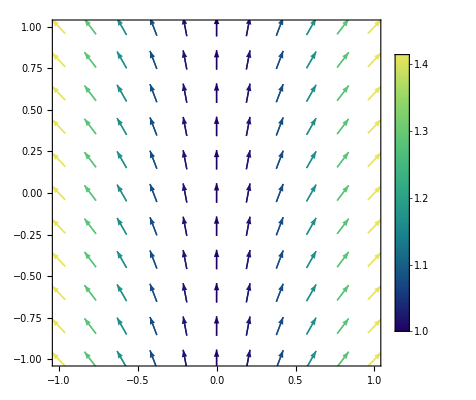

```mathematica
cartTestField[x_,y_,z_]:={x,1.0,0.0}
cartTestVectors=Table[{{x,y},cartTestField[x,y,z][[1;;2]]},{x,-1,1,0.2},{y,-1,1,0.2}];
ListVectorPlot[cartTestVectors,VectorPoints->All,VectorMarkers->"Arrow",VectorSizes->Small,PlotLegends->Automatic,VectorColorFunction->"BlueGreenYellow"]
```

```mathematica
garbageVariableUsedToDefineFunctions=rotateCartesianVector[cartTestField[#1,#2,#3],{ang1,ang2,ang3}]&@@(Inverse[RollPitchYawMatrix[{ang1,ang2,ang3},{3,2,3}]].{x0,y0,z0});
cartTestFieldRotated[x0_,y0_,z0_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
```

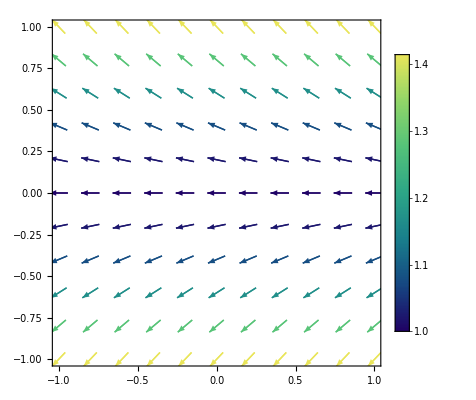

```mathematica
cartTestVectors=Table[{{x,y},cartTestFieldRotated[x,y,z,Pi/2.0,0.0,0.0][[1;;2]]},{x,-1,1,0.2},{y,-1,1,0.2}];
ListVectorPlot[cartTestVectors,VectorPoints->All,VectorMarkers->"Arrow",VectorSizes->Small,PlotLegends->Automatic,VectorColorFunction->"BlueGreenYellow"]
```

#### Test rotation functions with spherical vector field

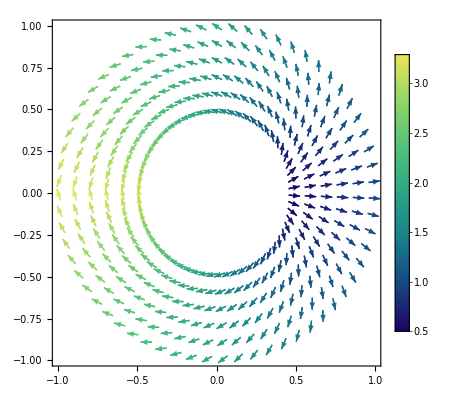

```mathematica
z=0.1;
myTestField[r_,θ_,ϕ_]:={r,0,ϕ}
myTestVectors=Table[{{FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1]],FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[2]]},spherevec2cartvec[myTestField[r,ArcTan[Sqrt[r^2-z^2]/z],phi],{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1;;2]]},{r,0.5,1.0,0.1},{phi,-Pi+0.01,Pi,0.1}];
ListVectorPlot[myTestVectors,VectorPoints->All,VectorMarkers->"Arrow",VectorSizes->Small,PlotLegends->Automatic,VectorColorFunction->"BlueGreenYellow",ColorFunctionScaling->False]
```

```mathematica
(* I think the following is finally correct *)
(* try and combine it all into one line *)
```

```mathematica
(* first convert the field to a cartesian field *)
(*cartesianTestField[x0_,y0_,z0_]:=Evaluate[spherevec2cartvec[myTestField[#1,#2,#3],ToSphericalCoordinates[{x0,y0,z0}]]&@@ToSphericalCoordinates[{x0,y0,z0}]]*)
```

```mathematica
(* rotate the cartesian vector field *)
(*garbageVariableUsedToDefineFunctions=rotateCartesianVector[cartesianTestField[#1,#2,#3],{ang1,ang2,ang3}]&@@(Inverse[RollPitchYawMatrix[{ang1,ang2,ang3},{3,2,3}]].{x0,y0,z0});
cartesianTestField[x0_,y0_,z0_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]*)
```

```mathematica
(* convert back to a spherical vector field *)
(*myTestFieldRotated[r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[rotate spherical vector field[myTestField[r,θ,ϕ]]]*)
```

```mathematica
(*garbageVariableUsedToDefineFunctions=rotateSphericalVector[myTestField[r,θ,ϕ],{r,θ,ϕ},{ang1,ang2,ang3}];*)
myTestFieldRotated[r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[Simplify[rotate spherical vector field[myTestField[r,θ,ϕ]]]]
(*Clear[garbageVariableUsedToDefineFunctions]*)
```

```mathematica
Simplify[myTestFieldRotated[r,θ,ϕ,a,b,c]]
```

{r,(4 r ArcTan[-r (Cos[a] (Cos[θ] Sin[b]-Cos[b] Cos[c-ϕ] Sin[θ])+Sin[a] Sin[θ] Sin[c-ϕ]),r (Cos[θ] Sin[a] Sin[b]-Sin[θ] (Cos[b] Cos[c-ϕ] Sin[a]+Cos[a] Sin[c-ϕ]))] Sin[b] Sin[c-ϕ])/(√(-r^2 (Cos[2 b] (2+6 Cos[2 θ]-2 Cos[2 (c-ϕ)]+Cos[2 (c-θ-ϕ)]+Cos[2 (c+θ-ϕ)])+2 (-5+Cos[2 c] Cos[2 ϕ]+4 Cos[c] Cos[ϕ] Sin[2 b] Sin[2 θ]+2 Cos[2 θ] Sin[c-ϕ]^2+4 Sin[2 b] Sin[c] Sin[2 θ] Sin[ϕ]+Sin[2 c] Sin[2 ϕ])))),-((4 r ArcTan[-r (Cos[a] (Cos[θ] Sin[b]-Cos[b] Cos[c-ϕ] Sin[θ])+Sin[a] Sin[θ] Sin[c-ϕ]),r (Cos[θ] Sin[a] Sin[b]-Sin[θ] (Cos[b] Cos[c-ϕ] Sin[a]+Cos[a] Sin[c-ϕ]))] (Cos[c] Cos[θ] Cos[ϕ] Sin[b]-Cos[b] Sin[θ]+Cos[θ] Sin[b] Sin[c] Sin[ϕ]))/(√(-r^2 (Cos[2 b] (2+6 Cos[2 θ]-2 Cos[2 (c-ϕ)]+Cos[2 (c-θ-ϕ)]+Cos[2 (c+θ-ϕ)])+2 (-5+Cos[2 c] Cos[2 ϕ]+4 Cos[c] Cos[ϕ] Sin[2 b] Sin[2 θ]+2 Cos[2 θ] Sin[c-ϕ]^2+4 Sin[2 b] Sin[c] Sin[2 θ] Sin[ϕ]+Sin[2 c] Sin[2 ϕ])))))}

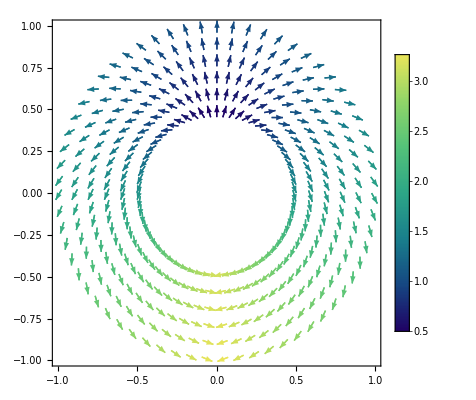

```mathematica
myTestVectorsRotated=Table[{{FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1]],FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[2]]},spherevec2cartvec[myTestFieldRotated[r,ArcTan[Sqrt[r^2-z^2]/z],phi,0.0,0.0,Pi/2.0],{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1;;2]]},{r,0.5,1.0,0.1},{phi,-Pi+0.01,Pi,0.1}];
ListVectorPlot[myTestVectorsRotated,VectorPoints->All,VectorMarkers->"Arrow",VectorSizes->Small,PlotLegends->Automatic,VectorColorFunction->"BlueGreenYellow",ColorFunctionScaling->False]
```

```mathematica
FullSimplify[myTestFieldRotated[r,theta,phi,a,b,c]]
```

{r,(4 r ArcTan[-r (Sin[a] Sin[c-phi] Sin[theta]+Cos[a] (Cos[theta] Sin[b]-Cos[b] Cos[c-phi] Sin[theta])),r (Cos[theta] Sin[a] Sin[b]-(Cos[b] Cos[c-phi] Sin[a]+Cos[a] Sin[c-phi]) Sin[theta])] Sin[b] Sin[c-phi])/(√(r^2 (10-2 Cos[2 (c-phi)]+Cos[2 (b+c-phi)]+Cos[2 (b-c+phi)]-2 Cos[2 b] (1+(3+Cos[2 (c-phi)]) Cos[2 theta])-4 Cos[2 theta] Sin[c-phi]^2-8 Cos[c-phi] Sin[2 b] Sin[2 theta]))),(4 r ArcTan[-r (Sin[a] Sin[c-phi] Sin[theta]+Cos[a] (Cos[theta] Sin[b]-Cos[b] Cos[c-phi] Sin[theta])),r (Cos[theta] Sin[a] Sin[b]-(Cos[b] Cos[c-phi] Sin[a]+Cos[a] Sin[c-phi]) Sin[theta])] (-Cos[c-phi] Cos[theta] Sin[b]+Cos[b] Sin[theta]))/(√(r^2 (10-2 Cos[2 (c-phi)]+Cos[2 (b+c-phi)]+Cos[2 (b-c+phi)]-2 Cos[2 b] (1+(3+Cos[2 (c-phi)]) Cos[2 theta])-4 Cos[2 theta] Sin[c-phi]^2-8 Cos[c-phi] Sin[2 b] Sin[2 theta])))}

```mathematica
FullSimplify[%]
```

{r,(4 r ArcTan[-r (Sin[a] Sin[c-phi] Sin[theta]+Cos[a] (Cos[theta] Sin[b]-Cos[b] Cos[c-phi] Sin[theta])),r (Cos[theta] Sin[a] Sin[b]-(Cos[b] Cos[c-phi] Sin[a]+Cos[a] Sin[c-phi]) Sin[theta])] Sin[b] Sin[c-phi])/(√(r^2 (10-2 Cos[2 (c-phi)]+Cos[2 (b+c-phi)]+Cos[2 (b-c+phi)]-2 Cos[2 b] (1+(3+Cos[2 (c-phi)]) Cos[2 theta])-4 Cos[2 theta] Sin[c-phi]^2-8 Cos[c-phi] Sin[2 b] Sin[2 theta]))),(4 r ArcTan[-r (Sin[a] Sin[c-phi] Sin[theta]+Cos[a] (Cos[theta] Sin[b]-Cos[b] Cos[c-phi] Sin[theta])),r (Cos[theta] Sin[a] Sin[b]-(Cos[b] Cos[c-phi] Sin[a]+Cos[a] Sin[c-phi]) Sin[theta])] (-Cos[c-phi] Cos[theta] Sin[b]+Cos[b] Sin[theta]))/(√(r^2 (10-2 Cos[2 (c-phi)]+Cos[2 (b+c-phi)]+Cos[2 (b-c+phi)]-2 Cos[2 b] (1+(3+Cos[2 (c-phi)]) Cos[2 theta])-4 Cos[2 theta] Sin[c-phi]^2-8 Cos[c-phi] Sin[2 b] Sin[2 theta])))}

```mathematica
myTestVectorsRotated=Table[{{r,theta,phi},myTestFieldRotated[r,ArcTan[Sqrt[r^2-z^2]/z],phi,0.0,Pi/2.0,0.0]},{r,innerRadius,outerRadius,0.1},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
```

```mathematica
myTestVectorsRotated
```

{{{{{0.2,0.01,-3.13159},{0.2,-0.0624751,-3.12365}},{{0.2,0.01,-3.03159},{0.2,-0.637089,-2.88417}},{{0.2,0.01,-2.93159},{0.2,-1.09607,-2.57122}},{{0.2,0.01,-2.83159},{0.2,-1.4325,-2.23599}},56,{{0.2,0.01,2.86841},{0.2,-1.32208,2.35926}},{{0.2,0.01,2.96841},{0.2,-0.94171,2.69156}},{{0.2,0.01,3.06841},{0.2,-0.437509,2.98371}}},30,{1}}}
 |  |  |  |

#### Test on arbitrary field

```mathematica
rotate spherical vector field[{f1[r,θ,ϕ],f2[r,θ,ϕ],f3[r,θ,ϕ]}]
```

{1}
 |  |  |  |

Map Euler angles to points on a sphere

We want to take two Euler angles and use them to map to some point on a unit sphere. We should only need two, so it’s going to be useful to just use the first two: RollPitchYawMatrix[{α, β, 0}]. The issue here is just maintaining a consistency in the cross/plus polarization. I think it’s fine to just say that plus corresponds to γ = 0 and cross corresponds to γ = π/4. Let’s give this a shot.

α rotates about z axis
β rotates about y axis
γ rotates about z axis

```mathematica
(* α should range from 0 to π and β should range from 0 to 2π *)
eulerAngles={α,β,γ};

xhat={1,0,0};
yhat={0,1,0};
zhat={0,0,1};

xhatp=RollPitchYawMatrix[eulerAngles,{3,2,3}].xhat;
yhatp=RollPitchYawMatrix[eulerAngles,{3,2,3}].yhat;
zhatp=RollPitchYawMatrix[eulerAngles,{3,2,3}].zhat;

zInSpherical=Simplify[ToSphericalCoordinates[zhatp]];
θfnc[α_,β_,γ_]:=Evaluate[zInSpherical[[2]]];
ϕfnc[α_,β_,γ_]:=Evaluate[zInSpherical[[3]]];
euler2spherical[α_,β_,γ_]:={β,α}
euler2spherical3d[α_,β_,γ_]:={1.0,β,α}
```

Aitoff projection

```mathematica
(*aitoff[θ_,ϕ_]:={(2*Cos[θ+Pi/2]*Sin[ϕ/2])/Sinc[ArcCos[Cos[θ+Pi/2]*Cos[ϕ/2]]], Sin[θ+Pi/2]/Sinc[ArcCos[Cos[θ+Pi/2]*Cos[ϕ/2]]]}*)
Clear[aitoff]
aitoff[θ_,ϕ_]:={(2*Cos[θ-Pi/2]*Sin[ϕ/2])/Sinc[ArcCos[Cos[θ-Pi/2]*Cos[ϕ/2]]], Sin[θ-Pi/2]/Sinc[ArcCos[Cos[θ-Pi/2]*Cos[ϕ/2]]]}
```

# Single Spherical Shell Mechanical-EM Coupling

Import Resonant Frequencies

```mathematica
MODES1 =Quiet[ToExpression[Quiet[Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/NbCavity-r=0.2-0.005.txt"]]]];
MODES2=Quiet[ToExpression[Quiet[Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/NbCavity-r=0.2-0.005-real-high-n.txt"]]]];
MODES={Join[MODES1[[1]],MODES2[[1]]]};
waveNumbersK=Table[Quiet["wavenumberk"/.(StringJoin["m",ToString[m],"n",ToString[n],"l",ToString[If[m==2,2,0]]]/.MODES[[1]])],{m,0,10},{n,0,128}];
waveNumbersP=Table[Quiet["wavenumberp"/.(StringJoin["m",ToString[m],"n",ToString[n],"l",ToString[If[m==2,2,0]]]/.MODES[[1]])],{m,0,10},{n,0,128}];
```

Get Bessel function zeros sorted

```mathematica
garbageVariableUsedToDefineFunctions=FullSimplify[D[x*SphericalBesselJ[n,x],x]];
sphericalBesselDerivative[n_,x_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
garbageVariableUsedToDefineFunctions=x*SphericalBesselJ[n,x];
sphericalBessel[n_,x_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]

sphericalBesselJZero = Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/SphereModes/bessel-zeros/norm_spherical_bessel_zeros.txt", "CSV"];
sphericalBesselJDerivZero = Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/SphereModes/bessel-zeros/norm_spherical_bessel_derivatives_zeros.txt", "CSV"];

SphericalBesselJZero[n_,p_]:=sphericalBesselJZero[[n+1]][[p]]
SphericalBesselJDerivZero[n_,p_]:=sphericalBesselJDerivZero[[n+1]][[p]]
```

Define Functions

#### Write down the mechanical modes for a spherical shell

```mathematica
wavek[m_,n_,l_,a_]:=Inactivate[waveNumbersK[[m+1,n+1]]]
wavep[m_,n_,l_,a_]:=Inactivate[waveNumbersP[[m+1,n+1]]]
omegaMech[m_,n_,l_,a_]:=vt*Sqrt[wavek[m,n,l,a]]

Nnm=Simplify[Grad[SphericalBesselJ[m,wavep[m,n,l,a]*r],{r,θ,ϕ},"Spherical"]-2*c2ratio*Grad[SphericalBesselJ[m,wavek[m,n,l,a]*r],{r,θ,ϕ},"Spherical"]-c2ratio*r*D[Grad[SphericalBesselJ[m,wavek[m,n,l,a]*r],{r,θ,ϕ},"Spherical"],r]+c2ratio*{r,0,0}*Laplacian[SphericalBesselJ[m,wavek[m,n,l,a]*r],{r,θ,ϕ},"Spherical"]-c2ratio*{r,0,0}*SphericalBesselJ[m,wavek[m,n,l,a]*r]*m*(m+1)/r^2 +d0ratio*Grad[SphericalBesselY[m,wavep[m,n,l,a]*r],{r,θ,ϕ},"Spherical"]-2*d2ratio*Grad[SphericalBesselY[m,wavek[m,n,l,a]*r],{r,θ,ϕ},"Spherical"]-d2ratio*r*D[Grad[SphericalBesselY[m,wavek[m,n,l,a]*r],{r,θ,ϕ},"Spherical"],r]+d2ratio*{r,0,0}*Laplacian[SphericalBesselY[m,wavek[m,n,l,a]*r],{r,θ,ϕ},"Spherical"]-d2ratio*{r,0,0}*SphericalBesselY[m,wavek[m,n,l,a]*r]*m*(m+1)/r^2,Assumptions->{m>=0,l>=0,l<=m}];
Enm=Simplify[SphericalBesselJ[m,wavep[m,n,l,a]*r]-1*c2ratio*SphericalBesselJ[m,wavek[m,n,l,a]*r]-c2ratio*r*D[SphericalBesselJ[m,wavek[m,n,l,a]*r],r]+d0ratio*SphericalBesselY[m,wavep[m,n,l,a]*r]-1*d2ratio*SphericalBesselY[m,wavek[m,n,l,a]*r]-d2ratio*r*D[SphericalBesselY[m,wavek[m,n,l,a]*r],r],Assumptions->{m>=0,l>=0,l<=m}];

garbageVariableUsedToDefineFunctions=Simplify[Nnm*SphericalHarmonicY[m,l,θ,ϕ] + Enm*Grad[SphericalHarmonicY[m,l,θ,ϕ],{r,θ,ϕ},"Spherical"],Assumptions->{m>=0,l>=0,l<=m}];
displacementVecQnorm[m_,n_,l_,a_,d0ratio_,c2ratio_,d2ratio_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]

displacementVecQnotRotated[m_,n_,l_,a_,c0_,d0_,c1_,d1_,c2_,d2_,r_,θ_,ϕ_]:=Evaluate[c0*displacementVecQnorm[m,n,l,a,d0/c0,c2/c0,d2/c0,r,θ,ϕ]]

garbageVariableUsedToDefineFunctions=rotate spherical vector field[displacementVecQnotRotated[m,n,l,a,c0,d0,c1,d1,c2,d2,r,θ,ϕ]];
displacementVecQ[m_,n_,l_,a_,c0_,d0_,c1_,d1_,c2_,d2_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
```

#### EM modes from a vector potential

This section draws from chapter (4) of Hill. There, the magnetic displacement field is given instead of B, but if you set c = 1 and use B instead of H, then you should get that the amplitudes of the TM and TE vector potentials are in the same units (both in units of V/m).

```mathematica
(* TE frequencies *)
wavenumberTE[m_,n_,p_,a_]:=Inactivate[SphericalBesselJZero[n,p]]/a
omegaTE[m_,n_,p_,a_]:=SPEEDOFLIGHT*wavenumberTE[m,n,p,a]
(* TM frequencies *)
wavenumberTM[m_,n_,p_,a_]:=Inactivate[SphericalBesselJDerivZero[n,p]]/a
omegaTM[m_,n_,p_,a_]:=SPEEDOFLIGHT*wavenumberTM[m,n,p,a]
(* all frequencies *)
wavenumberEM[m_,n_,p_,a_,tmorte_]:=If[tmorte==1,wavenumberTM[m,n,p,a],wavenumberTE[m,n,p,a]]
omegaEM[m_,n_,p_,a_,tmorte_]:=If[tmorte==1,omegaTM[m,n,p,a],omegaTE[m,n,p,a]]

(* Transverse electric vector potential *)
vectorPotentialTE[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_]:={amplitude*r*SphericalBesselJ[n,k*r]*LegendreP[n,m,Cos[θ]]*If[parity==1,Cos[m*ϕ],Sin[m*ϕ]],0,0}
(* Transverse magnetic vector potential *)
vectorPotentialTM[amplitude_,parity_,m_,n_,p_,a_,k_,r_,θ_,ϕ_]:={amplitude*r*SphericalBesselJ[n,k*r]*LegendreP[n,m,Cos[θ]]*If[parity==1,Cos[m*ϕ],Sin[m*ϕ]],0,0}

(* calculate electric and magnetic fields for TE modes *)
garbageVariableUsedToDefineFunctions=Simplify[Evaluate[-Curl[vectorPotentialTE[amplitude,parity, m,n,p,a,k,r,θ,ϕ],{r,θ,ϕ},"Spherical"]]];
electricFieldTEnotrotated[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
garbageVariableUsedToDefineFunctions=Simplify[Module[{r0,θ0,ϕ0},Evaluate[(1/k)*Curl[Curl[vectorPotentialTE[amplitude,parity, m,n,p,a,k,r0,θ0,ϕ0],{r0,θ0,ϕ0},"Spherical"],{r0,θ0,ϕ0},"Spherical"]]/.{r0->r,θ0->θ,ϕ0->ϕ}]];
garbageVariableUsedToDefineFunctions=Curl[vectorPotentialTE[amplitude,parity, m,n,p,a,k,r0,θ0,ϕ0],{r0,θ0,ϕ0},"Spherical"];
garbageVariableUsedToDefineFunctions=(1/k)*Curl[garbageVariableUsedToDefineFunctions,{r0,θ0,ϕ0},"Spherical"]/.{r0->r,θ0->θ,ϕ0->ϕ};
magneticFieldTEnotrotated[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]

(* calculate electric and magnetic fields for TE modes *)
garbageVariableUsedToDefineFunctions=Simplify[Module[{r0,θ0,ϕ0},Evaluate[(1/k)*Curl[Curl[vectorPotentialTM[amplitude,parity, m,n,p,a,k,r,θ,ϕ],{r,θ,ϕ},"Spherical"],{r,θ,ϕ},"Spherical"]]/.{r0->r,θ0->θ,ϕ0->ϕ}]];
electricFieldTMnotrotated[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
garbageVariableUsedToDefineFunctions=Simplify[Module[{r0,θ0,ϕ0},Evaluate[Curl[vectorPotentialTM[amplitude,parity, m,n,p,a,k,r,θ,ϕ],{r,θ,ϕ},"Spherical"]]/.{r0->r,θ0->θ,ϕ0->ϕ}]];
magneticFieldTMnotrotated[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]

(* calculate the rotated versions of these fields using the same method as for the mechanical mode rotations *)
garbageVariableUsedToDefineFunctions=rotate spherical vector field[electricFieldTEnotrotated[amplitude,parity, m,n,p,a,k,r,θ,ϕ]];
electricFieldTE[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]

garbageVariableUsedToDefineFunctions=rotate spherical vector field[magneticFieldTEnotrotated[amplitude,parity, m,n,p,a,k,r,θ,ϕ]];
magneticFieldTE[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]

garbageVariableUsedToDefineFunctions=rotate spherical vector field[electricFieldTMnotrotated[amplitude,parity, m,n,p,a,k,r,θ,ϕ]];
electricFieldTM[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]

garbageVariableUsedToDefineFunctions=rotate spherical vector field[magneticFieldTMnotrotated[amplitude,parity, m,n,p,a,k,r,θ,ϕ]];
magneticFieldTM[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]

(* define functions for total electric and magnetic fields *)
electricField[amplitude_,parity_,TMorTE_, m_,n_,p_,a_,k_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=If[TMorTE==1,electricFieldTM[amplitude,parity, m,n,p,a,k,r,θ,ϕ,ang1,ang2,ang3],electricFieldTE[amplitude,parity, m,n,p,a,k,r,θ,ϕ,ang1,ang2,ang3]]
magneticField[amplitude_,parity_,TMorTE_, m_,n_,p_,a_,k_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=If[TMorTE==1,magneticFieldTM[amplitude,parity, m,n,p,a,k,r,θ,ϕ,ang1,ang2,ang3],magneticFieldTE[amplitude,parity, m,n,p,a,k,r,θ,ϕ,ang1,ang2,ang3]]

(* create compiled functions for EM fields 
electricFieldC=Compile[{{amplitude,_Real},{parity,_Integer},{TMorTE,_Integer}, {m,_Integer},{n,_Integer},{p,_Integer},{a,_Real},{k,_Real},{r,_Real},{θ,_Real},{ϕ,_Real},{ang1,_Real},{ang2,_Real},{ang3,_Real}},electricField[amplitude,parity,TMorTE, m,n,p,a,k,r,θ,ϕ,ang1,ang2,ang3]]*)
```

#### Get EM normalization

```mathematica
(* for now we're ignoring the normalization because it makes everything way longer to calculate. we can add it back in if/when necessary *)
getNormalizationFactor[parity_,mem_,nem_,pem_,a_,tmorte_,k_]:=(*Sqrt[((4/3)*Pi*a^2)/NIntegrate[Norm[electricField[1.0,parity,tmorte,mem,nem,pem,a,k,r,theta,phi,0.0,0.0,0.0]]^2*r^2*Sin[theta],{r,0.0,a},{phi,0.0,2.0*Pi},{theta,0.0,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^5]]*)1.0
```

#### Get energy associated with an electric field configuration

```mathematica
(* using the definition from Sebastian's notes *)
calculateEMFieldEnergy[TMorTE_,amplitude_,parity_,m_,n_,p_,a_,k_]:=(1/2)*NIntegrate[r^2*Sin[θ]*Norm[electricField[amplitude,parity,TMorTE,m,n,p,a,k,r,θ,ϕ,0.0,0.0,0.0]]^2*getNormalizationFactor[parity,m,n,p,a,TMorTE,k]^2,{r,0.0,a},{θ,0.0,Pi},{ϕ,0.0,2.0*Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^4,PrecisionGoal->2]
```

#### Calculate the overlap factor (η^m)_ij

```mathematica
(* mVec = {inclination, radial, azimuth} numbers for mechanical modes
iVec = {azimuth, inclination, radial} numbers for EM mode i 1
jVec= ----------------''------------------------
a  = innder radius of sphere
modeCoefs = {c0, d0, c1, d1, c2, d2} for mechanical modes
EMamplitude = amplitude of electric field for both fields, should be set to 1
TMorTEField = 1 for TM field and 0 for TE field
parityOfField = 1 for even parity 0 for odd (I get the stupidity here)
ki, kj, wi, wj = wave numbers and frequencies for the waves
theta, phi = overall integration variables
offsets = three sets of three Euler angles to define coordinate rotations for each of the EM fields and the mechanical mode *)
overlapIntegrand[mVec_,iVec_,jVec_,a_,modeCoefs_,EMamplitude_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_,ki_,kj_,wi_,wj_,θ_,ϕ_,offsets_,align_]:=(a^2*Sin[θ] * (displacementVecQ[mVec[[1]],mVec[[2]],mVec[[3]],a,modeCoefs[[1]],modeCoefs[[2]],modeCoefs[[3]],modeCoefs[[4]],modeCoefs[[5]],modeCoefs[[6]],a,θ,ϕ,offsets[[1]],offsets[[2]],offsets[[3]]].{1,0,0}) * ((wi/wj) * magneticField[EMamplitude,parityOfFieldj,TMorTEFeildj, jVec[[1]], jVec[[2]], jVec[[3]],a,kj,a,θ,ϕ,offsets[[4]],offsets[[5]],offsets[[6]]].magneticField[EMamplitude,parityOfFieldi,TMorTEFeildi,iVec[[1]], iVec[[2]], iVec[[3]],a,ki,a,θ,ϕ,offsets[[4]],offsets[[5]],offsets[[6]]]*align- electricField[EMamplitude,parityOfFieldj,TMorTEFeildj,jVec[[1]], jVec[[2]], jVec[[3]],a,kj,a,θ,ϕ,offsets[[4]],offsets[[5]],offsets[[6]]].electricField[EMamplitude,parityOfFieldi,TMorTEFeildi,iVec[[1]], iVec[[2]], iVec[[3]],a,ki,a,θ,ϕ,offsets[[4]],offsets[[5]],offsets[[6]]]*align))

overlapfunction[modes_,a_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_,ki_,kj_,wi_,wj_,offsets_,align_]:=((4*Pi*a^3/3)^(1/3)/(2*calculateEMFieldEnergy[TMorTEFeildi,1.0,parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,ki])) *NIntegrate[Re[Activate[overlapIntegrand[{modes[[1]],modes[[2]],modes[[3]]},{modes[[4]],modes[[5]],modes[[6]]},{modes[[7]],modes[[8]],modes[[9]]},a,{"C0","D0",0.0,0.0,"C2","D2"}/.Quiet[(StringJoin["m",ToString[modes[[1]]],"n",ToString[modes[[2]]],"l",ToString[modes[[3]]]]/.MODES[[1]])],1.0,TMorTEFeildi,TMorTEFeildj,parityOfFieldi,parityOfFieldj,ki,kj,wi,wj,θ,ϕ,offsets,align]]], {θ,0.0,Pi},{ϕ,-Pi,Pi}, Method->{"AdaptiveMonteCarlo"},MaxPoints->10^5,PrecisionGoal->2]*getNormalizationFactor[parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeildi,ki]*getNormalizationFactor[parityOfFieldj,modes[[7]],modes[[8]],modes[[9]],a,TMorTEFeildj,kj]

overlapfunctionGlobalAdaptive[modes_,a_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_,ki_,kj_,wi_,wj_,offsets_,align_]:=((4*Pi*a^3/3)^(1/3)/(2*calculateEMFieldEnergy[TMorTEFeildi,1.0,parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,ki])) *NIntegrate[Re[Activate[overlapIntegrand[{modes[[1]],modes[[2]],modes[[3]]},{modes[[4]],modes[[5]],modes[[6]]},{modes[[7]],modes[[8]],modes[[9]]},a,{"C0","D0",0.0,0.0,"C2","D2"}/.Quiet[(StringJoin["m",ToString[modes[[1]]],"n",ToString[modes[[2]]],"l",ToString[modes[[3]]]]/.MODES[[1]])],1.0,TMorTEFeildi,TMorTEFeildj,parityOfFieldi,parityOfFieldj,ki,kj,wi,wj,θ,ϕ,offsets,align]]], {θ,0.0,Pi},{ϕ,-Pi,Pi}, Method->"MultidimensionalRule",PrecisionGoal->2]*getNormalizationFactor[parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeildi,ki]*getNormalizationFactor[parityOfFieldj,modes[[7]],modes[[8]],modes[[9]],a,TMorTEFeildj,kj]

overlapfunctionTrap[modes_,a_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_,ki_,kj_,wi_,wj_,offsets_,align_]:=((4*Pi*a^3/3)^(1/3)/(2*calculateEMFieldEnergy[TMorTEFeildi,1.0,parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,ki])) *NIntegrate[Re[Activate[overlapIntegrand[{modes[[1]],modes[[2]],modes[[3]]},{modes[[4]],modes[[5]],modes[[6]]},{modes[[7]],modes[[8]],modes[[9]]},a,{"C0","D0",0.0,0.0,"C2","D2"}/.Quiet[(StringJoin["m",ToString[modes[[1]]],"n",ToString[modes[[2]]],"l",ToString[modes[[3]]]]/.MODES[[1]])],1.0,TMorTEFeildi,TMorTEFeildj,parityOfFieldi,parityOfFieldj,ki,kj,wi,wj,θ,ϕ,offsets,align]]], {θ,0.0,Pi},{ϕ,-Pi,Pi}, Method->"Trapezoidal",PrecisionGoal->1]*getNormalizationFactor[parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeildi,ki]*getNormalizationFactor[parityOfFieldj,modes[[7]],modes[[8]],modes[[9]],a,TMorTEFeildj,kj]

overlapfunctionParallel[modes_,a_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_,ki_,kj_,wi_,wj_,offsets_,align_]:=((4*Pi*a^3/3)^(1/3)/(2*calculateEMFieldEnergy[TMorTEFeildi,1.0,parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,ki])) *NIntegrate[Re[Activate[overlapIntegrand[{modes[[1]],modes[[2]],modes[[3]]},{modes[[4]],modes[[5]],modes[[6]]},{modes[[7]],modes[[8]],modes[[9]]},a,{"C0","D0",0.0,0.0,0.0,0.0}/.Quiet[(StringJoin["m",ToString[modes[[1]]],"n",ToString[modes[[2]]],"l",ToString[modes[[3]]]]/.MODES[[1]])],1.0,TMorTEFeildi,TMorTEFeildj,parityOfFieldi,parityOfFieldj,ki,kj,wi,wj,θ,ϕ,offsets,align]]], {θ,0.0,Pi},{ϕ,-Pi,Pi}, Method->{"AdaptiveMonteCarlo"},MaxPoints->10^4,PrecisionGoal->2]*getNormalizationFactor[parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeildi,ki]*getNormalizationFactor[parityOfFieldj,modes[[7]],modes[[8]],modes[[9]],a,TMorTEFeildj,kj]

overlap1Sphere2Modes[modes_,a_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_,offsets_]:=overlapfunction[modes,a,TMorTEFeildi,TMorTEFeildj,parityOfFieldi,parityOfFieldj,Activate[wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeildi]],Activate[wavenumberEM[modes[[7]],modes[[8]],modes[[9]],a,TMorTEFeildj]],Activate[wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeildi]],Activate[wavenumberEM[modes[[7]],modes[[8]],modes[[9]],a,TMorTEFeildj]],offsets,1]
```

#### Calculate angular momentum of configuration

```mathematica
angularMomentumEM[m_,n_,p_,a_,tmorte_,parity_,k_,ang1_,ang2_,ang3_]:=NIntegrate[Cross[{r,0,0},Cross[electricField[1.0,parity,tmorte,m,n,p,a,k,r,θ,ϕ,ang1,ang2,ang3],magneticField[1.0,parity,tmorte,m,n,p,a,k,r,θ,ϕ,ang1,ang2,ang3]]]*r^2*Sin[θ],{r,0.0,a},{θ,0.01,Pi},{ϕ,-Pi+0.01,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^5,PrecisionGoal->2]
```

```mathematica
garbageVariableUsedToDefineFunctions=Cross[{r,0,0},({r,0,0}+displacementVecQ[m,n,l,a,c0,d0,c1,d1,c2,d2,r,θ,ϕ,ang1,ang2,ang3]*wavek[m,n,l,a]^(1/2))]*r^2*Sin[θ];
```

```mathematica
angularMomentumMechint[m_,n_,l_,a_,c0_,d0_,c1_,d1_,c2_,d2_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions];
angularMomentumMech[m_,n_,l_,a_,c0_,d0_,c1_,d1_,c2_,d2_,ang1_,ang2_,ang3_]:=NIntegrate[angularMomentumMechint[m,n,l,a,c0,d0,c1,d1,c2,d2,r,θ,ϕ,ang1,ang2,ang3],{r,0.0,a},{θ,0.01,Pi},{ϕ,-Pi+0.01,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^4,PrecisionGoal->2]
```

Sanity Tests of Functions

#### Make animation of mechanical mode

```mathematica
(* make unperturbed sphere *)
(*unperturbedSphere=Table[spherical2cartesian[{1.0,θ,ϕ}],{ϕ,0.01,2.0*Pi,0.1},{θ,0.01,Pi,0.1}];
(* make perturbations to the sphere *)
perturbationsToSphere=Table[spherical2cartesian[Re[displacementVecQ[1,1,0,1.0,1.0,1.0,0.0,0.0,0.0,0.0,1.0,θ,ϕ]]],{ϕ,0.01,2.0*Pi,0.1},{θ,0.01,Pi,0.1}];
(*ListPlot3D[unperturbedSphere+perturbationsToSphere,ColorFunction->GrayLevel,Interpolati*)onOrder->3,Axes->False,Boxed->False,AspectRatio->1,PlotRange->{{-2.5,2.5},{-2.5,2.5},{-2.5,2.5}},ViewPoint->{0, -2, 0}]*)
```

```mathematica
(*ListSurfacePlot3D[ArrayFlatten[unperturbedSphere,1]+ArrayFlatten[perturbationsToSphere,1],MaxPlotPoints->30,Axes->False,Boxed->False,AspectRatio->1,PlotRange->{{-2.5,2.5},{-2.5,2.5},{-2.5,2.5}},ViewPoint->{-1, -2, 2}]*)
```

```mathematica
(* make plots and animations *)
(*animationPlots=Table[ListSurfacePlot3D[ArrayFlatten[unperturbedSphere,1]+ArrayFlatten[perturbationsToSphere,1]*0.2*Cos[Pi*t],MaxPlotPoints->30,Axes->False,Boxed->False,AspectRatio->1,PlotRange->{{-2.5,2.5},{-2.5,2.5},{-2.5,2.5}},ViewPoint->{-1, -2, 1.5}],{t,0.0,4.0,0.1}];
Export["/Users/wentmich/Documents/uiuc/research/GWs/mechanical-modes/mech-mode-animations/sphere-mode.gif",animationPlots,"GIF"]*)
```

The mechanical mode function appears to be working well.

#### Density plot of mechanical modes

```mathematica
(* test wrapping density plot on sphere *)
data=Flatten[Table[{{x,y},Cos[4 x]+Sin[2 y]+.1 RandomReal[]},{x,0,Pi+.1,.01},{y,0,2 Pi+.1,.01}],1];
f=Interpolation[data];
SphericalPlot3D[1,{u,0,Pi}, {v, 0, 2*Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData["Rainbow"][Rescale[f[u,v],{-2,2}]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3]]
```

-Graphics3D-

```mathematica
mvec={2,0,2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[1,{theta,0,Pi}, {phi, 0,2* Pi}, ColorFunction -> Function[{x,y,z,r,theta,phi},ColorData["Rainbow"][Rescale[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,0.0,0.0][[1]]]],{-1,1}]]],ColorFunctionScaling->False,SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],Mesh->None,MaxRecursion->0]
```

-Graphics3D-

```mathematica
mvec={2,0,0};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[1,{theta,0,Pi}, {phi, 0,2* Pi}, ColorFunction -> Function[{x,y,z,r,theta,phi},ColorData["Rainbow"][Rescale[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,0.0,0.0][[1]]]],{-1,1}]]],ColorFunctionScaling->False,SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],Mesh->None,MaxRecursion->0]
```

-Graphics3D-

```mathematica
mvec={2,0,0};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[1,{theta,0,Pi}, {phi, 0,2* Pi}, ColorFunction -> Function[{x,y,z,r,theta,phi},ColorData["Rainbow"][Rescale[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,Pi/2.0,0.0][[1]]]],{-1,1}]]],ColorFunctionScaling->False,SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],Mesh->None,MaxRecursion->0]
```

-Graphics3D-

```mathematica
BarLegend[{"Rainbow",{-1,1}}]
```

```mathematica
mvec={2,0,2};
SphericalPlot3D[1,{theta,0,Pi}, {phi, -Pi, Pi}, ColorFunction -> Function[{x,y,z,r,theta,phi},ColorData["BlueGreenYellow"][Rescale[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,0.0,0.0][[1]]]],{-1,1}]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,r,theta,phi},Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,0.0,0.0][[1]]]]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PerformanceGoal->"Speed",MaxRecursion->0,PlotTheme->"Scientific"]
```

-Graphics3D-

```mathematica
mvec={2,0,0};
SphericalPlot3D[1,{theta,0,Pi}, {phi, -Pi, Pi}, ColorFunction -> Function[{x,y,z,r,theta,phi},ColorData["BlueGreenYellow"][Rescale[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,Pi/2.0,0.0][[1]]]],{-1,1}]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,r,theta,phi},Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,Pi/2.0,0.0][[1]]]]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PerformanceGoal->"Speed",MaxRecursion->0,PlotTheme->"Scientific"]
```

-Graphics3D-

#### Make plots of mechanical modes

We want to plot sections of the mechanical mode to see if it looks like a quadrupole. Just plot everything at a fixed radius a = innerRadius.

```mathematica
mvec={2,0,0};
coefs={"C0","D0",0.0,0.0,"C2","D2"}/.StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]];
displacements=Flatten[Table[{theta,phi,Re[Activate[displacementVecQnotRotated[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi]]]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}],1];
```

```mathematica
displacementsR={};
For[i=1,i<Length[displacements],i++,AppendTo[displacementsR,{aitoff[displacements[[i]][[1]],displacements[[i]][[2]]][[1]],aitoff[displacements[[i]][[1]],displacements[[i]][[2]]][[2]],displacements[[i]][[3]][[1]]}]];
displacementsTheta={};
For[i=1,i<Length[displacements],i++,AppendTo[displacementsTheta,{aitoff[displacements[[i]][[1]],displacements[[i]][[2]]][[1]],aitoff[displacements[[i]][[1]],displacements[[i]][[2]]][[2]],displacements[[i]][[3]][[2]]}]];
displacementsPhi={};
For[i=1,i<Length[displacements],i++,AppendTo[displacementsPhi,{aitoff[displacements[[i]][[1]],displacements[[i]][[2]]][[1]],aitoff[displacements[[i]][[1]],displacements[[i]][[2]]][[2]],displacements[[i]][[3]][[3]]}]];
```

```mathematica
ListContourPlot[displacementsR,PlotTheme->"Scientific", InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ColorFunctionScaling->True,PlotLegends->Automatic,Contours->7]
ListContourPlot[displacementsTheta,PlotTheme->"Scientific", InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ColorFunctionScaling->True,PlotLegends->Automatic,Contours->7]
ListContourPlot[displacementsPhi,PlotTheme->"Scientific", InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ColorFunctionScaling->True,PlotLegends->Automatic,Contours->7]
```

-Graphics-

-Graphics-

-Graphics-

#### Circle plots of mechanical modes

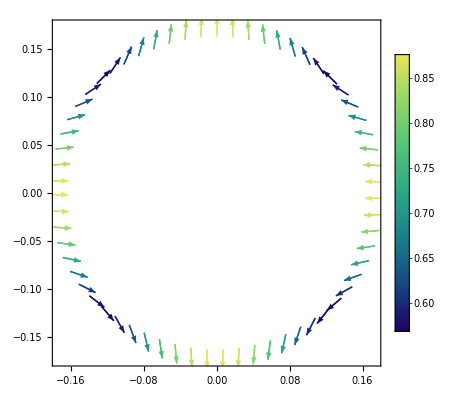

```mathematica
spherevec2cartvec[A_,p_]:={A[[1]]*Sin[p[[2]]]*Cos[p[[3]]]+A[[2]]*Cos[p[[2]]]*Cos[p[[3]]]-A[[3]]*Sin[p[[3]]],A[[1]]*Sin[p[[2]]]*Sin[p[[3]]]+A[[2]]*Cos[p[[2]]]*Sin[p[[3]]]+A[[3]]*Cos[p[[3]]],A[[1]]*Cos[p[[2]]]-A[[2]]*Sin[p[[2]]]}
mvec={2,0,2};
z=0.1;
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myModeVectors=Table[{{FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1]],FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[2]]},spherevec2cartvec[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],r,ArcTan[Sqrt[r^2-z^2]/z],phi,0.0,0.0,0.0]]],{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1;;2]]},{r,innerRadius,outerRadius,0.1},{phi,-Pi+0.01,Pi,0.1}];
ListVectorPlot[myModeVectors,VectorPoints->All,VectorMarkers->"Arrow",VectorSizes->Small,PlotLegends->Automatic,VectorColorFunction->"BlueGreenYellow"]
```

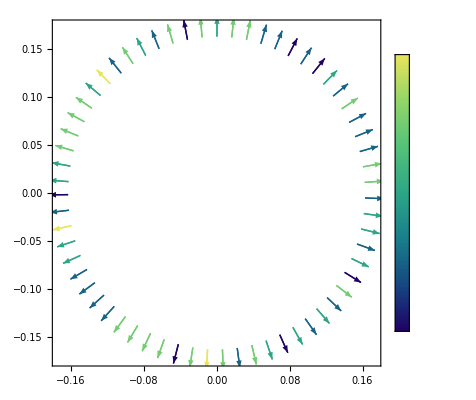

```mathematica
spherevec2cartvec[A_,p_]:={A[[1]]*Sin[p[[2]]]*Cos[p[[3]]]+A[[2]]*Cos[p[[2]]]*Cos[p[[3]]]-A[[3]]*Sin[p[[3]]],A[[1]]*Sin[p[[2]]]*Sin[p[[3]]]+A[[2]]*Cos[p[[2]]]*Sin[p[[3]]]+A[[3]]*Cos[p[[3]]],A[[1]]*Cos[p[[2]]]-A[[2]]*Sin[p[[2]]]}
mvec={2,0,0};
z=0.1;
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myModeVectors=Table[{{FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1]],FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[2]]},spherevec2cartvec[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],r,ArcTan[Sqrt[r^2-z^2]/z],phi,0.0,0.0,0.0]]],{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1;;2]]},{r,innerRadius,outerRadius,0.1},{phi,-Pi+0.01,Pi,0.1}];
ListVectorPlot[myModeVectors,VectorPoints->All,VectorMarkers->"Arrow",VectorSizes->Small,PlotLegends->Automatic,VectorColorFunction->"BlueGreenYellow"]
```

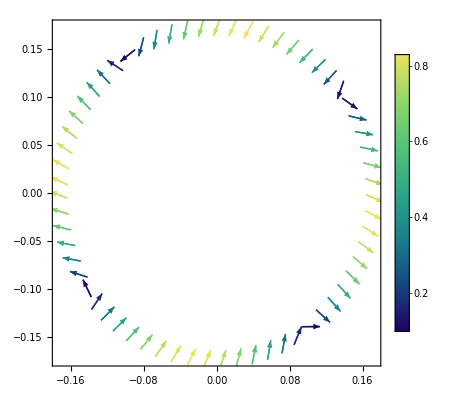

```mathematica
spherevec2cartvec[A_,p_]:={A[[1]]*Sin[p[[2]]]*Cos[p[[3]]]+A[[2]]*Cos[p[[2]]]*Cos[p[[3]]]-A[[3]]*Sin[p[[3]]],A[[1]]*Sin[p[[2]]]*Sin[p[[3]]]+A[[2]]*Cos[p[[2]]]*Sin[p[[3]]]+A[[3]]*Cos[p[[3]]],A[[1]]*Cos[p[[2]]]-A[[2]]*Sin[p[[2]]]}
mvec={2,0,2};
z=0.1;
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myModeVectors=Table[{{FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1]],FromSphericalCoordinates[{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[2]]},spherevec2cartvec[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],r,ArcTan[Sqrt[r^2-z^2]/z],phi,Pi/2.0,0.0,0.0]]],{r,ArcTan[Sqrt[r^2-z^2]/z],phi}][[1;;2]]},{r,innerRadius,outerRadius,0.1},{phi,-Pi+0.01,Pi,0.1}];
ListVectorPlot[myModeVectors,VectorPoints->All,VectorMarkers->"Arrow",VectorSizes->Small,PlotLegends->Automatic,VectorColorFunction->"BlueGreenYellow"]
```

#### Sphere plots of mechanical modes

```mathematica
spherevec2cartvec[A_,p_]:={A[[1]]*Sin[p[[2]]]*Cos[p[[3]]]+A[[2]]*Cos[p[[2]]]*Cos[p[[3]]]-A[[3]]*Sin[p[[3]]],A[[1]]*Sin[p[[2]]]*Sin[p[[3]]]+A[[2]]*Cos[p[[2]]]*Sin[p[[3]]]+A[[3]]*Cos[p[[3]]],A[[1]]*Cos[p[[2]]]-A[[2]]*Sin[p[[2]]]}
mvec={2,5,0};
Clear[r0];
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myModeVectors=Table[{{FromSphericalCoordinates[{r0,theta,phi}][[1]],FromSphericalCoordinates[{r0,theta,phi}][[2]],FromSphericalCoordinates[{r0,theta,phi}][[3]]},spherevec2cartvec[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],r0,theta,phi,0.0,0.0,0.0]]],{r0,theta,phi}]},{r0,innerRadius,outerRadius,0.001},{theta,0.01,Pi,0.2},{phi,-Pi+0.01,Pi,0.3}];
```

```mathematica
ListVectorPlot3D[myModeVectors]
```

ListVectorPlot3D[{{{{{-0.00199987,-0.0000199993,0.19999},{0.0389944,0.000389957,0.00608922}},{{-0.00190464,-0.000610107,0.19999},{0.0371375,0.0118962,0.00608922}},17,{{-0.00168033,0.0010846,0.19999},{0.0327639,-0.0211481,0.00608922}},{{-0.0019258,0.000539591,0.19999},{0.0375502,-0.0105212,0.00608922}}},14,{1}},4,{{1},14,{1}}}]
 |  |  |  |

```mathematica
vectors=Table[{{x,y,z},{y,x-x^3,z}},{x,-1.5,1.5,0.2},{y,-2,2,0.2},{z,-1,1,0.1}];
vectors
ListVectorPlot3D[vectors]
```

{{{{{-1.5,-2.,-1.},{-2.,1.875,-1.}},{{-1.5,-2.,-0.9},{-2.,1.875,-0.9}},{{-1.5,-2.,-0.8},{-2.,1.875,-0.8}},{{-1.5,-2.,-0.7},{-2.,1.875,-0.7}},{{-1.5,-2.,-0.6},{-2.,1.875,-0.6}},{{-1.5,-2.,-0.5},{-2.,1.875,-0.5}},{{-1.5,-2.,-0.4},{-2.,1.875,-0.4}},{{-1.5,-2.,-0.3},{-2.,1.875,-0.3}},{{-1.5,-2.,-0.2},{-2.,1.875,-0.2}},{{-1.5,-2.,-0.1},{-2.,1.875,-0.1}},{{-1.5,-2.,0.},{-2.,1.875,0.}},{{-1.5,-2.,0.1},{-2.,1.875,0.1}},{{-1.5,-2.,0.2},{-2.,1.875,0.2}},{{-1.5,-2.,0.3},{-2.,1.875,0.3}},{{-1.5,-2.,0.4},{-2.,1.875,0.4}},{{-1.5,-2.,0.5},{-2.,1.875,0.5}},{{-1.5,-2.,0.6},{-2.,1.875,0.6}},{{-1.5,-2.,0.7},{-2.,1.875,0.7}},{{-1.5,-2.,0.8},{-2.,1.875,0.8}},{{-1.5,-2.,0.9},{-2.,1.875,0.9}},{{-1.5,-2.,1.},{-2.,1.875,1.}}},19,{{{-1.5,2.,-1.},{2.,1.875,-1.}},{{-1.5,2.,-0.9},{2.,1.875,-0.9}},18,{{-1.5,2.,1.},{2.,1.875,1.}}}},{1},12,{{1},20},{1}}
 |  |  |  |

-Graphics3D-

#### Wrap displacement map on a sphere

```mathematica
mvec={2,0,2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myfunc[θ_,ϕ_]:=Evaluate[FullSimplify[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,θ,ϕ,0.0,0.0,0.0][[3]]]]]];
displacementSpherical=Table[{{theta,phi},myfunc[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
displacementSpherical=Flatten[displacementSpherical,1];
f=Interpolation[displacementSpherical];
SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData["PigeonTones"][f[u,v]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["PigeonTones"],{-1.0,1.0}}],AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
mvec={2,0,2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myfunc[θ_,ϕ_]:=Evaluate[FullSimplify[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,θ,ϕ,0.0,0.0,Pi/4.0][[1]]]]]];
displacementSpherical=Table[{{theta,phi},myfunc[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
displacementSpherical=Flatten[displacementSpherical,1];
f=Interpolation[displacementSpherical];
SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData["BlueGreenYellow"][Rescale[f[u,v],{0,0.1}]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{-1.9,1.0}}]]
```

-Graphics3D-

```mathematica
mvec={2,0,2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myfunc[θ_,ϕ_]:=Evaluate[FullSimplify[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,θ,ϕ,0.0,Pi/4.0,0.0][[1]]]]]];
displacementSpherical=Table[{{theta,phi},myfunc[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
displacementSpherical=Flatten[displacementSpherical,1];
f=Interpolation[displacementSpherical];
SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData["BlueGreenYellow"][Rescale[f[u,v],{0,0.1}]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{-1.9,1.0}}]]
```

-Graphics3D-

#### Bubble plots of mechanical modes

```mathematica
bubbleplots={};
```

```mathematica
mvec={2,0,0};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[Re[Activate[displacementVecQnotRotated[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi][[1]]]],{theta,0,Pi},{phi,-Pi,Pi},PlotRange->All,ColorFunction->Function[{theta},ColorData["BlueGreenYellow"][theta]],PlotLegends->Automatic,PlotTheme->"Scientific",MaxRecursion->2,PerformanceGoal->"Speed",AspectRatio->1]
```

-Graphics3D-

```mathematica
mvec={2,10,0};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,Pi/4.0,0.0][[1]]]],{theta,0,Pi},{phi,-Pi,Pi},PlotRange->All,ColorFunction->Function[{theta,phi},ColorData["BlueGreenYellow"][Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,Pi/4.0,0.0][[1]]]]/Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,Pi/4.0+0.0001,0.0,0.0,Pi/4.0,0.0][[1]]]]]],PlotLegends->Automatic,PlotTheme->"Scientific",MaxRecursion->0,PerformanceGoal->"Speed",AspectRatio->1]
```

-Graphics3D-

```mathematica
mvec={2,0,2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[Re[Activate[0.4*displacementVecQnotRotated[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi][[1]]]]+1.0,{theta,0,Pi},{phi,-Pi,Pi},PlotRange->All,PlotLegends->Automatic,MaxRecursion->4,PerformanceGoal->"Quality",Mesh->Full,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/mech-oblate.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/mech-oblate.png

```mathematica
mvec={2,0,1};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,0.0,0.0][[1]]]],{theta,0,Pi},{phi,-Pi,Pi},PlotRange->All,ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,PlotTheme->"Scientific",MaxRecursion->2,PerformanceGoal->"Speed"]
```

-Graphics3D-

```mathematica
mvec={2,0,1};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
auxfnc[θ_,ϕ_]:=Re[Activate[displacementVecQnotRotated[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,θ,ϕ]]]
```

```mathematica
Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,0.1,0.2,0.0,0.0,0.0]]]
```

{-0.0103718,-0.0599327,0.0254664}

```mathematica
SphericalPlot3D[auxfnc[theta,phi][[1]],{theta,0,Pi},{phi,-Pi,Pi},PlotRange->All,ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,PlotTheme->"Scientific",MaxRecursion->2,PerformanceGoal->"Speed"]
```

-Graphics3D-

```mathematica
mvec={2,0,0};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,Pi/2.0,0.0][[1]]]],{theta,0,Pi},{phi,-Pi,Pi},PlotRange->All,ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,PlotTheme->"Scientific",MaxRecursion->2,PerformanceGoal->"Speed"]
```

```mathematica
mvec={2,0,0};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,Pi/4.0,0.0][[1]]]],{theta,0,Pi},{phi,-Pi,Pi},PlotRange->All,ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,PlotTheme->"Scientific",MaxRecursion->2,PerformanceGoal->"Speed"]
```

-Graphics3D-

```mathematica
mvec={2,0,0};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
SphericalPlot3D[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,theta,phi,0.0,Pi/2.0,0.0][[1]]]],{theta,0,Pi},{phi,-Pi,Pi},PlotRange->All,ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,PlotTheme->"Scientific",MaxRecursion->2,PerformanceGoal->"Speed"]
```

-Graphics3D-

#### Plot modes along radial direction at fixed theta and phi

```mathematica
myModesr={};
Module[{n},For[n=0,n<=3,n++,
mvec={2,n,2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myModer=Table[{r,Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],r,Pi/2,0.0,0.0,0.0,0.0][[1]]]]},{r,innerRadius,outerRadius,0.0002}];
AppendTo[myModesr,myModer]]]
```

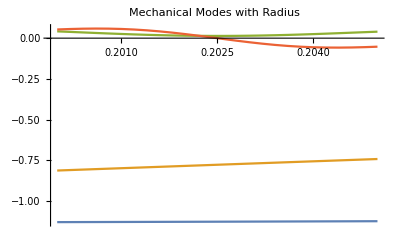

```mathematica
myplot=ListPlot[myModesr,Joined->True,PlotLabel->"Mechanical Modes with Radius",FrameLabel->{"r","displacement q"},PlotRange->All]
(*Export[StringJoin["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/radial-increases/modesm2n",ToString[mvec[[2]]],"l2.png"],myplot,"PNG"]*)
```

```mathematica
myModesr
```

{{{0.2,-1.12983},{0.2002,-1.12963},{0.2004,-1.12943},{0.2006,-1.12923},{0.2008,-1.12903},{0.201,-1.12882},{0.2012,-1.12861},{0.2014,-1.1284},10,{0.2036,-1.12588},{0.2038,-1.12563},{0.204,-1.12539},{0.2042,-1.12514},{0.2044,-1.12489},{0.2046,-1.12463},{0.2048,-1.12438},{0.205,-1.12412}},99,{1}}
 |  |  |  |

#### Make more plots of mechanical modes

```mathematica
unperturbedSphere=Table[FromSphericalCoordinates[{innerRadius,θ,ϕ}],{ϕ,0.01,2.0*Pi,0.1},{θ,0.01,Pi,0.1}];
mvec={2,0,0};
coefs={"C0","D0",0.0,0.0,"C2","D2"}/.StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]];
perturbationsToSphere=Table[spherevec2cartvec[Re[Activate[displacementVecQnotRotated[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,θ,ϕ]]],{innerRadius,θ,ϕ}],{ϕ,0.01,2.0*Pi,0.1},{θ,0.01,Pi,0.1}];
```

```mathematica
unperturbedSphere
perturbationsToSphere
```

{{{0.00199987,0.0000199993,0.19999},{0.0219546,0.000219553,0.198791},{0.0416899,0.000416913,0.195606},{0.0610087,0.000610107,0.190467},{0.0797179,0.000797205,0.183424},23,{0.0651066,0.000651088,-0.189105},{0.0459033,0.000459048,-0.19466},{0.0262413,0.000262422,-0.198271},{0.00631716,0.0000631737,-0.1999}},61,{1}}
 |  |  |  |

{1}
 |  |  |  |

```mathematica
ListPlot3D[unperturbedSphere+perturbationsToSphere,ColorFunction->"BlueGreenYellow",InterpolationOrder->3,Axes->False,Boxed->False,AspectRatio->1,PlotRange->{{-2.5,2.5},{-2.5,2.5},{-2.5,2.5}},ViewPoint->{0, -2, 0}]
```

-Graphics3D-

#### Plot electric and magnetic fields over the z=constant plane

```mathematica
m0 = 0;
n0 = 1;
p0 = 2;
par=1;
A=1.0;
radius=1.0;
theta0=Pi/4.0;
alpha =0.0;
beta = 0.0;
gamma = 0.0;
epsilon=0.00001;
transverse=0;
```

```mathematica
(* get TE electric fields *)
EfieldTEr=ParallelTable[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[electricField[A,par,transverse, m0,n0,p0,radius,Activate[wavenumberEM[ m0,n0,p0,radius,transverse]],r,theta0,ϕ,alpha,beta,gamma][[1]]]]},{r,0.01,1.0,0.05},{ϕ,-Pi*1.0+epsilon,Pi*1.0,0.1}];
EfieldTEr=ArrayFlatten[EfieldTEr,1];
p1=ListDensityPlot[EfieldTEr,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, r]^TE]];
EfieldTEθ=ParallelTable[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[electricField[A,par,transverse, m0,n0,p0,radius,Activate[wavenumberEM[ m0,n0,p0,radius,transverse]],r,theta0,ϕ,alpha,beta,gamma][[2]]]]},{r,0.01,1.0,0.05},{ϕ,-Pi+epsilon,Pi,0.1}];
EfieldTEθ=ArrayFlatten[EfieldTEθ,1];
p2=ListDensityPlot[EfieldTEθ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, θ]^TE]];
EfieldTEϕ=ParallelTable[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[electricField[A,par,transverse, m0,n0,p0,radius,Activate[wavenumberEM[ m0,n0,p0,radius,transverse]],r,theta0,ϕ,alpha,beta,gamma][[3]]]]},{r,0.01,1.0,0.05},{ϕ,-Pi+epsilon,Pi,0.1}];
EfieldTEϕ=ArrayFlatten[EfieldTEϕ,1];
p3=ListDensityPlot[EfieldTEϕ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, ϕ]^TE]];
```

```mathematica
gridTE=GraphicsGrid[{{p1,p2,p3}}]
```

-Graphics-

```mathematica
EfieldTEr=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Activate[electricFieldTEnotrotated[A,par, m0,n0,p0,radius,Activate[wavenumberTE[ m0,n0,p0,radius]],r,theta0,ϕ][[1]]]},{r,0.01,1.0,0.05},{ϕ,-Pi+epsilon,Pi,0.1}];
EfieldTEr=ArrayFlatten[EfieldTEr,1];
p1=ListDensityPlot[EfieldTEr,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, r]^TE]];
EfieldTEθ=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],electricFieldTEnotrotated[A,par, m0,n0,p0,radius,Activate[wavenumberTE[ m0,n0,p0,radius]],r,theta0,ϕ][[2]]},{r,0.01,1.0,0.05},{ϕ,-Pi+epsilon,Pi,0.1}];
EfieldTEθ=ArrayFlatten[EfieldTEθ,1];
p2=ListDensityPlot[EfieldTEθ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, θ]^TE]];
EfieldTEϕ=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[electricFieldTEnotrotated[A,par, m0,n0,p0,radius,Activate[wavenumberTE[ m0,n0,p0,radius]],r,theta0,ϕ][[3]]]]},{r,0.01,1.0,0.05},{ϕ,-Pi+epsilon,Pi,0.1}];
EfieldTEϕ=ArrayFlatten[EfieldTEϕ,1];
p3=ListDensityPlot[EfieldTEϕ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, ϕ]^TE]];
```

```mathematica
gridTE=GraphicsGrid[{{p1,p2,p3}}]
```

-Graphics-

```mathematica
BfieldTEr=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[magneticFieldTEnotrotated[A,par, m0,n0,p0,radius,Activate[wavenumberTE[ m0,n0,p0,radius]],r,theta0,ϕ][[1]]]]},{r,0.01,1.0,0.05},{ϕ,-Pi+epsilon,Pi,0.1}];
BfieldTEr=ArrayFlatten[BfieldTEr,1];
p1=ListDensityPlot[BfieldTEr,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, r]^TE]];
BfieldTEθ=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[magneticFieldTEnotrotated[A,par, m0,n0,p0,radius,Activate[wavenumberTE[ m0,n0,p0,radius]],r,theta0,ϕ][[2]]]]},{r,0.01,1.0,0.05},{ϕ,-Pi+epsilon,Pi,0.1}];
BfieldTEθ=ArrayFlatten[BfieldTEθ,1];
p2=ListDensityPlot[BfieldTEθ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, θ]^TE]];
BfieldTEϕ=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[magneticFieldTEnotrotated[A,par, m0,n0,p0,radius,Activate[wavenumberTE[ m0,n0,p0,radius]],r,theta0,ϕ][[3]]]]},{r,0.01,1.0,0.05},{ϕ,-Pi+epsilon,Pi,0.1}];
BfieldTEϕ=ArrayFlatten[BfieldTEϕ,1];
p3=ListDensityPlot[BfieldTEϕ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, ϕ]^TE]];
```

```mathematica
gridTE=GraphicsGrid[{{p1,p2,p3}}]
```

-Graphics-

```mathematica
InputForm[FromSphericalCoordinates[{r,theta,phi}]]
```

{r*Cos[phi]*Sin[theta], r*Sin[phi]*Sin[theta], r*Cos[theta]}

#### Plot vector potential in 3d

```mathematica
r=0.8;
emdata = ParallelTable[{r*Cos[phi]*Sin[theta],r*Sin[phi]*Sin[theta],r*Cos[theta],Abs[vectorPotentialTE[1.0,1,0,1,2,1.0,Activate[wavenumberEM[0,1,2,1.0,0]],r,theta,phi][[1]]]},{theta,0.01,Pi,0.1},{phi,-Pi,Pi,0.1}]
```

{{{-0.00799987,-9.79701×10^-19,0.79996,0.130906},{-0.0079599,-0.000798654,0.79996,0.130906},{-0.0078404,-0.00158933,0.79996,0.130906},57,{-0.00768123,0.00223529,0.79996,0.130906},{-0.00786602,0.00145728,0.79996,0.130906},{-0.0079722,0.000664704,0.79996,0.130906}},30,{1}}
 |  |  |  |

```mathematica
emdata=Flatten[emdata,1]
```

{{-0.00799987,-9.79701×10^-19,0.79996,0.130906},{-0.0079599,-0.000798654,0.79996,0.130906},{-0.0078404,-0.00158933,0.79996,0.130906},2010,{-0.0242634,0.00706081,-0.799601,0.130848},{-0.0248471,0.00460323,-0.799601,0.130848},{-0.0251825,0.00209966,-0.799601,0.130848}}
 |  |  |  |

```mathematica
Dimensions[emdata]
```

{2016,4}

```mathematica
m = 2;
n = 2;
p = 2;
SphericalPlot3D[{Abs[vectorPotentialTE[1.0,1,m,n,p,1.0,Activate[wavenumberEM[m,n,p,1.0,0]],0.7,theta,phi][[1]]],Abs[vectorPotentialTE[1.0,1,m,n,p,1.0,Activate[wavenumberEM[m,n,p,1.0,0]],0.8,theta,phi][[1]]],Abs[vectorPotentialTE[1.0,1,m,n,p,1.0,Activate[wavenumberEM[m,n,p,1.0,0]],0.9,theta,phi][[1]]]},{theta,0.01,Pi},{phi,0,3*Pi/2},PlotTheme->"Scientific",PlotRange->All,AspectRatio->1]
```

-Graphics3D-

#### Plot EM vector field in 3d

```mathematica
points=Table[{x,y,z,Norm[spherevec2cartvec[magneticFieldTEnotrotated[1.0,1, 0,1,2,1.0,Activate[wavenumberTE[0,1,2,0.1]],#1,#2,#3]&@@ToSphericalCoordinates[{x,y,z}], ToSphericalCoordinates[{x,y,z}]]]^2},{x,-1,1,0.2},{y,-1,1,0.2},{z,-1,1,0.2}]
```

{{{{-1.,-1.,-1.,0.0000340853},{-1.,-1.,-0.8,8.78058×10^-7},{-1.,-1.,-0.6,0.0000246473},{-1.,-1.,-0.4,0.0000135351},{-1.,-1.,-0.2,0.0000117519},{-1.,-1.,0.,0.0000343576},{-1.,-1.,0.2,0.0000117519},{-1.,-1.,0.4,0.0000135351},{-1.,-1.,0.6,0.0000246473},{-1.,-1.,0.8,8.78058×10^-7},{-1.,-1.,1.,0.0000340853}},{1},7,{1},{1}},9,{1}}
 |  |  |  |

```mathematica
ListDensityPlot3D[Flatten[points,2],PlotTheme->"Scientific"]
```

-Graphics3D-

#### Check normalization of EM modes

```mathematica
mem = 0;
nem = 1;
pem = 2;
NIntegrate[Norm[electricFieldTE[1.0,1,mem,nem,pem,innerRadius,wavenumberTE[mem,nem,pem,innerRadius],r,theta,phi]]^2*r^2*Sin[theta],{r,0.0,innerRadius},{phi,0.0,2.0*Pi},{theta,0.0,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^5]
NIntegrate[Norm[magneticFieldTE[1.0,1,mem,nem,pem,innerRadius,wavenumberTE[mem,nem,pem,innerRadius],r,theta,phi]]^2*r^2*Sin[theta],{r,0.0,innerRadius},{phi,0.0,2.0*Pi},{theta,0.0,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^5]
(4/3)*Pi*innerRadius^2
```

0.0693441

0.0680184

4.18879

```mathematica
Activate[getNormalizationFactor[1,0,1,2,1.0,0]]
```

0.068499

#### Test the EM energy function by plotting for various modes

```mathematica
TEEnergies=Table[{m,n,p,calculateEMFieldEnergy[0,1.0,0,m,n,p,1.0,wavenumberTE[m,n,p,1.0]]},{m,0,2},{n,0,2},{p,1,2}]
```

{{{{0,0,1,0.},{0,0,2,0.}},{{0,1,1,0.},{0,1,2,0.}},{{0,2,1,0.},{0,2,2,0.}}},{{{1,0,1,0.},{1,0,2,0.}},{{1,1,1,0.},{1,1,2,0.0349354}},{{1,2,1,0.},{1,2,2,0.311903}}},{{{2,0,1,0.},{2,0,2,0.}},{{2,1,1,0.},{2,1,2,0.}},{{2,2,1,0.},{2,2,2,1.22983}}}}

```mathematica
TEEnergies=Table[{m,n,p,Activate[calculateEMFieldEnergy[0,1.0,0,m,n,p,1.0,wavenumberTE[m,n,p,1.0]]]},{m,0,2},{n,0,2},{p,1,2}]
```

{{{{0,0,1,1/2 NIntegrate[r^2 Sin[θ] Norm[electricField[1.,0,0,0,0,1,1.,1. SphericalBesselJZero[0,1],r,θ,ϕ]]^2 getNormalizationFactor[0,0,0,1,1.,0,1. SphericalBesselJZero[0,1]]^2,{r,0.,1.},{θ,0.,π},{ϕ,0.,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5,PrecisionGoal→2]},{0,0,2,1/2 NIntegrate[r^2 Sin[θ] Norm[electricField[1.,0,0,0,0,2,1.,1. SphericalBesselJZero[0,2],r,θ,ϕ]]^2 getNormalizationFactor[0,0,0,2,1.,0,1. SphericalBesselJZero[0,2]]^2,{r,0.,1.},{θ,0.,π},{ϕ,0.,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5,PrecisionGoal→2]}},{{0,1,1,1/2 NIntegrate[r^2 Sin[θ] 1^2 (22[1])^2,5,PrecisionGoal→2]},{1}},{{0,2,1,1/2 NIntegrate[r^2 Sin[θ] Norm[electricField[1.,0,0,0,2,1,1.,1. SphericalBesselJZero[2,1],r,θ,ϕ]]^2 getNormalizationFactor[0,0,2,1,1.,0,1. SphericalBesselJZero[2,1]]^2,{r,0.,1.},{θ,0.,π},{ϕ,0.,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5,PrecisionGoal→2]},{0,2,2,1/2 NIntegrate[r^2 Sin[θ] Norm[electricField[1.,0,0,0,2,2,1.,1. SphericalBesselJZero[2,2],r,θ,ϕ]]^2 getNormalizationFactor[0,0,2,2,1.,0,1. SphericalBesselJZero[2,2]]^2,{r,0.,1.},{θ,0.,π},{ϕ,0.,2. π},Method→AdaptiveMonteCarlo,MaxPoints→10^5,PrecisionGoal→2]}}},{1},{1}}
 |  |  |  |

I think my indices may be off somewhere because there should be more modes with non-zero energies. Something is definitely off with the m,n indices

```mathematica
calculateEMFieldEnergy[0,1.0,1,0,1,3,1.0]
```

0.0174679

```mathematica
TMEnergies=Table[{m,n,p,calculateEMFieldEnergy[1,1.0,1,m,n,p,1.0]},{m,0,2},{n,0,2},{p,1,2}]
```

NIntegrate::inumri: The integrand … has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,1.},{0.,3.14159},{0.,6.28319}}.

$Aborted

#### Test the overlap function

```mathematica
mmech = 2;
nmech = 1;
lmech = 0;
c0mech="C0"/.(StringJoin["m",ToString[mmech],"n",ToString[nmech],"l",ToString[lmech]]/.MODES[[1]]);;
c1mech=0.0;
c2mech="C2"/.(StringJoin["m",ToString[mmech],"n",ToString[nmech],"l",ToString[lmech]]/.MODES[[1]]);
d0mech="D0"/.(StringJoin["m",ToString[mmech],"n",ToString[nmech],"l",ToString[lmech]]/.MODES[[1]]);;
d1mech=0.0;
d2mech="D2"/.(StringJoin["m",ToString[mmech],"n",ToString[nmech],"l",ToString[lmech]]/.MODES[[1]]);;
Re[NIntegrate[Activate[overlapIntegrand[{mmech,nmech,lmech},{0,1,2},{0,1,3},1.0,{c0mech,d0mech,c1mech,d1mech,c2mech,d2mech},1.0,0,0,1,1,θ,ϕ]], {θ,0.001,Pi},{ϕ,0.0,2.0*Pi}, Method->"GlobalAdaptive"]]
```

0.0128473

#### Check normalization of Mechanical Modes

```mathematica
checkNormFunction[mindices_]:=Module[{mvec=mindices,coefs},
coefs={"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]]);
NIntegrate[r^2*Sin[θ]*Norm[Quiet[Activate[displacementVecQnotRotated[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],r,θ,ϕ]]]]^2,{r,innerRadius,outerRadius},{θ,0.0,Pi},{ϕ,-Pi,Pi},Method->"MultidimensionalRule",PrecisionGoal->2]/((4/3)*Pi*(outerRadius^3-innerRadius^3))]
```

```mathematica
checkNormFunction[{2,0,2}]
```

{47.2684,0.0191611,0.,0.,3.46611,-0.127022}

0.985152

```mathematica
normChecks={};
Module[{n},For[n=0,n<=128,n++,If[Mod[n,5]==0,Print[n],Clear[x]];AppendTo[normChecks,checkNormFunction[{2,n,2}]]]]
```

0

5

10

15

20

25

30

35

40

45

50

55

60

65

70

75

80

85

90

95

100

105

110

115

120

125

```mathematica
normChecks
```

{1.,1.00002,1.,1.,1.00003,1.,1.00002,1.00002,1.,1.,1.,0.961183,1.,1.00006,1.01522,0.973424,0.999971,0.999993,0.985507,0.830637,0.999987,1.01906,0.999999,1.00004,1.,1.00171,1.,1.00005,1.00264,1.00013,1.04576,0.997033,0.960642,1.00003,1.,0.984792,1.00004,0.999999,1.00027,1.,1.00259,0.999999,0.993733,1.00004,0.999852,1.00768,1.02691,1.00001,1.00001,1.01631,1.00003,1.,1.00612,1.00005,0.999998,1.00005,1.,1.00794,1.00002,1.07026,0.998015,1.,1.00005,1.,0.994278,1.00001,1.00001,1.00508,0.999998,1.00004,1.00002,0.999726,1.0065,1.,1.00624,0.999999,0.999998,1.00032,1.,1.00189,1.00003,1.,0.993414,0.999999,1.00002,0.999849,0.997039,1.00004,1.28205,0.999304,1.02677,0.99897,0.999999,1.00646,1.00005,0.999999,1.00304,1.,1.00001,1.,1.00077,1.00003,1.00002,0.979017,1.,0.953098,1.00642,1.01077,1.00004,0.96533,1.00118,1.00004,1.,0.998372,0.999999,0.999999,1.00003,1.,0.999225,1.,1.,1.,1.,0.994733,1.00004,1.00114,0.998498,1.00004,1.}

#### Check angular momentum of modes

```mathematica
angularMomentumEM[0,1,2,innerRadius,0,1,Activate[wavenumberEM[0,1,2,innerRadius,0]],0.0,0.0,0.0]
```

{0.,7.66665×10^-21,-1.34499×10^-6}

```mathematica
"m2n0l0"/.MODES[[1]]
```

{wavenumberk→1.78981,wavenumberp→0.783212,frequency→2817.12,C0→2.18785,C2→0.0000728853,D0→0.140649,D2→-0.00167631}

```mathematica
angularMomentumMech[2,0,0,innerRadius,2.1878,0.14064,0.0,0.0,0.000072885,-0.0016763,0.0,0.0,0.0]
```

{0.,1.02023×10^-16,-369.572+1.71563×10^-14 ⅈ}

```mathematica
angularMomentumMech[2,0,0,innerRadius,2.1878,0.14064,0.0,0.0,0.000072885,-0.0016763,0.0,Pi,0.0]
```

{0.,-1.36546+7.41478×10^-17 ⅈ,14.3296}

#### Check that EM fields satisfy Maxwell’s Eqns.

```mathematica
Curl[electricFieldTE[A,p, m,n,p,a,k,r,θ,ϕ,0,0,0],{r,θ,ϕ},"Spherical"]+k*SPEEDOFLIGHT*magneticFieldTE[A,p, m,n,p,a,k,r,θ,ϕ,0,0,0]
```

{-(Csc[θ] (-(A 4 SphericalBesselJ[n,k √(r^2 Cos[θ]^2+r^2 1^2 1^2+r^2 Sin[θ]^2 Sin[ϕ]^2)])/(√(r^2 Cos[ϕ]^2 Sin[θ]^2+r^2 Sin[θ]^2 Sin[ϕ]^2))+7))/r+(Cos[ϕ] (-(A Cos[θ] 3 (1) SphericalBesselJ[n,k √1])/(2 1 √(r^2 Cos[θ]^2+r^2 1^2 1^2+r^2 Sin[θ]^2 Sin[ϕ]^2))+17)+Sin[ϕ] (1))/r+1. k (1),5+1. k (1-1+Cos[θ] 1 ((A 4 SphericalBesselJ[n,1])/(k (1+1))+1-1/1)),1}
 |  |  |  |

```mathematica
Simplify[%]
```

$Aborted

#### Just check on the index stuff

```mathematica
Simplify[electricField[Subscript[E, 0],1,0, m,n,p,a,k,r,θ,ϕ,0,0,0][[3]]]//TraditionalForm
```

-(ⅇ_0 nk √(r^2) ((n+1) r cos(θ) nm(r cos(θ))/(√(r^2))+√(r^2) (m-n-1) n+1m(r cos(θ))/(√(r^2))) cos(m tan^-1(r sin(θ) cos(ϕ),r sin(θ) sin(ϕ))))/(√(r^2 sin^2(θ)))

```mathematica
Simplify[D[LegendreP[n,m,Cos[θ]],θ]]//TraditionalForm
```

-csc(θ) ((n+1) cos(θ) nmcos(θ)+(m-n-1) n+1mcos(θ))

#### Check vector coordinate conversions

```mathematica
myVectorField=Table[{{x,y,z},{x,y,z}},{x,-1,1,0.1},{y,-1,1,0.1},{z,-1,1,0.1}];
ListVectorPlot3D[myVectorField]
```

-Graphics3D-

```mathematica
myVectorFieldSpherical=Table[{ToSphericalCoordinates[{x,y,z}],cartvec2spherevec[{x,y,z},ToSphericalCoordinates[{x,y,z}]]},{x,-1,1,0.1},{y,-1,1,0.1},{z,-1,1,0.1}];
```

```mathematica
myVectorFieldSpherical
```

{{{{{1.73205,2.18628,-2.35619},{1.73205,0.,-1.11022×10^-16}},{{1.67631,2.13755,-2.35619},{1.67631,2.22045×10^-16,-1.11022×10^-16}},17,{{1.67631,1.00404,-2.35619},{1.67631,1.11022×10^-16,-1.11022×10^-16}},{{1.73205,0.955317,-2.35619},{1.73205,0.,-1.11022×10^-16}}},{{{1},{1}},20},17,{1},{1}},20}
 |  |  |  |

```mathematica
myvec={1,0,0};
p={1,Pi/2,Pi/2};
cartvec2spherevec[myvec,p]
```

{0,0,-1}

Limited testing, but it seems like it works.

#### Plot inner displacement with n

```mathematica
rdisplacements={};
Module[{n},For[n=0,n<=10,n++,mvec={2,n,2};
z=0.1;
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
AppendTo[rdisplacements,Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,Pi/2,0.0,0.0,0.0,0.0][[1]]]]]]];
```

```mathematica
rdisplacements=Delete[rdisplacements,8]
```

{0.920987,0.66523,-0.0339671,-0.0437955,{{0.+1. (0.+1. (0.+0.00418444 (2.13522+Re[0.0387283 LinearSolve[LinearSolveFunction[{4,3},{2,False,{{{0.000117255,0.00774288,-0.0000330043},{0.000863172,1.58824×10^-6,0.0030666},{-9.6323×10^-6,-0.00793656,-0.000127615},{0.00325614,-1.6688×10^-6,-0.00024577}}},{0,Automatic,Automatic},0}],LinearSolveFunction[{4,1},{2,False,{{{0.000527448},{-0.0000202401},{-0.000538644},{0.0000212648}}},{0,Automatic,Automatic},0}]]-0.00319726 Flatten[LinearSolve[LinearSolveFunction[{4,3},{2,False,{{{0.000117255,0.00774288,-0.0000330043},{0.000863172,1.58824×10^-6,0.0030666},{-9.6323×10^-6,-0.00793656,-0.000127615},{0.00325614,-1.6688×10^-6,-0.00024577}}},{0,Automatic,Automatic},0}],LinearSolveFunction[{4,1},{2,False,{{{0.000527448},{-0.0000202401},{-0.000538644},{0.0000212648}}},{0,Automatic,Automatic},0}]],{{1,2}}]⟦3⟧]))),0.+1. (0.+1. (0.+0.00418444 (2.27385+Re[0.0387283 LinearSolve[LinearSolveFunction[{4,3},{2,False,{{{0.000117255,0.00774288,-0.0000330043},{0.000863172,1.58824×10^-6,0.0030666},{-9.6323×10^-6,-0.00793656,-0.000127615},{0.00325614,-1.6688×10^-6,-0.00024577}}},{0,Automatic,Automatic},0}],LinearSolveFunction[{4,1},{2,False,{{{0.000527448},{-0.0000202401},{-0.000538644},{0.0000212648}}},{0,Automatic,Automatic},0}]]-0.00319726 Flatten[LinearSolve[LinearSolveFunction[{4,3},{2,False,{{{0.000117255,0.00774288,-0.0000330043},{0.000863172,1.58824×10^-6,0.0030666},{-9.6323×10^-6,-0.00793656,-0.000127615},{0.00325614,-1.6688×10^-6,-0.00024577}}},{0,Automatic,Automatic},0}],LinearSolveFunction[{4,1},{2,False,{{{0.000527448},{-0.0000202401},{-0.000538644},{0.0000212648}}},{0,Automatic,Automatic},0}]],{{1,2}}]⟦3⟧])))}},-0.00284991,0.00389576,0.0614708,0.00373115,-0.000524587}

#### Plot spherical vector field

```mathematica
(* write a function that plots a spherical vector field in cartesian coordinates *)
```

```mathematica
(* make a table of the spherical vectors in a spherical coordinate spacing *)
r0=0.2;
vectorsAndPoints=Table[{FromSphericalCoordinates[{r,θ,ϕ}],spherevec2cartvec[Re[Activate[displacementVecQnotRotated[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],r,θ,ϕ]]],{r,θ,ϕ}]},{r,innerRadius,outerRadius,0.003},{θ,0.01,Pi,0.7},{ϕ,-Pi+0.01,Pi,0.7}];
```

```mathematica
(* convert all points to cartesian and all vectors to cartesian *)
cartTable={};
Module[{i},For[i=1,i<=Length[vectorsAndPoints],i++,AppendTo[cartTable,{FromSphericalCoordinates[vectorsAndPoints[[i,1]]],spherevec2cartvec[vectorsAndPoints[[i,2]],vectorsAndPoints[[i,1]]]}]]]
```

```mathematica
cartTable
```

{{{-0.00199987,-0.0000199993,0.19999},{0.00239938,0.0000239946,-1.84177}},{{-0.00198788,-0.000219553,0.19999},{0.002385,0.000263413,-1.84177}},2012,{{-0.00622298,0.00108863,-0.1999},{0.00743372,-0.00130044,1.8399}},{{-0.00630057,0.000461934,-0.1999},{0.00752641,-0.000551808,1.8399}}}
 |  |  |  |

```mathematica
(* plot these vectors *)
ListVectorPlot3D[vectorsAndPoints]
```

ListVectorPlot3D[{{{{{-0.00199987,-0.0000199993,0.19999},{0.00239938,0.0000239946,-1.84177}},{{-0.0015167,-0.00130365,0.19999},{0.00181969,0.00156408,-1.84177}},{{-0.000320203,-0.00197417,0.19999},{0.000384171,0.00236855,-1.84177}},{{0.00102689,-0.00171621,0.19999},{-0.00123203,0.00205906,-1.84177}},{{0.00189102,-0.000651088,0.19999},{-0.00226879,0.000781157,-1.84177}},{{0.00186577,0.000720248,0.19999},{-0.0022385,-0.000864133,-1.84177}},{{0.000963025,0.00175284,0.19999},{-0.00115541,-0.00210301,-1.84177}},{{-0.000392648,0.00196104,0.19999},{0.000471088,-0.00235281,-1.84177}},{{-0.00156365,0.00124694,0.19999},{0.00187603,-0.00149604,-1.84177}}},{{{-0.13036,-0.00130365,0.151672},{-0.165067,-0.00165073,-1.02277}},{{-0.0988652,-0.0849775,0.151672},{-0.125187,-0.107602,-1.02277}},{{-0.0208723,-0.128685,0.151672},{-0.0264293,-0.162946,-1.02277}},{{0.0669372,-0.11187,0.151672},{0.0847586,-0.141654,-1.02277}},{{0.123265,-0.0424408,0.151672},{0.156083,-0.0537403,-1.02277}},{{0.121619,0.046949,0.151672},{0.153999,0.0594487,-1.02277}},{{0.0627743,0.114258,0.151672},{0.0794873,0.144678,-1.02277}},{{-0.0255946,0.12783,0.151672},{-0.0324089,0.161863,-1.02277}},{{-0.101926,0.081281,0.151672},{-0.129063,0.102921,-1.02277}}},{{{-0.19741,-0.00197417,0.0320209},{-0.879684,-0.00879714,-0.113783}},{{-0.149716,-0.128685,0.0320209},{-0.667152,-0.573437,-0.113783}},{{-0.0316078,-0.194873,0.0320209},{-0.140848,-0.86838,-0.113783}},{{0.101366,-0.16941,0.0320209},{0.451699,-0.754911,-0.113783}},{{0.186666,-0.06427,0.0320209},{0.831805,-0.286395,-0.113783}},{{0.184174,0.0710969,0.0320209},{0.8207,0.316817,-0.113783}},{{0.0950618,0.173026,0.0320209},{0.423607,0.771025,-0.113783}},{{-0.038759,0.193578,0.0320209},{-0.172715,0.862607,-0.113783}},{{-0.154351,0.123087,0.0320209},{-0.687807,0.548493,-0.113783}}},{{{-0.171615,-0.00171621,-0.102691},{-0.527624,-0.00527642,0.506783}},{{-0.130153,-0.11187,-0.102691},{-0.40015,-0.343941,0.506783}},{{-0.0274777,-0.16941,-0.102691},{-0.0844791,-0.520844,0.506783}},{{0.0881206,-0.147273,-0.102691},{0.270924,-0.452786,0.506783}},{{0.162274,-0.0558719,-0.102691},{0.498907,-0.171776,0.506783}},{{0.160108,0.0618068,-0.102691},{0.492246,0.190023,0.506783}},{{0.0826403,0.150417,-0.102691},{0.254075,0.462451,0.506783}},{{-0.0336944,0.168283,-0.102691},{-0.103592,0.517382,0.506783}},{{-0.134182,0.107004,-0.102691},{-0.412538,0.328979,0.506783}}},{{{-0.0651066,-0.000651088,-0.189105},{0.0380935,0.000380948,1.62528}},{{-0.0493768,-0.0424408,-0.189105},{0.0288901,0.0248319,1.62528}},{{-0.0104244,-0.06427,-0.189105},{0.00609924,0.037604,1.62528}},{{0.0334308,-0.0558719,-0.189105},{-0.0195602,0.0326903,1.62528}},{{0.061563,-0.0211965,-0.189105},{-0.0360202,0.0124019,1.62528}},{{0.0607411,0.023448,-0.189105},{-0.0355393,-0.0137193,1.62528}},{{0.0313517,0.0570645,-0.189105},{-0.0183437,-0.0333881,1.62528}},{{-0.0127829,0.0638427,-0.189105},{0.00747917,-0.037354,1.62528}},{{-0.0509055,0.0405947,-0.189105},{0.0297845,-0.0237517,1.62528}}}},{{{{-0.00202986,-0.0000202993,0.20299},{0.00293351,0.0000293361,-1.83649}},{{-0.00153945,-0.0013232,0.20299},{0.00222477,0.00191226,-1.83649}},{{-0.000325006,-0.00200378,0.20299},{0.000469691,0.00289581,-1.83649}},{{0.00104229,-0.00174195,0.20299},{-0.00150629,0.00251742,-1.83649}},{{0.00191938,-0.000660854,0.20299},{-0.00277385,0.00095505,-1.83649}},{{0.00189376,0.000731052,0.20299},{-0.00273681,-0.0010565,-1.83649}},{{0.000977471,0.00177913,0.20299},{-0.00141262,-0.00257116,-1.83649}},{{-0.000398538,0.00199046,0.20299},{0.000575957,-0.00287656,-1.83649}},{{-0.00158711,0.00126564,0.20299},{0.00229365,-0.00182907,-1.83649}}},{{{-0.132316,-0.0013232,0.153947},{-0.144312,-0.00144317,-1.00241}},{{-0.100348,-0.0862521,0.153947},{-0.109446,-0.0940721,-1.00241}},{{-0.0211854,-0.130615,0.153947},{-0.0231061,-0.142458,-1.00241}},{{0.0679412,-0.113548,0.153947},{0.0741011,-0.123843,-1.00241}},{{0.125114,-0.0430774,0.153947},{0.136457,-0.046983,-1.00241}},{{0.123444,0.0476532,0.153947},{0.134636,0.0519737,-1.00241}},{{0.0637159,0.115972,0.153947},{0.0694927,0.126486,-1.00241}},{{-0.0259785,0.129747,0.153947},{-0.0283338,0.141511,-1.00241}},{{-0.103455,0.0825002,0.153947},{-0.112834,0.0899801,-1.00241}}},{{{-0.200371,-0.00200378,0.0325012},{-0.875798,-0.00875827,-0.105016}},{{-0.151962,-0.130615,0.0325012},{-0.664205,-0.570903,-0.105016}},{{-0.0320819,-0.197796,0.0325012},{-0.140226,-0.864543,-0.105016}},{{0.102886,-0.171951,0.0325012},{0.449703,-0.751575,-0.105016}},{{0.189466,-0.065234,0.0325012},{0.82813,-0.28513,-0.105016}},{{0.186936,0.0721633,0.0325012},{0.817075,0.315417,-0.105016}},{{0.0964878,0.175621,0.0325012},{0.421736,0.767618,-0.105016}},{{-0.0393403,0.196482,0.0325012},{-0.171952,0.858796,-0.105016}},{{-0.156666,0.124934,0.0325012},{-0.684768,0.546069,-0.105016}}},{{{-0.174189,-0.00174195,-0.104231},{-0.513874,-0.00513891,0.484875}},{{-0.132105,-0.113548,-0.104231},{-0.389722,-0.334977,0.484875}},{{-0.0278898,-0.171951,-0.104231},{-0.0822776,-0.50727,0.484875}},{{0.0894424,-0.149482,-0.104231},{0.263863,-0.440987,0.484875}},{{0.164708,-0.05671,-0.104231},{0.485905,-0.1673,0.484875}},{{0.16251,0.0627339,-0.104231},{0.479418,0.185071,0.484875}},{{0.0838799,0.152673,-0.104231},{0.247453,0.4504,0.484875}},{{-0.0341998,0.170808,-0.104231},{-0.100893,0.503898,0.484875}},{{-0.136195,0.108609,-0.104231},{-0.401787,0.320406,0.484875}}},{{{-0.0660832,-0.000660854,-0.191942},{0.0537318,0.000537335,1.61521}},{{-0.0501175,-0.0430774,-0.191942},{0.0407502,0.0350259,1.61521}},{{-0.0105807,-0.065234,-0.191942},{0.00860312,0.0530413,1.61521}},{{0.0339323,-0.05671,-0.191942},{-0.0275901,0.0461105,1.61521}},{{0.0624865,-0.0215144,-0.191942},{-0.0508073,0.0174932,1.61521}},{{0.0616522,0.0237997,-0.191942},{-0.050129,-0.0193514,1.61521}},{{0.031822,0.0579205,-0.191942},{-0.0258742,-0.0470947,1.61521}},{{-0.0129746,0.0648004,-0.191942},{0.0105495,-0.0526887,1.61521}},{{-0.0516691,0.0412036,-0.191942},{0.0420117,-0.0335023,1.61521}}}}}]

```mathematica
vectorsAndPoints=Table[spherevec2cartvec[Re[Activate[displacementVecQnotRotated[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],#1,#2,#3]]],{#1,#2,#3}]&@@ToSphericalCoordinates[{x0,y0,z0}],{x0,-2,2},{y0,-2,2},{z0,-2,2}];
```

```mathematica
vectorsAndPoints
```

{1}
 |  |  |  |

```mathematica
ListSliceVectorPlot3D[vectorsAndPoints,ImplicitRegion[x^2+y^2+z^2==1^2,{x,y,z}],DataRange->{{-2,2},{-2,2},{-2,2}}]
```

-Graphics3D-

#### Look at em fields

```mathematica
?electricField
```

```mathematica
?wavenumberEM
```

```mathematica
Simplify[Norm[magneticField[1,1,0,0,1,2,a,k,r,θ,ϕ,0,0,0]]^2,Assumptions->{r>0,k>0}]//MatrixForm
Simplify[Norm[magneticField[1,1,0,1,1,2,a,k,r,θ,ϕ,0,0,0]]^2,Assumptions->{r>0}]//MatrixForm
(*Simplify[Activate[magneticField[fnlm,1,0,0,1,2,a,wavenumberEM[0,1,2,a,0],r,θ,ϕ,0,0,0]],Assumptions->{r>0}]//MatrixForm*)
```

4 Abs[(Cos[θ] SphericalBesselJ[1,k r])/(k r)]^2+1/4 Abs[(Sin[θ] (k r SphericalBesselJ[0,k r]+SphericalBesselJ[1,k r]-k r SphericalBesselJ[2,k r]))/(k r)]^2

1/4 (16 Abs[(Cos[ϕ] Sin[θ] SphericalBesselJ[1,k r])/(k r)]^2+Abs[(Cos[θ] Cos[ϕ] (k r SphericalBesselJ[0,k r]+SphericalBesselJ[1,k r]-k r SphericalBesselJ[2,k r]))/(k r)]^2+Abs[(Sin[ϕ] (k r SphericalBesselJ[0,k r]+SphericalBesselJ[1,k r]-k r SphericalBesselJ[2,k r]))/(k r)]^2)

```mathematica
Simplify[magneticField[1,1,0,0,1,2,a,k,r,θ,ϕ,0,0,0],Assumptions->{r>0,k>0}]//MatrixForm
Simplify[magneticField[1,1,0,0,1,2,a,k,r,θ,ϕ,0,-Pi/2,0],Assumptions->{r>0,k>0}]//MatrixForm
Simplify[magneticField[1,1,0,1,1,2,a,k,r,θ,ϕ,0,0,0],Assumptions->{r>0}]//MatrixForm
```

((2 Cos[θ] SphericalBesselJ[1,k r])/(k r)
-(Sin[θ] (k r SphericalBesselJ[0,k r]+SphericalBesselJ[1,k r]-k r SphericalBesselJ[2,k r]))/(2 k r)
0)

(-(2 Cos[ϕ] Sin[θ] SphericalBesselJ[1,k r])/(k r)
-(Cos[θ] Cos[ϕ] (k r SphericalBesselJ[0,k r]+SphericalBesselJ[1,k r]-k r SphericalBesselJ[2,k r]))/(2 k r)
(Sin[ϕ] (k r SphericalBesselJ[0,k r]+SphericalBesselJ[1,k r]-k r SphericalBesselJ[2,k r]))/(2 k r))

(-(2 Cos[ϕ] Sin[θ] SphericalBesselJ[1,k r])/(k r)
-(Cos[θ] Cos[ϕ] (k r SphericalBesselJ[0,k r]+SphericalBesselJ[1,k r]-k r SphericalBesselJ[2,k r]))/(2 k r)
(Sin[ϕ] (k r SphericalBesselJ[0,k r]+SphericalBesselJ[1,k r]-k r SphericalBesselJ[2,k r]))/(2 k r))

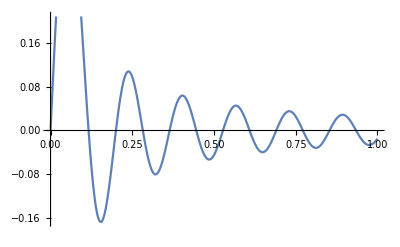

```mathematica
Plot[SphericalBesselJ[1,7.72525*x/0.2],{x,0,1}]
```

```mathematica
FullSimplify[Norm[Simplify[Activate[electricField[1.0,1,0,0,2,2,0.2,wavenumberEM[0,2,2,0.2,0],r,θ,ϕ,0,a,0]],Assumptions->{r>0}]]]
```

√(9. Abs[(1. Cos[θ] Cos[ϕ] Sin[a]-1. Cos[a] Sin[θ]) (Cos[a] Cos[θ]+Cos[ϕ] Sin[a] Sin[θ]) SphericalBesselJ[2,28.8173 r]]^2+9. Abs[Sin[a] (Cos[a] Cos[θ]+Cos[ϕ] Sin[a] Sin[θ]) Sin[ϕ] SphericalBesselJ[2,28.8173 r]]^2)

```mathematica
Simplify[Cos[t]*Sin[a]*Sin[t]^2*Sin[p]/Sqrt[1-(Cos[a]*Cos[t]-Cos[p]*Sin[a]*Sin[t])^2]]
```

(Cos[t] Sin[a] Sin[p] Sin[t]^2)/(√(1-(Cos[a] Cos[t]-Cos[p] Sin[a] Sin[t])^2))

```mathematica
Activate[wavenumberEM[0,2,2,1.0,0]]
wavenumberEM[0,1,2,1.0,0]
```

5.76346

1. SphericalBesselJZero[1,2]

```mathematica
5.7634592/0.2
```

28.8173

```mathematica
Simplify[Activate[electricField[fnlm,1,0,1,2,2,0.2,wavenumberEM[0,2,2,0.2,0],r,θ,ϕ,0,0,0]],Assumptions->{r>0}]//MatrixForm
```

(0
-3 fnlm Cos[θ] Sin[ϕ] SphericalBesselJ[2,28.8173 r]
-3 fnlm Cos[2 θ] Cos[ϕ] SphericalBesselJ[2,28.8173 r])

```mathematica
Simplify[Activate[magneticField[fnlm,1,0,0,1,2,a,wavenumberEM[0,1,2,a,0],r,θ,ϕ,0,0,0]]]
```

{fnlm Cos[θ] Sin[θ]^6 ((-5.74854×10^-17 Cos[ϕ]^4 Cot[θ]^2 Sin[ϕ]^2-5.74854×10^-17 Cos[ϕ]^2 Cot[θ]^2 Sin[ϕ]^4+3.59284×10^-18 Sin[2 ϕ]^4) SphericalBesselJ[0,(7.72525 √(r^2))/a]+(a (0.258891 Cos[ϕ]^8+7+0.0970842 1^4) SphericalBesselJ[1,(7.72525 √(r^2))/a])/(√(r^2))+(5.74854×10^-17 Cos[ϕ]^4 Cot[θ]^2 Sin[ϕ]^2+5.74854×10^-17 Cos[ϕ]^2 Cot[θ]^2 Sin[ϕ]^4-3.59284×10^-18 Sin[2 ϕ]^4) SphericalBesselJ[2,(7.72525 √(r^2))/a]),fnlm (-0.5 Sin[θ] SphericalBesselJ[0,(7.72525 √(r^2))/a]+1/(√(r^2))+0.5 Sin[θ] SphericalBesselJ[2,1/a]),0.}
 |  |  |  |

Calculate Some Realistic Form Factors

```mathematica
overlapfunction[{2,0,0,0,1,2,0,1,2},innerRadius,0,0,1,1,Activate[wavenumberEM[0,1,2,innerRadius,0]],Activate[wavenumberEM[0,1,2,innerRadius,0]],Activate[omegaEM[0,1,2,innerRadius,0]],Activate[omegaEM[0,1,2,innerRadius,0]],{0,0,0,0,0,0}]//AbsoluteTiming
overlapfunctionParallel[{2,0,0,0,1,2,0,1,2},innerRadius,0,0,1,1,Activate[wavenumberEM[0,1,2,innerRadius,0]],Activate[wavenumberEM[0,1,2,innerRadius,0]],Activate[omegaEM[0,1,2,innerRadius,0]],Activate[omegaEM[0,1,2,innerRadius,0]],{0,0,0,0,0,0}]//AbsoluteTiming
```

{0.000095,overlapfunction[{2,0,0,0,1,2,0,1,2},0.2,0,0,1,1,38.6263,38.6263,38.6263,38.6263,{0,0,0,0,0,0}]}

{0.000051,overlapfunctionParallel[{2,0,0,0,1,2,0,1,2},0.2,0,0,1,1,38.6263,38.6263,38.6263,38.6263,{0,0,0,0,0,0}]}

```mathematica
"m2n1l0"/.MODES[[1]]
```

{wavenumberk→5.2182,wavenumberp→2.28346,frequency→4810.18,C0→2.74226,C2→0.913666,D0→-0.454449,D2→0.699394}

```mathematica
overlap1Sphere2Modes[{2,0,0,0,1,2,0,1,2},innerRadius,0,0,1,1,{0,0,0,0,0,0}]//AbsoluteTiming
```

{6.35319,-1.16623}

Radiation Pressure at the Surface

```mathematica
poyntingVector[amplitude_,parity_,TMorTE_, m_,n_,p_,a_,k_,θ_,ϕ_]:=Cross[electricField[amplitude,parity,TMorTE, m,n,p,a,k,a,θ,ϕ,0.0,0.0,0.0],magneticField[amplitude,parity,TMorTE, m,n,p,a,k,a,θ,ϕ,0.0,0.0,0.0]]
cosOfAngleOfIncidence4Radiation[amplitude_,parity_,TMorTE_, m_,n_,p_,a_,k_,θ_,ϕ_]:=poyntingVector[amplitude,parity,TMorTE, m,n,p,a,k,θ,ϕ].{1,0,0}/Norm[poyntingVector[amplitude,parity,TMorTE, m,n,p,a,k,θ,ϕ]]
radiationPressure[amplitude_,parity_,TMorTE_, m_,n_,p_,a_,k_,θ_,ϕ_]:=Norm[poyntingVector[amplitude,parity,TMorTE, m,n,p,a,k,θ,ϕ]]*cosOfAngleOfIncidence4Radiation[amplitude,parity,TMorTE, m,n,p,a,k,θ,ϕ]^2/2
```

```mathematica
NIntegrate[radiationPressure[1.0,1,1,0,1,2,innerRadius,wavenumberEM[0,1,2,innerRadius,0],θ,ϕ]*innerRadius^2*Sin[θ],{θ,0.01,Pi},{ϕ,-Pi+0.01,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^4,PrecisionGoal->2]
```

2.53999×10^-9

# Double Spherical Shell Mechanical-EM Coupling

Calculate shifted frequencies for doubled up modes coupled at antipodal points

F is equivalent to vectorPotentialTE, so we just need to figure out where to cavities are being coupled. They don’t necessarily need to be coupled at a point where the fields are identical. In fact, we probably don’t want them to be identical in general. We’ll try antipodal points for now. Cavity 1 will be connected to cavity 2 at (r1=a, θ1=pi/2, ϕ1=0), (r2=a, θ1=pi/2, ϕ1=pi). The hole will be of size d << a, and the volume of each cavity will be (4/3) Pi a^3. Now use eqs. (78, 78a) from the Bethe paper.

#### Define the vector potentials

```mathematica
couplingPoints={{innerRadius,Pi/2.0,Pi},{innerRadius,Pi/2.0,0.0}};
```

```mathematica
Fpotential[amplitude_,parity_,tmorte_, m_,n_,p_,a_,k_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=(1/(omegaEM[m,n,p,a,tmorte]))*magneticField[amplitude,parity,tmorte, m,n,p,a,k,r,θ,ϕ,ang1,ang2,ang3]
garbageVariableUsedToDefineFunctions=(1/(k))*electricField[amplitude,parity,tmorte,m0,n0,p0,a,k,r,θ,ϕ,ang1,ang2,ang3];
Apotential[amplitude_,parity_,tmorte_, m0_,n0_,p0_,a_,k_,r_,θ_,ϕ_,ang1_,ang2_,ang3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
```

#### Calculate the splitting functions

```mathematica
garbageVariableUsedToDefineFunctions=2*Norm[Fpotential[amplitude,parity,tmorte,m0,n0,p0,a,k,#1,#2,#3,offsets[[4]],offsets[[5]],offsets[[6]]]&@@couplingPoints[[1]]]^2-(Apotential[amplitude,parity,tmorte,m0,n0,p0,a,k,#1,#2,#3,offsets[[4]],offsets[[5]],offsets[[6]]][[1]]&@@couplingPoints[[1]])^2;
cαα[amplitude_,parity_,tmorte_, m0_,n0_,p0_,a_,k_,offsets_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions];

garbageVariableUsedToDefineFunctions=2*Norm[Fpotential[amplitude,parity,tmorte,m0,n0,p0,a,k,#1,#2,#3,offsets[[7]],offsets[[8]],offsets[[9]]]&@@couplingPoints[[2]]]^2-(Apotential[amplitude,parity,tmorte,m0,n0,p0,a,k,#1,#2,#3,offsets[[7]],offsets[[8]],offsets[[9]]][[1]]&@@couplingPoints[[2]])^2;
cββ[amplitude_,parity_,tmorte_, m0_,n0_,p0_,a_,k_,offsets_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions];

garbageVariableUsedToDefineFunctions=2*(Fpotential[amplitude,parity,tmorte,m0,n0,p0,a,k,#1,#2,#3,offsets[[4]],offsets[[5]],offsets[[6]]]&@@couplingPoints[[1]]).(Fpotential[amplitude,parity,tmorte,m0,n0,p0,a,k,#1,#2,#3,offsets[[7]],offsets[[8]],offsets[[9]]]&@@couplingPoints[[2]])-(Apotential[amplitude,parity,tmorte,m0,n0,p0,a,k,#1,#2,#3,offsets[[7]],offsets[[8]],offsets[[9]]][[1]]&@@couplingPoints[[2]])*(Apotential[amplitude,parity,tmorte,m0,n0,p0,a,k,#1,#2,#3,offsets[[6]],offsets[[7]],offsets[[8]]][[1]]&@@couplingPoints[[1]]);
cαβ[amplitude_,parity_,tmorte_, m0_,n0_,p0_,a_,k_,offsets_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions];
```

```mathematica
(* solve for the frequency shift from quadratic *)
garbageVariableUsedToDefineFunctions=(( 2 - (4/3)*(d^3/V)*(cαα[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]+cββ[amplitude,parity,tmorte,m0,n0,p0,a,k,offsets]))/2 + (1/2)*(( 2 - (4/3)*(d^3/V)*(cαα[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]+cββ[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]))^2 - 4*(1 - (4/3)*(d^3/V)*(cαα[amplitude,parity,tmorte,m0,n0,p0,a,k,offsets]+cββ[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]) + (16/9)*(d^6/V^2)*(cαα[amplitude,parity,tmorte,m0,n0,p0,a,k,offsets]*cββ[amplitude,parity,tmorte,m0,n0,p0,a,k,offsets]-cαβ[amplitude,parity,tmorte,m0,n0,p0,a,k,offsets]^2)))^(1/2));
frequencyCoefPlus[amplitude_,parity_,tmorte_, m0_,n0_,p0_,a_,k_,d_,V_,offsets_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions];

garbageVariableUsedToDefineFunctions=(( 2 - (4/3)*(d^3/V)*(cαα[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]+cββ[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]))/2 - (1/2)*(( 2 - (4/3)*(d^3/V)*(cαα[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]+cββ[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]))^2 - 4*(1 - (4/3)*(d^3/V)*(cαα[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]+cββ[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]) + (16/9)*(d^6/V^2)*(cαα[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]*cββ[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]-cαβ[amplitude,parity,tmorte, m0,n0,p0,a,k,offsets]^2)))^(1/2));
frequencyCoefMinus[amplitude_,parity_,tmorte_, m0_,n0_,p0_,a_,k_,d_,V_,offsets_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions];
```

```mathematica
getShiftedFrequencies[amplitude_,parity_,tmorte_,m_,n_,p_,a_,d_,offsets_]:=Activate[omegaEM[m,n,p,a,tmorte]*{frequencyCoefPlus[amplitude,parity,tmorte, m,n,p,a,wavenumberEM[m,n,p,a,tmorte],d,(4.0/3.0)*Pi*a^3,offsets],frequencyCoefMinus[amplitude,parity,tmorte, m,n,p,a,wavenumberEM[m,n,p,a,tmorte],d,(4.0/3.0)*Pi*a^3,offsets] }]
```

```mathematica
Activate[getShiftedFrequencies[1.0,0,1,0,1,2,0.2,0.01,{0.0,Pi/6.0,0.0,0.0,-Pi/4.0,0.0,0.0,Pi/4.0,0.0}]]
```

{13.7185,13.7185}

Calculate overlap for 2 coupled spheres

```mathematica
overlapCoupledSpheresArtificialSplitting[modes_,a_,TMorTEFeild_,parityOfField_,d_,offsets_,splitting_]:=overlapfunction[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild],
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild],
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[4]],offsets[[5]],offsets[[6]],offsets[[4]],offsets[[5]],offsets[[6]]},1.0]+overlapfunction[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild],
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild],
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[7]],offsets[[8]],offsets[[9]],offsets[[7]],offsets[[8]],offsets[[9]]},-1.0]

overlapCoupledSpheresArtificialSplittingGlobalAdaptive[modes_,a_,TMorTEFeild_,parityOfField_,d_,offsets_,splitting_]:=overlapfunctionGlobalAdaptive[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]-splitting,
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]-splitting,
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[4]],offsets[[5]],offsets[[6]],offsets[[4]],offsets[[5]],offsets[[6]]},1]+overlapfunctionGlobalAdaptive[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]-splitting,
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]-splitting,
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[7]],offsets[[8]],offsets[[9]],offsets[[7]],offsets[[8]],offsets[[9]]},-1]

overlapCoupledSpheresArtificialSplittingTrap[modes_,a_,TMorTEFeild_,parityOfField_,d_,offsets_,splitting_]:=overlapfunctionTrap[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]-splitting,
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]-splitting,
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[4]],offsets[[5]],offsets[[6]],offsets[[4]],offsets[[5]],offsets[[6]]},1]+overlapfunctionTrap[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]-splitting,
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]-splitting,
wavenumberEM[modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeild]+splitting,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[7]],offsets[[8]],offsets[[9]],offsets[[7]],offsets[[8]],offsets[[9]]},-1]

overlapCoupledSpheres[modes_,a_,TMorTEFeild_,parityOfField_,d_,offsets_]:=(overlapfunction[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,#2/SPEEDOFLIGHT,
#1/SPEEDOFLIGHT,#2,#1,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[4]],offsets[[5]],offsets[[6]],offsets[[4]],offsets[[5]],offsets[[6]]},1]+overlapfunction[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,#2/SPEEDOFLIGHT,
#1/SPEEDOFLIGHT,#2,#1,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[7]],offsets[[8]],offsets[[9]],offsets[[7]],offsets[[8]],offsets[[9]]},-1])&@@getShiftedFrequencies[1.0,parityOfField,TMorTEFeild,modes[[4]],modes[[5]],modes[[6]],a,d,offsets]

overlapCoupledSpheresPrintSplitting[modes_,a_,TMorTEFeild_,parityOfField_,d_,offsets_]:={(overlapfunction[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,#2/SPEEDOFLIGHT,
#1/SPEEDOFLIGHT,#2,#1,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[4]],offsets[[5]],offsets[[6]],offsets[[4]],offsets[[5]],offsets[[6]]},1]+overlapfunction[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeild,TMorTEFeild,parityOfField,parityOfField,#2/SPEEDOFLIGHT,
#1/SPEEDOFLIGHT,#2,#1,{offsets[[1]],offsets[[2]],offsets[[3]],offsets[[7]],offsets[[8]],offsets[[9]],offsets[[7]],offsets[[8]],offsets[[9]]},-1])&@@getShiftedFrequencies[1.0,parityOfField,TMorTEFeild,modes[[4]],modes[[5]],modes[[6]],a,d,offsets],getShiftedFrequencies[1.0,parityOfField,TMorTEFeild,modes[[4]],modes[[5]],modes[[6]],a,d,offsets]}
```

```mathematica
overlapCoupledSpheresArtificialSplitting[{2,0,0,0,1,2},innerRadius,0,1,0.1,{0.,0.0,0.0,0.,0.0,0.,0.,0.0,0.},0.0033]//AbsoluteTiming
overlapCoupledSpheresArtificialSplitting[{2,0,0,0,1,2},innerRadius,0,1,0.1,{0.,0.0,0.0,0.,0.0,0.,0.,Pi,0.},0.0033]//AbsoluteTiming
overlapCoupledSpheresArtificialSplitting[{2,0,0,0,1,2},innerRadius,0,1,0.1,{0.,0.0,0.0,0.,-Pi/4.0,0.,0.,Pi/4.0,0.},0.0033]//AbsoluteTiming
```

{14.5343,0.0340425}

{18.0273,0.0222065}

{51.6499,-0.00569141}

```mathematica
overlapCoupledSpheresArtificialSplitting[{2,0,0,0,1,2},innerRadius,0,1,0.1,{0.,Pi/4.0,0.0,0.,-Pi/4.0,0.,0.,Pi/4.0,0.},0.0033]//AbsoluteTiming
```

{41.0002,-1.77559}

```mathematica
overlapCoupledSpheresArtificialSplitting[{2,0,0,0,1,2},innerRadius,0,1,0.1,{Pi/4.0,Pi/4.0,0.0,0.,-Pi/4.0,0.,0.,Pi/4.0,0.},0.0033]//AbsoluteTiming
```

{39.8423,-1.79707}

Results imported from cluster

#### Right stuff (still wrong splitting)

```mathematica
angularOverlaps1 = Flatten[Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius1-thickness1percent/overlaps/overlaps-mech-EM-fixedEM-vary-mech-z-and-xy.txt","CSV"],1];
For[i=1,i<=Length[angularOverlaps1],i++,angularOverlaps1[[i]]=ToExpression[angularOverlaps1[[i]]]]
```

```mathematica
Min[Abs[angularOverlaps1[[All,3]]]]
```

0.0063216

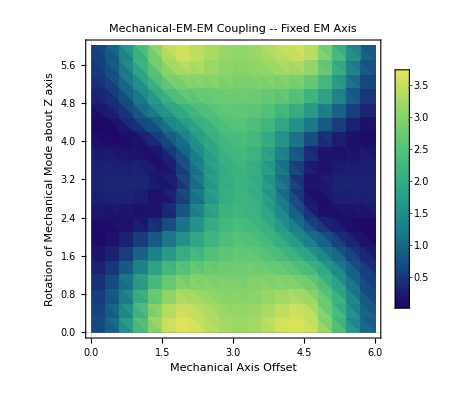

```mathematica
optpoints1={{0.0,Pi/4.0},{2.0*Pi,Pi/4.0}};
optpoints2={{0.0,2.0*Pi-3.0*Pi/4.0},{2.0*Pi,2.0*Pi-3.0*Pi/4.0}};
p1=ListDensityPlot[Abs[angularOverlaps1],PlotTheme->"Scientific", FrameLabel->{Style["Mechanical Axis Offset",16], Style["Rotation of Mechanical Mode about Z axis",16]},PlotLabel->Style["Mechanical-EM-EM Coupling -- Fixed EM Axis",16], InterpolationOrder->2,ColorFunction->"BlueGreenYellow"]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/mech-em-em-coupling-fixedEMpolarization-vary-mechanical-axis-and-polarization.png",p1,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/mech-em-em-coupling-fixedEMpolarization-vary-mechanical-axis-and-polarization.png

#### Right function wrong frequency splitting

```mathematica
angularOverlaps={{{0.,0.,-27.960472716120947},{0.,0.3,-26.02050686091922},{0.,0.6,-21.534733635114186},{0.,0.8999999999999999,-14.952312413546192},{0.,1.2,-9.136220558553049},{0.,1.5,-7.208730837230907},{0.,1.7999999999999998,-8.021922862560894},{0.,2.1,-12.449953954467661},{0.,2.4,-18.808768321752993},{0.,2.6999999999999997,-24.495580279260366},{0.,3.,-27.580175340132058}},{{0.3,0.,-25.997862046384228},{0.3,0.3,-25.11048789676591},{0.3,0.6,-19.604525305344264},{0.3,0.8999999999999999,-12.979414711567532},{0.3,1.2,-7.931217582744931},{0.3,1.5,-5.330735143608484},{0.3,1.7999999999999998,-6.296667981864672},{0.3,2.1,-10.35002697187591},{0.3,2.4,-16.945229414184425},{0.3,2.6999999999999997,-22.60241137587495},{0.3,3.,-25.941828445259667}},{{0.6,0.,-21.408276084801418},{0.6,0.3,-19.61770438168749},{0.6,0.6,-14.555508119914343},{0.6,0.8999999999999999,-8.196986797278091},{0.6,1.2,-2.6346976158526534},{0.6,1.5,-0.15995073532404813},{0.6,1.7999999999999998,-1.3833159801454453},{0.6,2.1,-5.691660799797039},{0.6,2.4,-11.741039513191009},{0.6,2.6999999999999997,-17.68137628895758},{0.6,3.,-21.05299220901437}},{{0.8999999999999999,0.,-14.770176587046368},{0.8999999999999999,0.3,-13.148261732497675},{0.8999999999999999,0.6,-8.044634106677002},{0.8999999999999999,0.8999999999999999,-2.136130170116152},{0.8999999999999999,1.2,3.067867268351742},{0.8999999999999999,1.5,5.80532413945167},{0.8999999999999999,1.7999999999999998,4.925754572127225},{0.8999999999999999,2.1,0.6166753006685364},{0.8999999999999999,2.4,-5.64458919989189},{0.8999999999999999,2.6999999999999997,-10.924967961918556},{0.8999999999999999,3.,-14.865186118252097}},{{1.2,0.,-9.552772267503729},{1.2,0.3,-7.6871669775692375},{1.2,0.6,-2.7978841652941577},{1.2,0.8999999999999999,3.063551880620132},{1.2,1.2,8.773402039251403},{1.2,1.5,11.397429472928756},{1.2,1.7999999999999998,10.216098176450199},{1.2,2.1,5.871824136388648},{1.2,2.4,-0.39516457865417465},{1.2,2.6999999999999997,-5.513886897621195},{1.2,3.,-9.759223829862137}},{{1.5,0.,-7.402131546629543},{1.5,0.3,-4.882784063385195},{1.5,0.6,-0.08850748306732736},{1.5,0.8999999999999999,5.807385645146162},{1.5,1.2,11.230778476706472},{1.5,1.5,13.6521628818726},{1.5,1.7999999999999998,12.871475126610846},{1.5,2.1,8.707072531837472},{1.5,2.4,2.2698291347339303},{1.5,2.6999999999999997,-3.739497374970002},{1.5,3.,-7.073121831932078}},{{1.7999999999999998,0.,-8.465608667868803},{1.7999999999999998,0.3,-6.145959916286062},{1.7999999999999998,0.6,-2.186838071032396},{1.7999999999999998,0.8999999999999999,4.701334105593752},{1.7999999999999998,1.2,10.123306608332172},{1.7999999999999998,1.5,12.901875684593447},{1.7999999999999998,1.7999999999999998,11.791840897316506},{1.7999999999999998,2.1,7.6377967906383954},{1.7999999999999998,2.4,1.7771016873410925},{1.7999999999999998,2.6999999999999997,-3.9706419696849027},{1.7999999999999998,3.,-7.5990208103917585}},{{2.1,0.,-12.254625652089134},{2.1,0.3,-10.408155092711578},{2.1,0.6,-5.7077984450187715},{2.1,0.8999999999999999,0.483457993117665},{2.1,1.2,5.804026845282698},{2.1,1.5,8.35749495844653},{2.1,1.7999999999999998,7.750138754698066},{2.1,2.1,3.2883741412379477},{2.1,2.4,-2.4996661315718187},{2.1,2.6999999999999997,-8.706838549349929},{2.1,3.,-11.967976905776723}},{{2.4,0.,-19.06677154381652},{2.4,0.3,-16.43628390872536},{2.4,0.6,-12.109522639607121},{2.4,0.8999999999999999,-5.2736325928005146},{2.4,1.2,0.19838771761205987},{2.4,1.5,2.284115247769166},{2.4,1.7999999999999998,1.2409333111038077},{2.4,2.1,-3.1616557699699896},{2.4,2.4,-9.204435270882378},{2.4,2.6999999999999997,-14.186475240536693},{2.4,3.,-17.76201790790985}},{{2.6999999999999997,0.,-24.2574626703086},{2.6999999999999997,0.3,-21.7624708996408},{2.6999999999999997,0.6,-18.125820904824508},{2.6999999999999997,0.8999999999999999,-11.624436831170733},{2.6999999999999997,1.2,-5.480618034790852},{2.6999999999999997,1.5,-3.377264693295224},{2.6999999999999997,1.7999999999999998,-4.089476981925204},{2.6999999999999997,2.1,-8.626953903162308},{2.6999999999999997,2.4,-14.364008686105727},{2.6999999999999997,2.6999999999999997,-20.44877288401445},{2.6999999999999997,3.,-23.8546601375406}},{{3.,0.,-28.130006204082278},{3.,0.3,-26.155589934278385},{3.,0.6,-20.548225943722713},{3.,0.8999999999999999,-14.820025447291219},{3.,1.2,-9.464310007372479},{3.,1.5,-6.2806989603313435},{3.,1.7999999999999998,-7.847338683889712},{3.,2.1,-12.222366445676304},{3.,2.4,-17.645816572534},{3.,2.6999999999999997,-24.240264890747483},{3.,3.,-26.910491631367023}}};
```

```mathematica
angularOverlaps=Flatten[angularOverlaps,1];
```

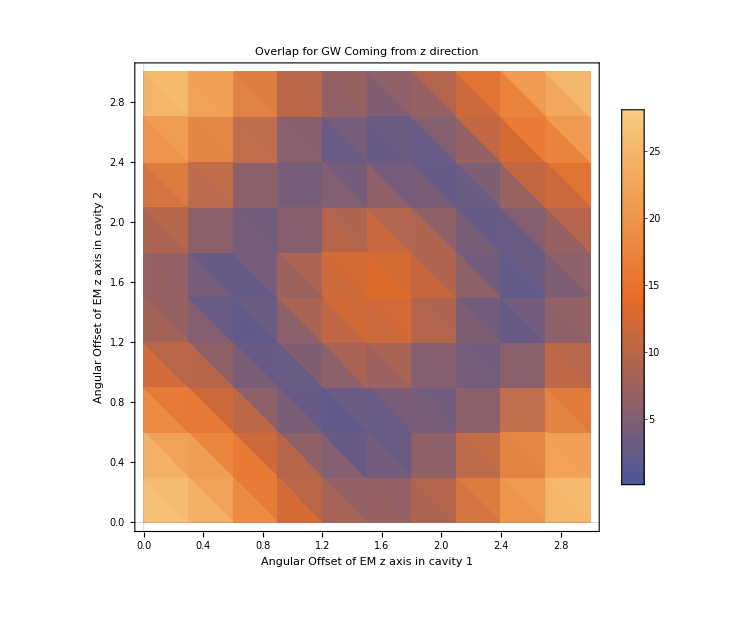

```mathematica
myplot=ListDensityPlot[Abs[angularOverlaps],PlotTheme->"Scientific",PlotLabel->"Overlap for GW Coming from z direction",FrameLabel->{"Angular Offset of EM z axis in cavity 1","Angular Offset of EM z axis in cavity 2"}]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/overlaps-with-EM-polarization.png",myplot,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/overlaps-with-EM-polarization.png

# Double Spherical Shell GW-Mechanical Coupling

We basically just need to compute the integral given in eq. (114) of Sebastian’s notes. The coupling should just be eq. (19) from my notes where the strain and the time dependence comes from the actual form of the + polarized GW.

#### Coordinate transformation of TT metric perturbation

```mathematica
cartinsphere={r*Cos[ϕ]*Sin[θ],r*Sin[ϕ]*Sin[θ],r*Cos[θ]};
spherecoords={r,θ,ϕ};
jacobian=Table[D[cartinsphere[[i]],spherecoords[[j]]],{i,1,3},{j,1,3}];
ttMetric={{1,0,0},{0,-1,0},{0,0,0}};
ttMetricSpherical=Module[{a,b,i,j},Table[Simplify[Sum[ttMetric[[a,b]]*jacobian[[a,i]]*jacobian[[b,j]],{a,1,3},{b,1,3}]],{i,1,3},{j,1,3}]];
```

```mathematica
ttMetricSpherical//MatrixForm
```

(Cos[2 ϕ] Sin[θ]^2 | 1/2 r Cos[2 ϕ] Sin[2 θ] | -2 r Cos[ϕ] Sin[θ]^2 Sin[ϕ]
1/2 r Cos[2 ϕ] Sin[2 θ] | r^2 Cos[θ]^2 Cos[2 ϕ] | -2 r^2 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ]
-2 r Cos[ϕ] Sin[θ]^2 Sin[ϕ] | -2 r^2 Cos[θ] Cos[ϕ] Sin[θ] Sin[ϕ] | -r^2 Cos[2 ϕ] Sin[θ]^2)

#### GW-Mechanical coupling function

```mathematica
garbageVariableUsedToDefineFunctions=r^3 * Sin[θ] *({Cos[ϕ]*Sin[θ],-Sin[ϕ]*Sin[θ]}.{(displacementVecQ[m,n,l,a,c0,d0,c1,d1,c2,d2,r,θ,ϕ,pol1,pol2,pol3].{Sin[θ]*Cos[ϕ],Cos[θ]*Cos[ϕ],-Sin[ϕ]}),(displacementVecQ[m,n,l,a,c0,d0,c1,d1,c2,d2,r,θ,ϕ,pol1,pol2,pol3].{Sin[θ]*Sin[ϕ],Cos[θ]*Sin[ϕ],Cos[ϕ]})});
gwMechCouplingIntegrandFixedGWVarMechCart2Sphere[m_,n_,l_,a_,c0_,d0_,c1_,d1_,c2_,d2_,r_,θ_,ϕ_,pol1_,pol2_,pol3_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions];
```

```mathematica
gwMechCouplingFixedGWVarMechCart2Sphere[m_,n_,l_,a_,b_,pol1_,pol2_,pol3_]:=NIntegrate[Re[Activate[gwMechCouplingIntegrandFixedGWVarMechCart2Sphere[m,n,l,a,"C0","D0",0.0,0.0,"C2","D2",r,θ,ϕ,pol1,pol2,pol3]/.Quiet[(StringJoin["m",ToString[m],"n",ToString[n],"l",ToString[l]]/.MODES[[1]])]]],{r,a,b},{θ,0.0,Pi},{ϕ,-Pi,Pi},Method->"LevinRule",PrecisionGoal->4]/(2*((4/3)*Pi*(outerRadius^3 - innerRadius^3))^(3/3)*((4/3)*Pi*innerRadius^3)^(1/3))
gwMechCouplingFixedGWVarMechCart2SphereMC[m_,n_,l_,a_,b_,pol1_,pol2_,pol3_]:=NIntegrate[Re[Activate[gwMechCouplingIntegrandFixedGWVarMechCart2Sphere[m,n,l,a,"C0","D0",0.0,0.0,"C2","D2",r,θ,ϕ,pol1,pol2,pol3]/.Quiet[(StringJoin["m",ToString[m],"n",ToString[n],"l",ToString[l]]/.MODES[[1]])]]],{r,a,b},{θ,0.0,Pi},{ϕ,-Pi,Pi},Method->"AdaptiveMonteCarlo",PrecisionGoal->4,MaxPoints->10^5]/(2*((4/3)*Pi*(outerRadius^3 - innerRadius^3))^(4/3))
gwMechCouplingFixedGWVarMechCart2SphereTwoSpheres[m_,n_,l_,a_,b_,pol_]:=NIntegrate[Re[Activate[gwMechCouplingIntegrandFixedGWVarMechCart2Sphere[m,n,l,a,"C0","D0",0.0,0.0,"C2","D2",r,θ,ϕ,pol]/.Quiet[(StringJoin["m",ToString[m],"n",ToString[n],"l",ToString[l]]/.MODES[[1]])]]],{r,a,b},{θ,0.01,Pi},{ϕ,-Pi+0.01,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^5,PrecisionGoal->2]/(2*(4/3)*Pi*(outerRadius^3 - innerRadius^3))
```

#### Test integrand and integral

```mathematica
Re[Activate[gwMechCouplingIntegrandFixedGWVarMechCart2Sphere[2,0,0,innerRadius,"C0","D0",0.0,0.0,"C2","D2",1.004,0.1,0.2,Pi/4]/.Quiet[(StringJoin["m",ToString[2],"n",ToString[0],"l",ToString[0]]/.MODES[[1]])]//N]]
```

Re[gwMechCouplingIntegrandFixedGWVarMechCart2Sphere[2.,0.,0.,0.2,47.1908,0.0191296,0.,0.,3.46041,-0.126813,1.004,0.1,0.2,0.785398]]

```mathematica
gwMechCouplingFixedGWVarMechCart2Sphere[2,3,2,innerRadius,outerRadius,0.0,0.0,0.0]//AbsoluteTiming
(*gwMechCouplingFixedGWVarMechCart2SphereTwoSpheres[2,0,1,innerRadius,outerRadius,0]//AbsoluteTiming*)
```

{364.775,-0.0000116789}

```mathematica
gwMechCouplingFixedGWVarMechCart2Sphere[2,2,2,innerRadius,outerRadius,0.0,0.0,0.0]//AbsoluteTiming
```

{7.14093,0.00467069}

```mathematica
2*gwMechCouplingFixedGWVarMechCart2Sphere[2,0,0,innerRadius,outerRadius,0.0,0.0,0.0]//AbsoluteTiming
```

$Aborted

```mathematica
Activate[omegaMech[3,0,2,innerRadius]]
```

12047.6

# Figures

### Optimal polarization of EM axes

```mathematica
overlapCoupledSpheresArtificialSplitting[{2,0,2,0,1,2},innerRadius,0,1,0.1,{0.0,Pi/4.0,0.0,0.0,Pi/4.0,0.0,0.0,-Pi/4.0,0.0},0.0033]//AbsoluteTiming
```

{0.000018,overlapCoupledSpheresArtificialSplitting[{2,0,2,0,1,2},innerRadius,0,1,0.1,{0.,0.785398,0.,0.,0.785398,0.,0.,-0.785398,0.},0.0033]}

```mathematica
overlapCoupledSpheresArtificialSplitting[{2,0,2,0,1,2},innerRadius,0,1,0.1,{0.0,Pi/4.0,0.0,0.0,Pi/4.0,0.0,Pi/4.0,-Pi/4.0,0.0},0.0033]//AbsoluteTiming
```

{78.9422,-0.725731}

```mathematica
OverlapsWithVariablePolarizationTableFlattened=Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/test-best-polarization.csv","CSV"]
```

{{0.01,p,-0.00150691},{0.01,p,-0.00981326},{0.01,p,-0.038635},{0.01,p,-0.0924824},{0.01,p,-0.156562},{0.01,p,-0.232535},{0.01,p,-0.317543},{0.01,p,-0.406718},{0.01,p,-0.492586},1414,{3.13,p,-0.425593},{3.13,p,-0.342898},{3.13,p,-0.250109},{3.13,p,-0.16849},{3.13,p,-0.105311},{3.13,p,-0.055432},{3.13,p,-0.0164482},{3.13,p,-0.0051649}}
 |  |  |  |

```mathematica
OverlapsWithVariablePolarizationTableFlattenedAbs=OverlapsWithVariablePolarizationTableFlattened;
OverlapsWithVariablePolarizationTableFlattenedAbs[[All,3]]=Abs[OverlapsWithVariablePolarizationTableFlattenedAbs[[All,3]]];
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/data-for-sebastian/optimal-polarization-2d.csv",OverlapsWithVariablePolarizationTableFlattenedAbs,"CSV"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/data-for-sebastian/optimal-polarization-2d.csv

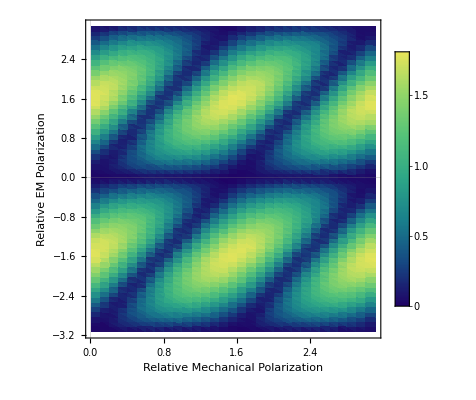

```mathematica
ListDensityPlot[OverlapsWithVariablePolarizationTableFlattenedAbs,PlotTheme->"Scientific",FrameLabel->{Style["Relative Mechanical Polarization",20],Style["Relative EM Polarization",20]},ColorFunction->"BlueGreenYellow",AspectRatio->1,ImageSize->{400,400},ColorFunctionScaling->True,PlotLegends->Automatic]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/optimal-polarizations.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/optimal-polarizations.png

```mathematica
(*indices={1,10,11,12,13,14,15,16,17,18,20,21,22,23,24,25,26,27,28,38,39,40,41,42,43,44,45,46,47,48,57,59,60,61,62};*)
indices={6,3,2};
polarizationData={};
Module[{i},For[i=1,i<=Length[indices],i++,AppendTo[polarizationData,Import[StringJoin["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/test-best-polarization-pi",ToString[indices[[i]]],".csv"],"CSV"]]]]
interpolationFncs={};
Module[{i},For[i=1,i<=Length[indices],i++,AppendTo[interpolationFncs,Interpolation[polarizationData[[i]],InterpolationOrder->1]]]]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/data-for-sebastian/optimal-polarization-3d-pi6.csv",polarizationData[[1]],"CSV"]
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/data-for-sebastian/optimal-polarization-3d-pi3.csv",polarizationData[[2]],"CSV"]
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/data-for-sebastian/optimal-polarization-3d-pi2.csv",polarizationData[[3]],"CSV"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/data-for-sebastian/optimal-polarization-3d-pi6.csv

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/data-for-sebastian/optimal-polarization-3d-pi3.csv

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/data-for-sebastian/optimal-polarization-3d-pi2.csv

```mathematica
polarizationData[[3]]
polarizationData[[2]]
```

{{0.01,-3.13159,-0.0169165},{0.01,-3.02159,-0.0123859},{0.01,-2.91159,-0.0170326},{0.01,-2.80159,-0.0199274},{0.01,-2.69159,-0.0158059},{0.01,-2.58159,-0.0139429},1670,{3.09,2.58841,0.0669126},{3.09,2.69841,0.0700404},{3.09,2.80841,0.0777725},{3.09,2.91841,0.0751481},{3.09,3.02841,0.0840149},{3.09,3.13841,0.0728671}}
 |  |  |  |

{{0.01,-3.13159,-0.0124335},{0.01,-3.02159,-0.00853099},{0.01,-2.91159,-0.0160782},{0.01,-2.80159,-0.00748033},{0.01,-2.69159,-0.00925657},{0.01,-2.58159,-0.0138839},1670,{3.09,2.58841,0.0551056},{3.09,2.69841,0.0598257},{3.09,2.80841,0.0594785},{3.09,2.91841,0.0617067},{3.09,3.02841,0.0696587},{3.09,3.13841,0.0650123}}
 |  |  |  |

```mathematica
myRange={{-0.9,0.9},{0.0,0.9},{-0.9,0.9}};
viewpoint={-1.5,-1.05,0.2};

mag1=1.7;
bubbles=SphericalPlot3D[{Abs[interpolationFncs[[1]][theta,phi]],Abs[interpolationFncs[[2]][theta,phi]],Abs[interpolationFncs[[3]][theta,phi]]},{theta,0,Pi},{phi,0,Pi},PlotRange->All,PlotLegends->{MaTeX["|\\beta_L - \\beta_R| = \\frac{\\pi}{6}",Magnification->mag1],MaTeX["|\\beta_L - \\beta_R| = \\frac{\\pi}{3}",Magnification->mag1],MaTeX["|\\beta_L - \\beta_R| = \\frac{\\pi}{2}",Magnification->mag1]},Axes->False,AspectRatio->1,Boxed->False,PerformanceGoal->"Quality",ViewPoint->viewpoint,ImageSize->Large];

r00=0.8;
phi00list={0,Pi/3,2*Pi/3,Pi};
thetalinelist=Table[ParametricPlot3D[{r00*Cos[phi00list[[i]]]*Sin[theta],r00*Sin[phi00list[[i]]]*Sin[theta],r00*Cos[theta]},{theta,0,Pi},AspectRatio->1,PlotRange->All,Axes->False,Boxed->False,PlotStyle->Directive[RGBColor[0,102/256,102/256],Thickness[0.003]],ViewPoint->viewpoint,ImageSize->Large],{i,1,Length[phi00list]}];

r00=0.8;
theta00list={Pi/4,Pi/2,3*Pi/4};
philinelist=Table[ParametricPlot3D[{r00*Cos[phi]*Sin[theta00list[[i]]],r00*Sin[phi]*Sin[theta00list[[i]]],r00*Cos[theta00list[[i]]]},{phi,0,Pi},AspectRatio->1,ColorFunction->Black,PlotRange->All,Axes->False,Boxed->False,PlotStyle->Directive[RGBColor[175/256,17/256,17/256],Thickness[0.003]],ViewPoint->viewpoint,ImageSize->Large],{i,1,Length[theta00list]}];

thetapoints=ListPointPlot3D[{{0.0,0.0,0.8},{0.0,0.0,-0.8}},PlotStyle->Directive[RGBColor[175/256,17/256,17/256],PointSize[Large]],AspectRatio->1,Axes->False,Boxed->False,PlotRange->All,ViewPoint->viewpoint,ImageSize->Large];

mesh=SphericalPlot3D[0.8,{theta,0,Pi},{phi,0,Pi},PlotRange->All,PlotStyle->Directive[Black,Opacity[0.05]],Mesh->None,Axes->False,AspectRatio->1,Boxed->False,PerformanceGoal->"Quality",ViewPoint->viewpoint,ImageSize->Large];
```

```mathematica
offset=0.15;
fontsize=16;
mag2=1.5;
myBeautifulGraph=Show[thetalinelist[[1]],thetalinelist[[2]],thetalinelist[[3]],thetalinelist[[4]],philinelist[[1]],philinelist[[2]],philinelist[[3]],bubbles,thetapoints,Graphics3D[Text[MaTeX["\\color{purple}\\gamma_p = 0",Magnification->mag2],{0,-0.05,r00+0.08}]],Graphics3D[Text[MaTeX["\\color{purple}\\gamma_p = \\frac{\\pi}{4}",Magnification->mag2],FromSphericalCoordinates[{r00+offset,1.15*Pi/4,-0.1}]]],Graphics3D[Text[MaTeX["\\color{purple}\\gamma_p = \\frac{\\pi}{2}",Magnification->mag2],FromSphericalCoordinates[{r00+0.1,Pi/2-0.04,-0.1}]]],Graphics3D[Text[MaTeX["\\color{purple}\\gamma_p = \\frac{3 \\pi}{4}",Magnification->mag2],FromSphericalCoordinates[{r00+0.2,0.94*3*Pi/4,-0.08}]]],Graphics3D[Text[MaTeX["\\color{purple}\\gamma_p = \\pi",Magnification->mag2],{0,-0.07,-r00-0.04}]],Graphics3D[Text[MaTeX["\\color{teal}\\beta_p = 0",Magnification->mag2],FromSphericalCoordinates[{r00+0.1,Pi/2+0.13,-0.1}]]],Graphics3D[Text[MaTeX["\\color{teal}\\beta_p = \\frac{\\pi}{3}",Magnification->mag2],FromSphericalCoordinates[{r00+offset,Pi/2+0.1,Pi/3-0.01}]]],Graphics3D[Text[MaTeX["\\color{teal}\\beta_p = \\frac{2 \\pi}{3}",Magnification->mag2],FromSphericalCoordinates[{r00+0.14,Pi/2,2*Pi/3}]]],Graphics3D[Text[MaTeX["\\color{teal}\\beta_p = \\pi",Magnification->mag2],FromSphericalCoordinates[{r00+0.1,Pi/2+0.02,Pi-0.01}]]],mesh]
```

-Graphics3D-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/optimal-polarization-3d-beautiful.pdf",myBeautifulGraph,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/optimal-polarization-3d-beautiful.pdf

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/optimal-polarization-3d-beautiful.png",myBeautifulGraph,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/optimal-polarization-3d-beautiful.png

### Overlaps: (η^200)_(012,012) Fixed EM Polarization Variable GW Directionality Plus Polarization

Plot of the mechanical-EM-EM overlap factor for mechanical mode 200 and EM modes 012+ and 012-. Double cavity setup with a fixed splitting on 1 MHz. EM polarizations set to -Pi/4 and 5 Pi/4 for the left and right cavities respectively. Coupling axis is along x. Directionality of the GW is determined by RollPitchYawMatrix[{α, β, 0}]. The plot is made by converting the z’’ axis (given by RollPitchYawMatrix[{α, β, 0}].{0, 0, 1} into spherical coordinates and then plotting an Aitoff projection. In this sense, the GW polarization is fixed. Since the third euler angle is zero, this GW is plus polarized.

```mathematica
filename="eta-200-012-012-EMpol-Piover4-5Piover4-variable-mechanical-euler-alpha-beta-hi-res.txt";
(* import data *)
overlaps=Flatten[Import[StringJoin["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius1-thickness1percent/overlaps/",filename],"CSV"],1];
(* name data floats *)
For[i=1,i<=Length[overlaps],i++,overlaps[[i]]=ToExpression[overlaps[[i]]]]
(* covert first two points to aitoff projection *)
overlapsSpherical={};
For[i=1,i<Length[overlaps],i++,AppendTo[overlapsSpherical,{#1,#2,overlaps[[i,3]]}]&@@euler2spherical[overlaps[[i,1]],overlaps[[i,2]],0.0]];
overlapsAitoff={};
For[i=1,i<Length[overlapsSpherical],i++,AppendTo[overlapsAitoff,{#1,#2,Abs[overlapsSpherical[[i,3]]]/((32*Pi/3)^(1/3))}]&@@aitoff[overlapsSpherical[[i,1]],overlapsSpherical[[i,2]]]];
p1=ListDensityPlot[overlaps,PlotTheme->"Scientific", FrameLabel->{Style["Euler Angle α",16], Style["Euler Angle β",16]},PlotLabel->Style["Mechanical-EM-EM Coupling -- 200-012-012",20], InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic]
p2=ListDensityPlot[overlapsSpherical,PlotTheme->"Scientific", FrameLabel->{Style["Inclination θ",16], Style["Azimuth ϕ",16]},PlotLabel->Style["Mechanical-EM-EM Coupling -- 200-012-012",20], InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic]
p3=ListDensityPlot[overlapsAitoff,PlotTheme->"Scientific", FrameLabel->{Style["Aitoff x (θ, ϕ)",20], Style["Aitoff y (θ, ϕ)",20]},PlotLabel->Style["Mechanical-EM-EM Coupling -- 200-012-012 -- MHz Splitting",24], InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ImageSize->{800,500}]
(*Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/eta-200-012-012-EMpol-Piover4-5Piover4-variable-mechanical-euler-alpha-beta-hi-res.png",p3,"PNG"]*)
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Activate[getNormalizationFactor[1,0,1,2,1.0,0,wavenumberEM[0,1,2,1.0,0]]]
Activate[getNormalizationFactor[1,0,1,2,1.0,0,wavenumberEM[0,1,2,1.0,0]+0.0033]]
```

7.768

7.80461

### nothing

```mathematica
overlapIntegrand[mVec_,iVec_,jVec_,a_,modeCoefs_,EMamplitude_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_,ki_,kj_,wi_,wj_,θ_,ϕ_,offsets_]:=(a^2*Sin[θ]*(displacementVecQ[mVec[[1]],mVec[[2]],mVec[[3]],a,modeCoefs[[1]],modeCoefs[[2]],modeCoefs[[3]],modeCoefs[[4]],modeCoefs[[5]],modeCoefs[[6]],a,θ,ϕ,offsets[[1]],offsets[[2]],offsets[[3]]].{1,0,0})*((wi/wj)*magneticField[EMamplitude,parityOfFieldj,TMorTEFeildj,jVec[[1]],jVec[[2]],jVec[[3]],a,kj,a,θ,ϕ,offsets[[4]],offsets[[5]],offsets[[6]]].magneticField[EMamplitude,parityOfFieldi,TMorTEFeildi,iVec[[1]],iVec[[2]],iVec[[3]],a,ki,a,θ,ϕ,offsets[[4]],offsets[[5]],offsets[[6]]]-electricField[EMamplitude,parityOfFieldj,TMorTEFeildj,jVec[[1]],jVec[[2]],jVec[[3]],a,kj,a,θ,ϕ,offsets[[4]],offsets[[5]],offsets[[6]]].electricField[EMamplitude,parityOfFieldi,TMorTEFeildi,iVec[[1]],iVec[[2]],iVec[[3]],a,ki,a,θ,ϕ,offsets[[4]],offsets[[5]],offsets[[6]]]))
```

```mathematica
displacementVecQ[2,0,0,0.1,Quiet["C0"/.("m2n0l0"/.MODES[[1]])],Quiet["D0"/.("m2n0l0"/.MODES[[1]])],0.0,0.0,Quiet["C2"/.("m2n0l0"/.MODES[[1]])],Quiet["D2"/.("m2n0l0"/.MODES[[1]])],0.1,0.1,0.2,0.0,0.0,0.0].{1,0,0}
```

```mathematica
"m2n0l0"/.MODES[[1]]
```

{wavenumberk→1.78981,wavenumberp→0.783212,frequency→2817.12,C0→2.18785,C2→0.0000728853,D0→0.140649,D2→-0.00167631}

### Make Plots Function

Plot of the mechanical-EM-EM overlap factor for mechanical mode 100 and EM modes 012+ and 012-. Double cavity setup with a fixed splitting on 1 MHz. EM polarizations set to -Pi/4 and 5 Pi/4 for the left and right cavities respectively. Coupling axis is along x. Directionality of the GW is determined by RollPitchYawMatrix[{α, β, 0}]. The plot is made by converting the z’’ axis (given by RollPitchYawMatrix[{α, β, 0}].{0, 0, 1} into spherical coordinates and then plotting an Aitoff projection. In this sense, the GW polarization is fixed. Since the third euler angle is zero, this GW is plus polarized.

```mathematica
makeplot[mode_,ncs_]:=Module[{mymode,overlaps,filename,overlapsSpherical,overlapsAitoff},mymode=mode;
filename=StringJoin["eta-",ToString[mymode],"-012-012-EMPol-minpi4-pi4-hires.csv"];
(* import data *)
overlaps=Import[StringJoin["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/overlaps/",filename],"CSV"];
(* name data floats *)
(*For[i=1,i<=Length[overlaps],i++,overlaps[[i]]=ToExpression[overlaps[[i]]]];*)
(* covert first two points to aitoff projection *)
overlapsSpherical={};
For[i=1,i<Length[overlaps],i++,AppendTo[overlapsSpherical,{overlaps[[i,1]],overlaps[[i,2]],Abs[overlaps[[i,3]]](*/((32*8*Pi/3)^(1/3))*)}]&@@euler2spherical[overlaps[[i,1]],overlaps[[i,2]],0.0]];
overlapsAitoff={};
For[i=1,i<Length[overlapsSpherical],i++,AppendTo[overlapsAitoff,{#1,#2,Abs[overlapsSpherical[[i,3]]]}]&@@aitoff[overlapsSpherical[[i,1]],overlapsSpherical[[i,2]]]];
{p1=ListContourPlot[overlaps,PlotTheme->"Scientific", FrameLabel->{Style["Euler Angle α",16], Style["Euler Angle β",16]},PlotLabel->Style[StringJoin["Mechanical-EM-EM Coupling -- ",ToString[mymode],"-012-012"],20], InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ColorFunctionScaling->True,PlotLegends->Automatic,Contours->ncs],
p2=ListContourPlot[overlapsSpherical,PlotTheme->"Scientific", FrameLabel->{Style["Inclination θ",16], Style["Azimuth ϕ",16]},PlotLabel->Style[StringJoin["Mechanical-EM-EM Coupling -- ",ToString[mymode],"-012-012"],20], InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ColorFunctionScaling->True,PlotLegends->Automatic,Contours->ncs],
p3=ListContourPlot[overlapsAitoff,PlotTheme->"Scientific", FrameLabel->{Style["x (θ, ϕ)",20], Style["y (θ, ϕ)",20]},PlotLabel->Style[StringJoin["Coupling -- ",ToString[mymode],"-012-012"],20], InterpolationOrder->2,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ImageSize->{300,200},ColorFunctionScaling->True,PlotLegends->Automatic,Contours->ncs]}]
(*Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/eta-200-012-012-EMpol-Piover4-5Piover4-variable-mechanical-euler-alpha-beta-hi-res.png",p3,"PNG"]*)
```

```mathematica
myplots=makeplot[210,7];
GraphicsRow[{myplots[[2]],myplots[[3]]},ImageSize->Full]
```

-Graphics-

### Grid of mech. mode results cavity radius 1.0 thickness 0.01

```mathematica
plots={};
modelist={410};
For[k=1,k<=1,k++,AppendTo[plots,makeplot[modelist[[k]],7][[3]]]]
```

```mathematica
GraphicsGrid[{plots[[1;;2]],plots[[3;;4]]},ImageSize->{800,950}]
```

-Graphics-

```mathematica
plots[[1]]
```

-Graphics-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/overlaps-correct-sign-m=4.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/overlaps-correct-sign-m=4.png

### Grid of mech. mode results cavity radius 0.2 thickness 0.005

```mathematica
plots={};
modelist={200,201,202,210,211,212,220,221,222};
For[k=1,k<=9,k++,AppendTo[plots,makeplot[modelist[[k]],7][[3]]]]
```

```mathematica
GraphicsGrid[{plots[[1;;3]],plots[[4;;6]],plots[[7;;9]]},ImageSize->{1200,825}]
```

-Graphics-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/overlaps-radius-0.2-m2.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/overlaps-radius-0.2-m2.png

```mathematica
plots={};
modelist={200,210,220,230,250,260,280,290,2100};
For[k=1,k<=9,k++,AppendTo[plots,makeplot[modelist[[k]],4][[3]]]]
GraphicsGrid[{plots[[1;;3]],plots[[4;;6]],plots[[7;;9]]},ImageSize->{1200,1100*3/4}]
```

-Graphics-

### Super high resolution radius 0.2 thickness 0.005

```mathematica
overlaps={};
kks={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20};
For[kk=1,kk<=20,kk++,
filename=StringJoin["eta-202-012-012-EMPol-minpi4-pi4-highest-res-",ToString[kks[[kk]]],".csv"];
(* import data *)
overlaps=Join[overlaps,Import[StringJoin["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/overlaps/",filename],"CSV"]]]
```

```mathematica
overlapsInterpolated[t_,p_]:=Interpolation[overlaps,InterpolationOrder->1,Method->"BSplineBasis"][t,p]
```

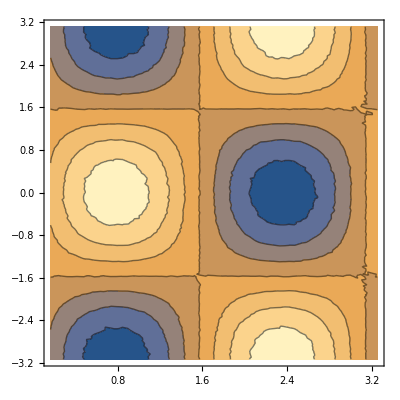

```mathematica
ListContourPlot[overlaps]
```

```mathematica
interpolateddata=Table[{t,p,overlapsInterpolated[t,p]},{t,0.01,Pi,0.1},{p,-Pi+0.01,Pi,0.1}]
```

{{{0.01,-3.13159,-0.0355092},{0.01,-3.03159,-0.0381034},{0.01,-2.93159,-0.0335814},{0.01,-2.83159,-0.0150661},{0.01,-2.73159,-0.0192474},{0.01,-2.63159,-0.0424239},{0.01,-2.53159,-0.0187826},50,{0.01,2.56841,-0.0680953},{0.01,2.66841,-0.0463105},{0.01,2.76841,-0.0301752},{0.01,2.86841,-0.0857448},{0.01,2.96841,-0.0249885},{0.01,3.06841,-0.0287336}},30,{1}}
 |  |  |  |

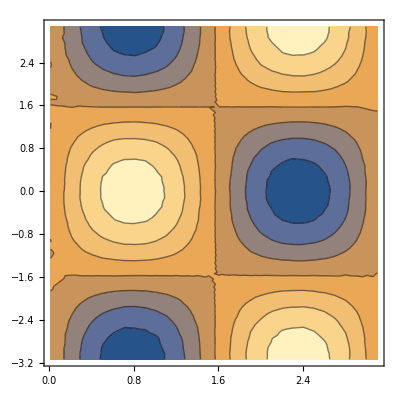

```mathematica
ListContourPlot[Flatten[interpolateddata,1]]
```

```mathematica
overlaps=Flatten[interpolateddata,1]
```

{{0.,-3.14159,-0.0221371},{0.,-3.04159,-0.0256804},{0.,-2.94159,-0.0225064},{0.,-2.84159,-0.00145271},{0.,-2.74159,-0.0031845},{0.,-2.64159,-0.0343871},{0.,-2.54159,-0.00623693},2002,{3.1,2.45841,0.0494124},{3.1,2.55841,0.050801},{3.1,2.65841,0.0542789},{3.1,2.75841,0.0592646},{3.1,2.85841,0.0529826},{3.1,2.95841,0.0695644},{3.1,3.05841,0.0637743}}
 |  |  |  |

```mathematica
overlapsSpherical={};
For[i=1,i<Length[overlaps],i++,AppendTo[overlapsSpherical,{overlaps[[i,1]],overlaps[[i,2]],Abs[overlaps[[i,3]]]}]&@@euler2spherical[overlaps[[i,1]],overlaps[[i,2]],0.0]];
overlapsAitoff={};
For[i=1,i<Length[overlapsSpherical],i++,AppendTo[overlapsAitoff,{#1,#2,Abs[overlapsSpherical[[i,3]]]}]&@@aitoff[overlapsSpherical[[i,1]],overlapsSpherical[[i,2]]]];
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/data-for-sebastian/212-112-mech-em-overlaps.csv",overlaps,"CSV"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/data-for-sebastian/212-112-mech-em-overlaps.csv

```mathematica
overlapsAitoff
```

{{-1.92367×10^-16,-1.5708,0.0221371},{-1.92127×10^-16,-1.5708,0.0256804},{-1.91406×10^-16,-1.5708,0.0225064},{-1.90207×10^-16,-1.5708,0.00145271},{-1.88533×10^-16,-1.5708,0.0031845},2004,{0.122002,1.55567,0.0494124},{0.124172,1.55761,0.050801},{0.126039,1.55958,0.0542789},{0.127597,1.56158,0.0592646},{0.128841,1.5636,0.0529826}}
 |  |  |  |

```mathematica
contplot=ListContourPlot[overlapsAitoff,PlotTheme->"Scientific", (*FrameLabel->{Style["x (θ, ϕ)",20], Style["y (θ, ϕ)",20]},*)(*PlotLabel->Style[StringJoin["Coupling -- ",ToString[202],"-012-012"],20],*)ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ColorFunctionScaling->True,PlotLegends->Automatic,Contours->40,ImageSize->{800,500},Axes->False,Frame->False,PerformanceGoal->"Quality",InterpolationOrder->1]
```

-Graphics-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/202-mech-em-coupling-hi-res-contour-log-interpolation.pdf",contplot2,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/202-mech-em-coupling-hi-res-contour-log-interpolation.pdf

```mathematica
ListDensityPlot[myvals,PlotTheme->"Scientific", (*FrameLabel->{Style["x (θ, ϕ)",20], Style["y (θ, ϕ)",20]},*)(*PlotLabel->Style[StringJoin["Coupling -- ",ToString[202],"-012-012"],20], *)InterpolationOrder->1,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ImageSize->{800,500},ColorFunctionScaling->True,Axes->False,Frame->False,
PlotLegends->BarLegend[{"BlueGreenYellow",{0,1}},LabelStyle->Directive[FontSize->20,Black,"Serif"]]]
```

-Graphics-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/202-mech-em-coupling-hi-res-density-log-interpolation.pdf",%,"PDF","CompressionLevel"->3]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/202-mech-em-coupling-hi-res-density-log-interpolation.pdf

```mathematica
ListContourPlot[overlaps,PlotTheme->"Scientific", FrameLabel->{Style["x (θ, ϕ)",20], Style["y (θ, ϕ)",20]},PlotLabel->Style[StringJoin["Coupling -- ",ToString[202],"-012-012"],20], InterpolationOrder->1,ColorFunction->"BlueGreenYellow",AspectRatio->Automatic,ImageSize->{800,500},ColorFunctionScaling->True,PlotLegends->Automatic]
```

-Graphics-

```mathematica
f=Interpolation[overlapsSpherical];
SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData["BlueGreenYellow"][Rescale[f[u,v],{0,0.1}]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{0.0,0.1}}],Axes->False,Boxed->False]
```

-Graphics3D-

### Wrap density map on sphere

```mathematica
gwMechCouplingFixedGWVarMechCart2Sphere[2,0,1,innerRadius,outerRadius,0.0,0.0,0.0]
gwMechCouplingFixedGWVarMechCart2Sphere[2,0,2,innerRadius,outerRadius,0.0,0.0,0.0]
```

$Aborted

-0.409548

```mathematica
mymode=200;
filename=StringJoin["eta-",ToString[mymode],"-012-012-EMPol-minpi4-pi4-hires.csv"];
overlaps=Import[StringJoin["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/overlaps/",filename],"CSV"];
overlapsSpherical={};
For[i=1,i<Length[overlaps],i++,AppendTo[overlapsSpherical,{{overlaps[[i,1]],overlaps[[i,2]]},Abs[overlaps[[i,3]]]/((32*8*Pi/3)^(1/3))}]];
f=Interpolation[overlapsSpherical];
SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData["BlueGreenYellow"][Rescale[f[u,v],{0,0.1}]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{0.0,0.3}}],Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
overlapsSpherical
```

{{{0.01,-3.13159},0.00240371},{{0.01,-2.93159},0.00297726},{{0.01,-2.73159},0.00179089},{{0.01,-2.53159},0.00153386},{{0.01,-2.33159},0.00163621},{{0.01,-2.13159},0.00119849},500,{{3.01,2.06841},0.0143029},{{3.01,2.26841},0.0190813},{{3.01,2.46841},0.0228902},{{3.01,2.66841},0.0270259},{{3.01,2.86841},0.0307698}}
 |  |  |  |

### Modes 2n2

```mathematica
myns
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
"frequency"/.StringJoin["m2n",ToString[myns[[1]]],"l2"]/.MODES[[1]]
```

12409.5

```mathematica
Activate[overlapCoupledSpheresArtificialSplitting[{2,40,2,0,1,2},innerRadius,0,1,0.1,{0.0,Pi/4.0,0.0,0.0,-Pi/4.0,0.0,0.0,Pi/4.0,0.0},0.0033]]//AbsoluteTiming
```

{78.4009,1.23048}

```mathematica
rdisplacements={};
(* make list of ns *)
myns={};
Module[{n},For[n=0,n<=128,n++,If[Head[StringJoin["m2n",ToString[n],"l2"]/.MODES[[1]]]==Head[{1,2,3}],AppendTo[myns,n],Clear[garbageVariableUsedToDefineFunctions],Clear[garbageVariableUsedToDefineFunctions]]]]
modesWithFrequency=ParallelTable[{myns[[n]],Activate[overlapCoupledSpheresArtificialSplitting[{2,myns[[n]],2,0,1,2},innerRadius,0,1,0.1,{0.0,Pi/4.0,0.0,0.0,-Pi/4.0,0.0,0.0,Pi/4.0,0.0},0.0033]]},{n,0,Length[myns]-1}]
```

ReplaceAll::reps: 
   {m2nListl2 /. MODES[[1]]} is neither a list of replacement rules nor a
     valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: 
   The integrand Re[overlapIntegrand[{2, List, 2}, {0, 1, 2}, {0, 1, 2}, 
      innerRadius, {C0, D0, 0., 0., C2, D2} /. (m2nListl2 /. <<1>>), <<11>>, 
      {0., 0.785398, 0., 0., -0.785398, 0., 0., -0.785398, 0.}, 1]] has
     evaluated to non-numerical values for all sampling points in the region
     with boundaries {{0., 3.14159}, {-3.14159, 3.14159}}.

ReplaceAll::reps: 
   {m2nListl2 /. MODES[[1]]} is neither a list of replacement rules nor a
     valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: 
   The integrand Re[overlapIntegrand[{2, List, 2}, {0, 1, 2}, {0, 1, 2}, 
      innerRadius, {C0, D0, 0., 0., C2, D2} /. (m2nListl2 /. <<1>>), <<10>>, 
      ϕ, {0., 0.785398, 0., 0., 0.785398, 0., 0., 0.785398, 0.}, -1]] has
     evaluated to non-numerical values for all sampling points in the region
     with boundaries {{0., 3.14159}, {-3.14159, 3.14159}}.

ReplaceAll::reps: 
   {m2nListl2 /. MODES[[1]]} is neither a list of replacement rules nor a
     valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps
     will be suppressed during this calculation.

NIntegrate::inumr: 
   The integrand Re[overlapIntegrand[{2, List, 2}, {0, 1, 2}, {0, 1, 2}, 
      innerRadius, {C0, D0, 0., 0., C2, D2} /. (m2nListl2 /. <<1>>), <<11>>, 
      {0., 0.785398, 0., 0., -0.785398, 0., 0., -0.785398, 0.}, 1]] has
     evaluated to non-numerical values for all sampling points in the region
     with boundaries {{0., 3.14159}, {-3.14159, 3.14159}}.

General::stop: Further output of NIntegrate::inumr
     will be suppressed during this calculation.

ReplaceAll::reps: 
   {m2n6l2 /. MODES[[1]]} is neither a list of replacement rules nor a valid
     dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: 
   The integrand Re[overlapIntegrand[{2, 6, 2}, {0, 1, 2}, {0, 1, 2}, 
      innerRadius, {C0, D0, 0., 0., C2, D2} /. (m2n6l2 /. MODES[[1]]), 
      <<10>>, ϕ, {0., 0.785398, 0., 0., -0.785398, 0., 0., -0.785398, 0.}, 1]]
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0., 3.14159}, {-3.14159, 3.14159}}.

ReplaceAll::reps: 
   {m2n6l2 /. MODES[[1]]} is neither a list of replacement rules nor a valid
     dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: 
   The integrand Re[overlapIntegrand[{2, 6, 2}, {0, 1, 2}, {0, 1, 2}, 
      innerRadius, {C0, D0, 0., 0., C2, D2} /. (m2n6l2 /. MODES[[1]]), 
      <<10>>, ϕ, {0., 0.785398, 0., 0., 0.785398, 0., 0., 0.785398, 0.}, -1]]
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0., 3.14159}, {-3.14159, 3.14159}}.

ReplaceAll::reps: 
   {m2n6l2 /. MODES[[1]]} is neither a list of replacement rules nor a valid
     dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps
     will be suppressed during this calculation.

NIntegrate::inumr: 
   The integrand Re[overlapIntegrand[{2, 6, 2}, {0, 1, 2}, {0, 1, 2}, 
      innerRadius, {C0, D0, 0., 0., C2, D2} /. (m2n6l2 /. MODES[[1]]), 
      <<10>>, ϕ, {0., 0.785398, 0., 0., -0.785398, 0., 0., -0.785398, 0.}, 1]]
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0., 3.14159}, {-3.14159, 3.14159}}.

General::stop: Further output of NIntegrate::inumr
     will be suppressed during this calculation.

ReplaceAll::reps: 
   {m2n7l2 /. MODES[[1]]} is neither a list of replacement rules nor a valid
     dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: 
   The integrand Re[overlapIntegrand[{2, 7, 2}, {0, 1, 2}, {0, 1, 2}, 
      innerRadius, {C0, D0, 0., 0., C2, D2} /. (m2n7l2 /. MODES[[1]]), 
      <<10>>, ϕ, {0., 0.785398, 0., 0., -0.785398, 0., 0., -0.785398, 0.}, 1]]
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0., 3.14159}, {-3.14159, 3.14159}}.

ReplaceAll::reps: 
   {m2n7l2 /. MODES[[1]]} is neither a list of replacement rules nor a valid
     dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: 
   The integrand Re[overlapIntegrand[{2, 7, 2}, {0, 1, 2}, {0, 1, 2}, 
      innerRadius, {C0, D0, 0., 0., C2, D2} /. (m2n7l2 /. MODES[[1]]), 
      <<10>>, ϕ, {0., 0.785398, 0., 0., 0.785398, 0., 0., 0.785398, 0.}, -1]]
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0., 3.14159}, {-3.14159, 3.14159}}.

ReplaceAll::reps: 
   {m2n7l2 /. MODES[[1]]} is neither a list of replacement rules nor a valid
     dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps
     will be suppressed during this calculation.

NIntegrate::inumr: 
   The integrand Re[overlapIntegrand[{2, 7, 2}, {0, 1, 2}, {0, 1, 2}, 
      innerRadius, {C0, D0, 0., 0., C2, D2} /. (m2n7l2 /. MODES[[1]]), 
      <<10>>, ϕ, {0., 0.785398, 0., 0., -0.785398, 0., 0., -0.785398, 0.}, 1]]
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0., 3.14159}, {-3.14159, 3.14159}}.

General::stop: Further output of NIntegrate::inumr
     will be suppressed during this calculation.

ReplaceAll::reps: 
   {m2n8l2 /. MODES[[1]]} is neither a list of replacement rules nor a valid
     dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: 
   The integrand Re[overlapIntegrand[{2, 8, 2}, {0, 1, 2}, {0, 1, 2}, 
      innerRadius, {C0, D0, 0., 0., C2, D2} /. (m2n8l2 /. MODES[[1]]), 
      <<10>>, ϕ, {0., 0.785398, 0., 0., -0.785398, 0., 0., -0.785398, 0.}, 1]]
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0., 3.14159}, {-3.14159, 3.14159}}.

ReplaceAll::reps: 
   {m2n8l2 /. MODES[[1]]} is neither a list of replacement rules nor a valid
     dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: 
   The integrand Re[overlapIntegrand[{2, 8, 2}, {0, 1, 2}, {0, 1, 2}, 
      innerRadius, {C0, D0, 0., 0., C2, D2} /. (m2n8l2 /. MODES[[1]]), 
      <<10>>, ϕ, {0., 0.785398, 0., 0., 0.785398, 0., 0., 0.785398, 0.}, -1]]
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0., 3.14159}, {-3.14159, 3.14159}}.

ReplaceAll::reps: 
   {m2n8l2 /. MODES[[1]]} is neither a list of replacement rules nor a valid
     dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps
     will be suppressed during this calculation.

NIntegrate::inumr: 
   The integrand Re[overlapIntegrand[{2, 8, 2}, {0, 1, 2}, {0, 1, 2}, 
      innerRadius, {C0, D0, 0., 0., C2, D2} /. (m2n8l2 /. MODES[[1]]), 
      <<10>>, ϕ, {0., 0.785398, 0., 0., -0.785398, 0., 0., -0.785398, 0.}, 1]]
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0., 3.14159}, {-3.14159, 3.14159}}.

General::stop: Further output of NIntegrate::inumr
     will be suppressed during this calculation.

ReplaceAll::reps: 
   {m2n9l2 /. MODES[[1]]} is neither a list of replacement rules nor a valid
     dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: 
   The integrand Re[overlapIntegrand[{2, 9, 2}, {0, 1, 2}, {0, 1, 2}, 
      innerRadius, {C0, D0, 0., 0., C2, D2} /. (m2n9l2 /. MODES[[1]]), 
      <<10>>, ϕ, {0., 0.785398, 0., 0., -0.785398, 0., 0., -0.785398, 0.}, 1]]
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0., 3.14159}, {-3.14159, 3.14159}}.

ReplaceAll::reps: 
   {m2n9l2 /. MODES[[1]]} is neither a list of replacement rules nor a valid
     dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: 
   The integrand Re[overlapIntegrand[{2, 9, 2}, {0, 1, 2}, {0, 1, 2}, 
      innerRadius, {C0, D0, 0., 0., C2, D2} /. (m2n9l2 /. MODES[[1]]), 
      <<10>>, ϕ, {0., 0.785398, 0., 0., 0.785398, 0., 0., 0.785398, 0.}, -1]]
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0., 3.14159}, {-3.14159, 3.14159}}.

ReplaceAll::reps: 
   {m2n9l2 /. MODES[[1]]} is neither a list of replacement rules nor a valid
     dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps
     will be suppressed during this calculation.

NIntegrate::inumr: 
   The integrand Re[overlapIntegrand[{2, 9, 2}, {0, 1, 2}, {0, 1, 2}, 
      innerRadius, {C0, D0, 0., 0., C2, D2} /. (m2n9l2 /. MODES[[1]]), 
      <<10>>, ϕ, {0., 0.785398, 0., 0., -0.785398, 0., 0., -0.785398, 0.}, 1]]
     has evaluated to non-numerical values for all sampling points in the
     region with boundaries {{0., 3.14159}, {-3.14159, 3.14159}}.

General::stop: Further output of NIntegrate::inumr
     will be suppressed during this calculation.

NIntegrate::maxp: 
   The integral failed to converge after 10100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000547846 and 5.93909 10
     for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

$Aborted

```mathematica
Activate[overlapCoupledSpheresArtificialSplittingGlobalAdaptive[{2,0,2,0,1,2},innerRadius,0,1,0.1,{0.0,Pi/6.0,0.0,0.0,-Pi/4.0,0.0,0.0,Pi/4.0,0.0},0.0033]]//AbsoluteTiming
```

{9.05023,0.631134}

```mathematica
{"C0","D0",0.0,0.0,"C2","D2"}/."m2n124l2"/.MODES[[1]]
```

{1.01527,0.00115816,0.,0.,0.000118122,-0.000332562}

```mathematica
(* just plot radial displacement *)
rdisplacements={};
ns={0,1,2,3,5,6,8,9,10};
Module[{i},For[i=1,i<=9,i++,mvec={2,ns[[i]],2};
z=0.1;
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
AppendTo[rdisplacements,{ns[[i]],Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,Pi/2,0.0,0.0,0.0,0.0][[1]]]]}]]];
```

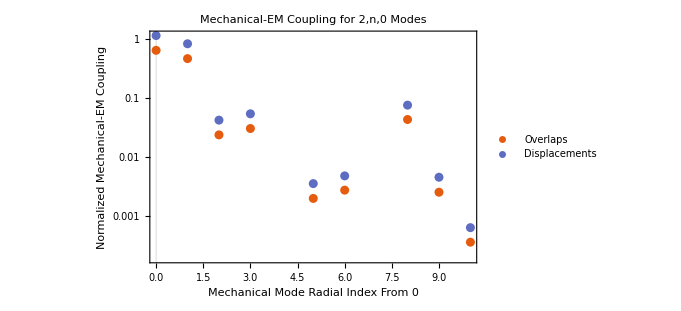

```mathematica
bothplot=ListLogPlot[{Abs[modesWithFrequency],Abs[rdisplacements]},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"Mechanical Mode Radial Index From 0","Normalized Mechanical-EM Coupling"},PlotLabel->"Mechanical-EM Coupling for 2,n,0 Modes",PlotLegends->{"Overlaps","Displacements"}]
```

### Plot displacements out to n=128

```mathematica
rdisplacements={};
(* make list of ns *)
ns={};
Module[{n},For[n=0,n<=128,n++,If[Head[StringJoin["m2n",ToString[n],"l2"]/.MODES[[1]]]==Head[{1,2,3}],AppendTo[ns,n],Clear[garbageVariableUsedToDefineFunctions],Clear[garbageVariableUsedToDefineFunctions]]]]
```

```mathematica
Length[ns]
```

129

```mathematica
Module[{i},For[i=1,i<=Length[ns],i++,mvec={2,ns[[i]],2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
AppendTo[rdisplacements,{ns[[i]],Re[Evaluate[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,Pi/2,0.0,0.0,0.0,0.0][[1]]]]]}]]];
```

$Aborted

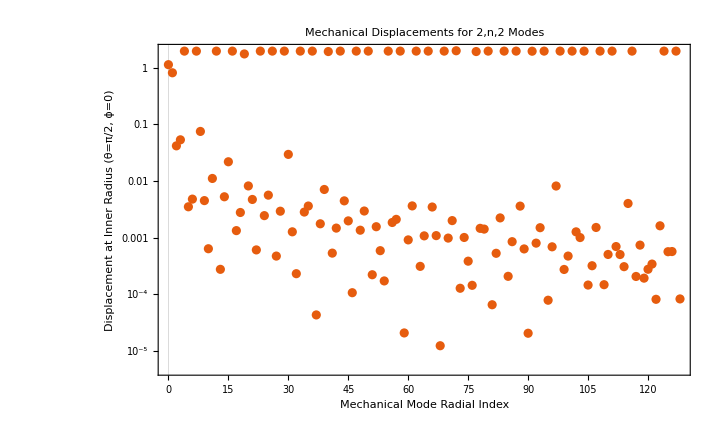

```mathematica
displot=ListLogPlot[Abs[rdisplacements],PlotRange->All,PlotTheme->"Scientific",FrameLabel->{Style["Mechanical Mode Radial Index",18],Style["Displacement at Inner Radius (θ=π/2, ϕ=0)",18]},PlotLabel->Style["Mechanical Displacements for 2,n,2 Modes",18]]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/radial-displacements.png",displot,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/radial-displacements.png

Find out which points are over 1 and see if there’s a pattern

```mathematica
nsGreaterThan1={};
Module[{n},For[n=0,n<=128,n++,If[Abs[rdisplacements[[n]][[2]]]>1.0,AppendTo[nsGreaterThan1,n]]]]
```

```mathematica
nsGreaterThan1
```

{1,5,8,13,17,20,24,27,30,34,37,41,44,48,51,56,59,63,66,70,73,78,81,85,88,92,95,99,102,105,109,112,117,125,128}

```mathematica
43543433434343534343534343433435
```

```mathematica
rdisplacements[[1]][[2]]
```

-1.12983

### Calculate GW-Mech coupling out to n=128

```mathematica
gw mech couplings={};
Module[{i},For[i=0,i<30,i++,
AppendTo[gw mech couplings,{i,2*gwMechCouplingFixedGWVarMechCart2Sphere[2,i,2,innerRadius,outerRadius,0.0,0.0,0.0]}];Print[i]]];
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

```mathematica
(*gw mech couplings={{5.932372150064459,-0.4086634150814706},{25.08444808257359,0.11970550719268995},{628.8365033529869,0.004670689728271012},{1256.5237295968607,-0.0000116788735650819}};
gw mech couplingsN={{1,-0.4086634150814706},{2,0.11970550719268995},{3,0.004670689728271012},{4,-0.0000116788735650819}};*)
```

```mathematica
gw mech couplings 2={};
Module[{i},For[i=30,i<50,i++,
AppendTo[gw mech couplings 2,{i,2*gwMechCouplingFixedGWVarMechCart2Sphere[2,i,2,innerRadius,outerRadius,0.0,0.0,0.0]}];Print[i]]];
```

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

```mathematica
gw mech couplings
```

{{0,-0.348304},{1,0.101076},{2,0.00396652},{3,-9.8982×10^-6},{4,0.000546671},{5,-0.000441567},{6,3.57245×10^-6},{7,4.80637×10^-6},{8,-0.00015892},{9,-1.15095×10^-6},{10,0.0000811308},{11,0.0000490716},{12,-4.92401×10^-7},{13,-4.82164×10^-7},{14,0.0000328521},{15,8.52925×10^-8},{16,0.000021879},{17,-0.0000235199},{18,2.58237×10^-7},{19,-1.03723×10^-7},{20,-0.0000176671},{21,1.76123×10^-7},{22,-0.0000137611},{23,0.0000111577},{24,1.64098×10^-7},{25,0.0000110107},{26,-1.26994×10^-7},{27,-1.20529×10^-7},{28,9.01268×10^-6},{29,6.75093×10^-6}}

```mathematica
gw mech couplings 2
```

{{30,-1.9801×10^-7},{31,-7.51407×10^-6},{32,-8.43808×10^-8},{33,-6.07948×10^-8},{34,6.36009×10^-6},{35,6.74133×10^-8},{36,4.5208×10^-6},{37,-5.45241×10^-6},{38,6.51195×10^-8},{39,4.72627×10^-6},{40,-6.18364×10^-8},{41,-5.35005×10^-8},{42,4.13637×10^-6},{43,3.23223×10^-6},{44,3.42961×10^-8},{45,3.64983×10^-6},{46,-5.19726×10^-8},{47,-3.37218×10^-8},{48,3.24464×10^-6},{49,3.48163×10^-8}}

```mathematica
(*fits in n = FindFit[Abs[gw mech couplingsN],a*x^(-b),{a,b},x];
fits in k = FindFit[Abs[gw mech couplings],a*x^(-b),{a,b},x];*)
```

```mathematica
(*fitDataN=Table[{n,a*n^(-b)/.fits in n},{n,1,4,0.1}];
fitDatak=Table[{k,a*k^(-b)/.fits in k},{k,5,1257,1.0}];*)
```

```mathematica
gwMechCouplings2={};
Module[{i},For[i=1,i<=20,i++,AppendTo[gwMechCouplings2,{"frequency"/.StringJoin["m2n",ToString[i+30-1],"l2"]/.MODES[[1]],gw mech couplings 2[[i,2]]}]]]
```

```mathematica
gwMechCouplings
```

{{12409.5,-0.348304},{52472.3,0.101076},{1.31542×10^6,0.00396652},{2.62843×10^6,-9.8982×10^-6},{3.20273×10^6,0.000546671},{3.94311×10^6,-0.000441567},{5.25745×10^6,3.57245×10^-6},{6.40359×10^6,4.80637×10^-6},{6.57199×10^6,-0.00015892},{7.88605×10^6,-1.15095×10^-6},{9.20038×10^6,0.0000811308},{1.1829×10^7,0.0000490716},{1.28072×10^7,-4.92401×10^-7},{1.31434×10^7,-4.82164×10^-7},{1.44577×10^7,0.0000328521},{1.5772×10^7,8.52925×10^-8},{1.60089×10^7,0.000021879},{1.70863×10^7,-0.0000235199},{1.84007×10^7,2.58237×10^-7},{1.92106×10^7,-1.03723×10^-7},{1.9715×10^7,-0.0000176671},{2.10293×10^7,1.76123×10^-7},{2.23437×10^7,-0.0000137611},{2.24123×10^7,0.0000111577},{2.3658×10^7,1.64098×10^-7},{2.49723×10^7,0.0000110107},{2.5614×10^7,-1.26994×10^-7},{2.62867×10^7,-1.20529×10^-7},{2.7601×10^7,9.01268×10^-6},{2.88158×10^7,6.75093×10^-6}}

```mathematica
gwMechCouplings2
```

{{2.89153×10^7,-1.9801×10^-7},{3.02297×10^7,-7.51407×10^-6},{3.1544×10^7,-8.43808×10^-8},{3.20175×10^7,-6.07948×10^-8},{3.28583×10^7,6.36009×10^-6},{3.41726×10^7,6.74133×10^-8},{3.52192×10^7,4.5208×10^-6},{3.5487×10^7,-5.45241×10^-6},{3.68013×10^7,6.51195×10^-8},{3.81156×10^7,4.72627×10^-6},{3.8421×10^7,-6.18364×10^-8},{3.943×10^7,-5.35005×10^-8},{4.07443×10^7,4.13637×10^-6},{4.16227×10^7,3.23223×10^-6},{4.20586×10^7,3.42961×10^-8},{4.3373×10^7,3.64983×10^-6},{4.46873×10^7,-5.19726×10^-8},{4.48245×10^7,-3.37218×10^-8},{4.60016×10^7,3.24464×10^-6},{4.7316×10^7,3.48163×10^-8}}

```mathematica
fits in f = FindFit[Abs[gwmechCouplings[[3;;30]]],a*(1/x)^(-b),{a,b},x];
fitDataf=Table[{f,a*(1/f)^(-b)/.fits in f},{f,10^4,10^8,10000}];
```

```mathematica
fits in f
```

{a→6.45789×10^9,b→-2.00344}

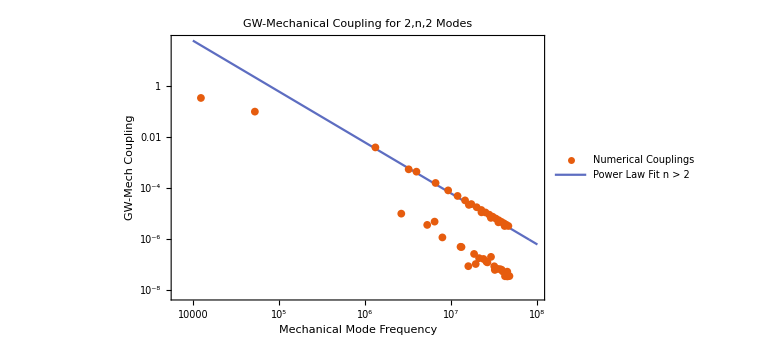

```mathematica
gwcouplingPlot=ListLogLogPlot[{Abs[gwmechCouplings],fitDataf},Joined->{False,True},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{Style["Mechanical Mode Frequency",20],Style["GW-Mech Coupling",20]},PlotLabel->Style["GW-Mechanical Coupling for 2,n,2 Modes",20],PlotLegends->{"Numerical Couplings", "Power Law Fit n > 2"},PlotMarkers->{{Automatic,8},None},ImageSize->Large]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/gw-mech-coupling-with-n.pdf",%,"PDF"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/gw-mech-coupling-with-n.pdf

```mathematica
"frequency"/."m2n2l2"/.MODES[[1]]
```

1.31542×10^6

```mathematica
Length[fitDataf]
```

10000

```mathematica
gw mech couplings[[30,2]]
```

7.93796×10^-6

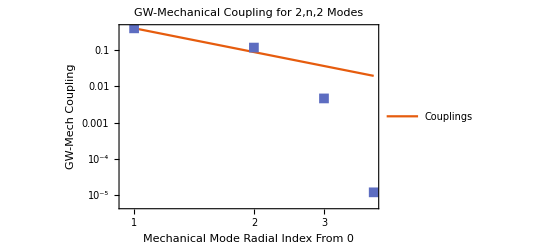

```mathematica
gwcouplingPlot=ListLogLogPlot[{fitDataN,Abs[gw mech couplingsN]},Joined->{True,False},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"Mechanical Mode Radial Index From 0","GW-Mech Coupling"},PlotLabel->"GW-Mechanical Coupling for 2,n,2 Modes",PlotLegends->{"Couplings"},PlotMarkers->{None,{Automatic,10}}]
```

```mathematica
gwmechCouplings={{12409.480767696727,-0.3483043320580753},{52472.260366471055,0.10107552367358201},{1.3154155364814326*^6,0.003966515524311713},{2.628426987072512*^6,-9.898195726629388*^-6},{3.202725581046194*^6,0.0005466705814464098},{3.9431099403288327*^6,-0.0004415674020519167},{5.257449686392999*^6,3.572446558813983*^-6},{6.403594191910093*^6,4.80636985697114*^-6},{6.571987757040123*^6,-0.00015892000260756743},{7.886047253282356*^6,-1.1509497212002097*^-6},{9.200384289052246*^6,0.00008113079479476668},{1.1829021288609548*^7,0.000049071551328079644},{1.2807162105872503*^7,-4.924008056189321*^-7},{1.3143360044753645*^7,-4.821641597250642*^-7},{1.4457693234215071*^7,0.000032852135383059455},{1.5771987877461556*^7,8.529252253930565*^-8},{1.6008892689117782*^7,0.000021879039880268845},{1.7086345844753616*^7,-0.000023519857726916798},{1.8400678491938*^7,2.5823690379596147*^-7},{1.921057499466591*^7,-1.0372318552057739*^-7},{1.9715016457667943*^7,-0.0000176670973788684},{2.1029335366623234*^7,1.7612340182828122*^-7},{2.234366842188835*^7,-0.000013761065334350202},{2.241230950348132*^7,0.000011157680130035558},{2.365800131608084*^7,1.6409758163939135*^-7},{2.497232558119132*^7,0.00001101067992466058},{2.5614043976244684*^7,-1.269943918361334*^-7},{2.6286660438500475*^7,-1.2052860669836141*^-7},{2.7600992719261236*^7,9.012679050268763*^-6},{2.881575262002291*^7,6.750929546034392*^-6},{2.891534461285734*^7,-1.980100702475307*^-7},{3.0229653511805773*^7,-7.514068183824626*^-6},{3.1543985814107217*^7,-8.438083418550319*^-8},{3.2017508525687885*^7,-6.079478475752694*^-8},{3.2858318819776177*^7,6.3600923239175125*^-6},{3.4172647025392905*^7,6.74133198325017*^-8},{3.521924753624357*^7,4.520801057254353*^-6},{3.5486979720352516*^7,-5.452407305979591*^-6},{3.6801311965214685*^7,6.511950391922529*^-8},{3.811563881937976*^7,4.726267952023433*^-6},{3.842098897729772*^7,-6.183636596293415*^-8},{3.942997408881314*^7,-5.3500465243796254*^-8},{4.0744306229845606*^7,4.136366669432712*^-6},{4.162272207966663*^7,3.232233767775175*^-6},{4.205863989609158*^7,3.429614739072662*^-8},{4.337296870813095*^7,3.6498255687543936*^-6},{4.468730094546566*^7,-5.197262338229165*^-8},{4.482446378479392*^7,-3.372183708062308*^-8},{4.600163324233804*^7,3.2446434656648563*^-6},{4.731596322882236*^7,3.48163356928494*^-8}};
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/gw-mech-couplins-2n2.csv",gwmechCouplings,"CSV"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/gw-mech-couplins-2n2.csv

### Even modes m02

```mathematica
(* find out how many coefficients calculated correctly *)
"m8n0l2"/.MODES[[1]]
```

{wavenumberk→9.16732,wavenumberp→3.76323,frequency→19176.4,C0→5.46844×10^8,C2→53967.3,D0→6.49089×10^-8,D2→-0.0000227249}

```mathematica
(* just try doing the calculations at the same point as above *)
myns={0,1,2,3,5,6,8,9,10};
modesWithFrequency=Table[{l,Activate[overlapCoupledSpheresArtificialSplitting[{l,0,2,0,1,2},innerRadius,0,1,0.1,{0.0,Pi/6.0,0.0,0.0,-Pi/4.0,0.0,0.0,Pi/4.0,0.0},0.0033]]},{l,2,8}]
```

{{2,0.656981},{3,-0.00161941},{4,0.00317309},{5,-0.0037984},{6,-0.00343638},{7,0.00251495},{8,0.0100299}}

```mathematica
ListPlot[Abs[modesWithFrequency],PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"Mechanical Mode Frequency (kHz)","Normalized Mechanical-EM Coupling"},PlotLabel->"Mechanical-EM Coupling for l,0,2 Modes"]
```

### Even modes as function of inclination index

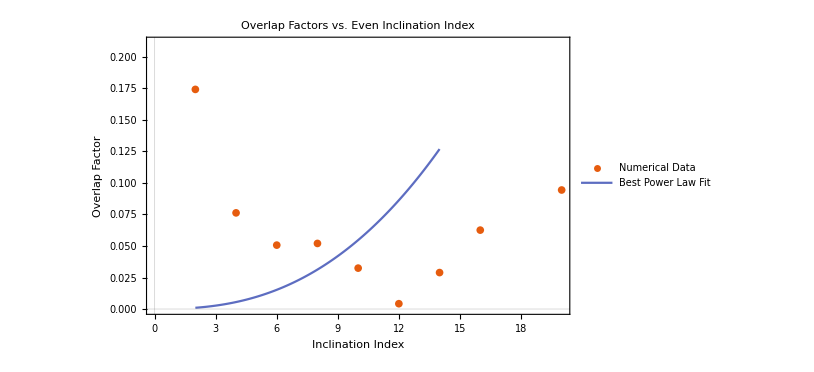

```mathematica
overlapFactors={{2,-1.1235584546663355},{4,-0.4919130249460447},{6,-0.3268342817602289},{8,-0.3354943578086973},{10,-0.20917577786521352},{12,-0.0271156506437399},{14,-0.18642779107256072},{16,-0.40364546211320407},{18,-4.406104286869174},{20,-0.6088732339288097}};
normfactor=(((32*8*Pi/3)^(1/3)))^(-1);
For[i=1,i<=Length[overlapFactors],i++,overlapFactors[[i,2]]=Abs[overlapFactors[[i,2]]]*normfactor]
fits = FindFit[overlapFactors,a*x^(-b),{a,b},x];
fitData=Table[{m,a*m^(-b)/.fits},{m,2,14,0.1}];
ListPlot[{overlapFactors,fitData},Joined->{False,True},PlotLabel->"Overlap Factors vs. Even Inclination Index",FrameLabel->{"Inclination Index", "Overlap Factor"},PlotTheme->"Scientific",PlotLegends->{"Numerical Data",TraditionalForm["Best Power Law Fit"]}]
```

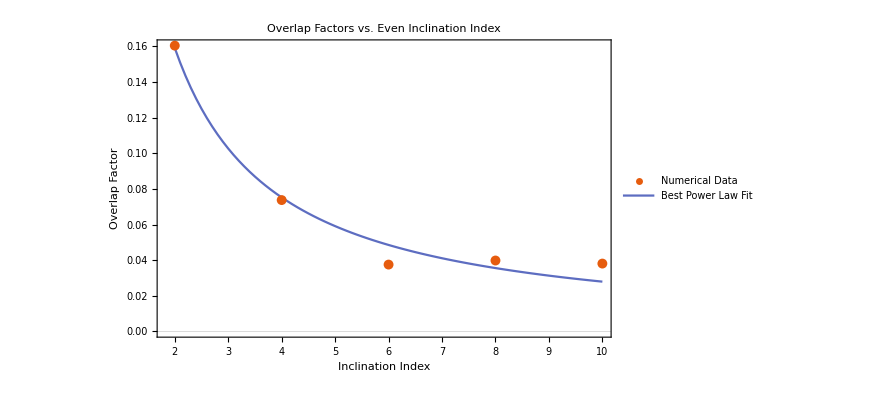

```mathematica
overlapFactors={{2,-1.0341905214781628},{4,-0.4753210516295555},{6,-0.24189868673184403},{8,-0.256644242200031},{10,-0.24555021477047248},{12,-0.26502006088785557},{14,-0.3736925389518085},{16,-0.4816832887383363},{18,-1.3555311566670856},{20,-0.42746618420901317}};
normfactor=(((32*8*Pi/3)^(1/3)))^(-1);
For[i=1,i<=Length[overlapFactors],i++,overlapFactors[[i,2]]=Abs[overlapFactors[[i,2]]]*normfactor]
fits = FindFit[overlapFactors[[1;;5]],a*x^(-b),{a,b},x];
fitData=Table[{m,a*m^(-b)/.fits},{m,2,10,0.1}];
ListPlot[{overlapFactors[[1;;5]],fitData},Joined->{False,True},PlotLabel->"Overlap Factors vs. Even Inclination Index",FrameLabel->{"Inclination Index", "Overlap Factor"},PlotTheme->"Scientific",PlotLegends->{"Numerical Data",TraditionalForm["Best Power Law Fit"]}]
```

```mathematica
fits
```

{a→0.336369,b→1.08053}

```mathematica
Activate[omegaMech[2,0,0,innerRadius]]
```

6275.69

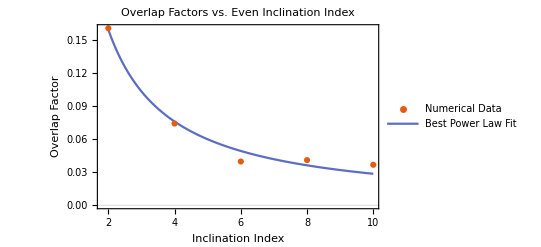

```mathematica
overlapFactors={{2,-1.0335823676574207},{4,-0.47689363383718625},{6,-0.25510648397465097},{8,-0.2632707498816675},{10,-0.2360591937627628},{12,-0.2871287128086725},{14,-0.326570042771931},{16,-0.5052490051342726},{18,-2.0248716117156285},{20,-0.45453124268413475}};
normfactor=(((32*8*Pi/3)^(1/3)))^(-1);
For[i=1,i<=Length[overlapFactors],i++,overlapFactors[[i,2]]=Abs[overlapFactors[[i,2]]]*normfactor]
fits = FindFit[overlapFactors[[1;;5]],a*x^(-b),{a,b},x];
fitData=Table[{m,a*m^(-b)/.fits},{m,2,10,0.1}];
ListPlot[{overlapFactors[[1;;5]],fitData},Joined->{False,True},PlotLabel->"Overlap Factors vs. Even Inclination Index",FrameLabel->{"Inclination Index", "Overlap Factor"},PlotTheme->"Scientific",PlotLegends->{"Numerical Data",TraditionalForm["Best Power Law Fit"]}]
```

```mathematica
fits
```

{a→0.333715,b→1.06944}

```mathematica
?omegaMech
```

### Modes 2n0 Single Cavity

```mathematica
(* get point at which to evaluate *)
aitoff[Pi/6,0.0]
```

{0.,2.0944}

```mathematica
"m2n10l0"/.MODES[[1]]
```

{wavenumberk→4398.26,wavenumberp→1805.51,frequency→9.20038×10^6,C0→0.000718916,C2→-0.418098,D0→0.00225187,D2→-0.00477947}

```mathematica
(*("frequency"/.StringJoin["m2n",ToString[myns[[n]]],"l0"]/.MODES[[1]])*)
```

```mathematica
myns={0,1,2,3,5,6,8,9,10};
modesWithFrequency1Cavity=ParallelTable[{myns[[n]],Activate[overlapfunction[{2,myns[[n]],0,0,1,2,0,1,2},innerRadius,0,0,1,1,wavenumberEM[0,1,2,innerRadius,0],wavenumberEM[0,1,2,innerRadius,0]+0.0033,wavenumberEM[0,1,2,innerRadius,0],wavenumberEM[0,1,2,innerRadius,0]+0.0033,{0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0,0.0},1]]},{n,1,9}]
```

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000555509 and 7.12617×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000548655 and 6.44704×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000555991 and 7.21449×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 10100 integrand evaluations. NIntegrate obtained 0.000541555 and 8.27105×10^-6 for the integral and error estimates.

{{0,1.19042},{1,0.868614},{2,-0.0435272},{3,-0.0563321},{5,-0.00369624},{6,0.00490837},{8,0.0792641},{9,0.00490329},{10,-0.000690746}}

```mathematica
(* just plot radial displacement *)
rdisplacements={};
ns={0,1,2,3,5,6,8,9,10};
Module[{i},For[i=1,i<=9,i++,mvec={2,ns[[i]],0};
z=0.1;
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
AppendTo[rdisplacements,{ns[[i]],Abs[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,Pi/2,0.0,0.0,0.0,0.0][[1]]]]]}]]];
```

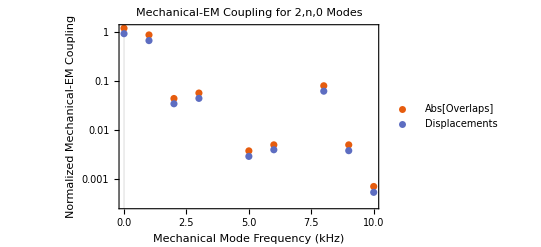

```mathematica
bothplot=ListLogPlot[{Abs[modesWithFrequency1Cavity],rdisplacements},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"Mechanical Mode Frequency (kHz)","Normalized Mechanical-EM Coupling"},PlotLabel->"Mechanical-EM Coupling for 2,n,0 Modes",PlotLegends->{"Abs[Overlaps]","Displacements"}]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/radial-mode-increase-single-cavity-with-displacements.png",bothplot,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/radial-mode-increase-single-cavity-with-displacements.png

### Plot displacements and em fields at surface

```mathematica
mvec={2,0,2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myfunc[θ_,ϕ_]:=Evaluate[FullSimplify[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,θ,ϕ,0.0,0.0,0.0][[1]]]]]];
displacementSpherical=Table[{{theta,phi},myfunc[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
displacementSpherical=Flatten[displacementSpherical,1];
f=Interpolation[displacementSpherical];
mech=SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData[{"BlueGreenYellow",{Min[displacementSpherical[[All,2]]],Max[displacementSpherical[[All,2]]]}}][f[u,v]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{Min[displacementSpherical[[All,2]]],Max[displacementSpherical[[All,2]]]}}],Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
func[u_,v_]:=Cos[2*u]
mech=SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData[{"BlueGreenYellow",{-1,1}}][func[u,v]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},func[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{-1,1}}],Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/mech.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/mech.png

```mathematica
myfunc[θ_,ϕ_]:=Evaluate[Norm[Activate[magneticField[1.0,1,0,1,1,2,innerRadius,wavenumberEM[1,1,2,innerRadius,0],innerRadius,θ,ϕ,0.0,0.0,0.0]]]];
emSpherical=Table[{{theta,phi},myfunc[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
emSpherical=Flatten[emSpherical,1];
f=Interpolation[emSpherical];
em1=SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData[{"BlueGreenYellow",{Min[emSpherical[[All,2]]],Max[emSpherical[[All,2]]]}}][f[u,v]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{Min[emSpherical[[All,2]]],Max[emSpherical[[All,2]]]}}],Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
myfunc[θ_,ϕ_]:=Evaluate[Norm[Activate[magneticField[1.0,1,0,0,1,2,innerRadius,wavenumberEM[0,1,2,innerRadius,0],innerRadius,θ,ϕ,0.0,Pi/2.0,0.0]]]];
emSpherical=Table[{{theta,phi},myfunc[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
emSpherical=Flatten[emSpherical,1];
f=Interpolation[emSpherical];
em1=SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData[{"BlueGreenYellow",{Min[emSpherical[[All,2]]],Max[emSpherical[[All,2]]]}}][f[u,v]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{Min[emSpherical[[All,2]]],Max[emSpherical[[All,2]]]}}],Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
myfunc[θ_,ϕ_]:=Evaluate[Norm[Activate[magneticField[1.0,1,0,1,1,2,innerRadius,wavenumberEM[0,1,2,innerRadius,0],innerRadius,θ,ϕ,0.0,Pi/4.0,0.0]]]];
```

```mathematica
emSpherical=Table[{{theta,phi},myfunc[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
emSpherical=Flatten[emSpherical,1];
f=Interpolation[emSpherical];
```

```mathematica
em1=SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData[{"BlueGreenYellow",{Min[emSpherical[[All,2]]],Max[emSpherical[[All,2]]]}}][f[u,v]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{Min[emSpherical[[All,2]]],Max[emSpherical[[All,2]]]}}],Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
em1=SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData[{"BlueGreenYellow",{Min[emSpherical[[All,2]]],Max[emSpherical[[All,2]]]}}][f[u,v]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{Min[emSpherical[[All,2]]],Max[emSpherical[[All,2]]]}}],Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/mech.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/mech.png

```mathematica
myfunc[θ_,ϕ_]:=Evaluate[Norm[Activate[magneticField[1.0,1,0,0,2,1,innerRadius,wavenumberEM[0,1,2,innerRadius,0],innerRadius,θ,ϕ,0.0,-Pi/4.0,0.0]]]];
```

```mathematica
emSpherical=Table[{{theta,phi},myfunc[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
emSpherical=Flatten[emSpherical,1];
f=Interpolation[emSpherical];
```

```mathematica
em2=SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData[{"BlueGreenYellow",{Min[emSpherical[[All,2]]],Max[emSpherical[[All,2]]]}}][f[u,v]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{Min[emSpherical[[All,2]]],Max[emSpherical[[All,2]]]}}],Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/em-2.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/em-2.png

```mathematica
mymode=202;
filename=StringJoin["eta-",ToString[mymode],"-012-012-EMPol-minpi4-pi4-hires.csv"];
overlaps=Import[StringJoin["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/overlaps/",filename],"CSV"];
overlapsSpherical={};
For[i=1,i<Length[overlaps],i++,AppendTo[overlapsSpherical,{{overlaps[[i,1]],overlaps[[i,2]]},Abs[overlaps[[i,3]]]/((32*8*Pi/3)^(1/3))}]];
f=Interpolation[overlapsSpherical];
over=SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData["BlueGreenYellow"][Rescale[f[u,v],{0,0.25}]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{0.0,0.25}}],Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/201-overlap.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/talks-posters/GWs-mechanical-poster/images/201-overlap.png

```mathematica
mech
```

-Graphics3D-

```mathematica
em1
```

-Graphics3D-

```mathematica
em2
```

-Graphics3D-

```mathematica
mvec={2,0,2};
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myfunc[θ_,ϕ_]:=Evaluate[FullSimplify[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],innerRadius,θ,ϕ,0.0,Pi/4.0,0.0][[1]]]]]];
displacementSpherical=Table[{{theta,phi},myfunc[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
displacementSpherical=Flatten[displacementSpherical,1];
fmech=Interpolation[displacementSpherical];

myfunc[θ_,ϕ_]:=Evaluate[Norm[Activate[magneticField[1.0,1,0,0,1,2,innerRadius,wavenumberEM[0,1,2,innerRadius,0],innerRadius,θ,ϕ,0.0,Pi/4.0,0.0]]]]
emSpherical=Table[{{theta,phi},myfunc[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
emSpherical=Flatten[emSpherical,1];
fem1=Interpolation[emSpherical];

myfunc[θ_,ϕ_]:=Evaluate[Norm[Activate[magneticField[1.0,1,0,0,1,2,innerRadius,wavenumberEM[0,1,2,innerRadius,0],innerRadius,θ,ϕ,0.0,-Pi/4.0,0.0]]]]
emSpherical=Table[{{theta,phi},myfunc[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
emSpherical=Flatten[emSpherical,1];
fem2=Interpolation[emSpherical];

fover1[u_,v_]:=fmech[u,v]*fem1[u,v]
fover2[u_,v_]:=fmech[u,v]*fem2[u,v]
```

```mathematica
overlapestimate1=SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData[{"BlueGreenYellow",{-0.02,0.02}}][fem1[u,v]^2-fem2[u,v]^2]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},fem1[u,v]^2-fem2[u,v]^2]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{-0.02,0.02}}],Axes->False,Boxed->False]

overlapestimate2=SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData[{"BlueGreenYellow",{Min[displacementSpherical[[All,2]]],Max[displacementSpherical[[All,2]]]}}][fover2[u,v]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{Min[displacementSpherical[[All,2]]],Max[displacementSpherical[[All,2]]]}}],Axes->False,Boxed->False]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*SphericalPlot3D[Norm[{0,Cos[2*u]*Sin[v],Cos[u]*Sin[v]}]^2,{u,0.01,Pi},{v,0.01,2*Pi},PerformanceGoal->"Quality",PlotRange->All]*)
SphericalPlot3D[Cos[u]^2*Cos[v]^2+Sin[v]^2,{u,0.01,Pi},{v,0.01,2*Pi},PerformanceGoal->"Quality",PlotRange->All]
```

-Graphics3D-

```mathematica
myfunc1[θ_,ϕ_]:=Evaluate[Norm[Activate[magneticField[1.0,1,0,0,1,2,innerRadius,wavenumberEM[0,1,2,innerRadius,0],innerRadius,θ,ϕ,0.0,Pi/4.0,0.0]]]]
myfunc2[θ_,ϕ_]:=Evaluate[Norm[Activate[magneticField[1.0,1,0,0,1,2,innerRadius,wavenumberEM[0,1,2,innerRadius,0],innerRadius,θ,ϕ,0.0,-Pi/4.0,0.0]]]]
emSpherical1=Table[{{theta,phi},myfunc1[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
emSpherical1=Flatten[emSpherical1,1];
fem1=Interpolation[emSpherical1];

emSpherical2=Table[{{theta,phi},myfunc2[theta,phi]},{theta,0.01,Pi,0.1},{phi,-Pi+0.01,Pi,0.1}];
emSpherical2=Flatten[emSpherical2,1];
fem2=Interpolation[emSpherical2];
```

$Aborted

$Aborted

```mathematica
em2=SphericalPlot3D[1,{u,0,Pi}, {v, -Pi, Pi}, ColorFunction -> Function[{x,y,z,u,v,r},ColorData[{"BlueGreenYellow",{Min[emSpherical[[All,2]]],Max[emSpherical[[All,2]]]}}][f[u,v]]],ColorFunctionScaling->False,MeshFunctions->{Function[{x,y,z,u,v,r},f[u,v]]},SphericalRegion->True,RotationAction->"Clip",MeshStyle->Opacity[.3],PlotLegends->BarLegend[{ColorData["BlueGreenYellow"],{Min[emSpherical[[All,2]]],Max[emSpherical[[All,2]]]}}],Axes->False,Boxed->False]
```

### Sensitivity plot

#### Load in mechanical couplings

```mathematica
gwmechCouplings=Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/CoupledSpheres/radius0.2-thickness0.005/gw-mech-couplins-2n2.csv","CSV"];
```

#### SIGNAL

```mathematica
signal power analytic over h0 squared m[wg_,w0_,w1_,wm_,Q0_,Q1_,Qm_,ηmij_,Ωm_,Ppump_]:=Ppump*(w1*Q0/(w0*Q1))*w0^4*wg^4*(wm^2-wg^2)^2*(ηmij*Ωm)^2*Pi^2*((wm^2-wg^2)^2+(wm*wg/Qm)^2)^(-2)*(((w1^2-(w0-wg)^2)^2+(w1*(w0-wg)/Q1)^2)^(-1)+((w1^2-(w0+wg)^2)^2+(w1*(w0+wg)/Q1)^2)^(-1))
```

```mathematica
signal psd analytic over h0 squared m[w_,wg_,w0_,w1_,wm_,Q0_,Q1_,Qm_,ηmij_,Ωm_,Ppump_]:=Re[Ppump*(w1*Q0/(w0*Q1))*w0^4*wg^4*(wm^2-wg^2)^2*(ηmij*Ωm)^2*Pi^2*((wm^2 - wg^2+I*wg*wm/Qm)^(-1) + (wm^2 - wg^2-I*wg*wm/Qm)^(-1))*((w1^2-w^2)^2+(w*w1/Q1)^2)^(-2) * ((DiracDelta[w+w0-wg]+DiracDelta[w+w0+wg])/(wm^2-(w+w0)^2+I*wm*(w+w0)/Qm) + (DiracDelta[w-w0-wg]+DiracDelta[w-w0+wg])/(wm^2-(w-w0)^2+I*wm*(w-w0)/Qm))]
```

```mathematica
signal power analytic over h0 squared[wg_,w0_,w1_,Q0_,Q1_,Qm_,ηmij_,Ppump_]:=Evaluate[Sum[signal power analytic over h0 squared m[wg,w0,w1,("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]])*hbar,Q0,Q1,Qm*("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]]),ηmij,If[m>=2,gwmechCouplings[[1,2]]*(("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]]))^2,gwmechCouplings[[m+1,2]]],Ppump],{m,0,100}]]

signal psd analytic over h0 squared[w_,wg_,w0_,w1_,Q0_,Q1_,Qm_,ηmij_,Ppump_]:=Evaluate[Sum[signal psd analytic over h0 squared m[w,wg,w0,w1,("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]])*hbar,Q0,Q1,Qm*("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]]),ηmij,If[m>=2,gwmechCouplings[[1,2]]*(("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]]))^2,gwmechCouplings[[m+1,2]]],Ppump],{m,0,100}]]
```

#### Pseudo-monochromatic signal

Here we’ll look at a signal spread out over a given bandwidth rather than an exact delta function. We want to see if that kills the sensitivity.

#### THERMAL NOISE

```mathematica
thermal noise psd[w_,w1_,Q1_,Qint_,T_]:=(Q1/Qint)*4*Pi*T*(w*w1/Q1)^2/((w^2-w1^2)^2+(w*w1/Q1)^2)
(*garbageVariableUsedToDefineFunctions=Integrate[thermal noise psd[w,w1,Q1,Qint,T],{w,-Infinity,Infinity}]
thermal noise power[w1_,Q1_,Qint_,T_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]*)
```

#### AMPLIFIER NOISE

```mathematica
amplifier noise psd[w_,w1_]:=4*Pi*w1
```

#### LEAK NOISE

```mathematica
leak noise psd[w_,w0_,w1_,Q0_,Q1_,epsilon_,B0_,V_]:=(4108.24*1.51927*^-15)epsilon^2*(Q1/Q0)*(w0*B0^2*V/(4.0*Q0))*(((w*w0)/Q1)^2/((w^2-w1^2)^2+((w*w0)/Q1)^2))*(10^(-15) + 10^(-11)*w^(-1)+10^(-10)*w^(-2)+10^(-8)*w^(-3))
```

#### MECHANICAL MIXING NOISE

```mathematica
(*mechanical mixing noise psd m[w_,w0_,w1_,wm_,Q0_,Q1_,Qm_,ηmij_,Ωm_,Ppump_,T_,V_,Mm_]:=Ppump*(w1*Q0/(4*w0*Q1))*(w0^4*ηmij^2*V^(-2/3)/((w1^2-w^2)^2+(w*w1/Q1)^2))*(4*Pi*T*wm/(Mm*Qm))*((((w)^2-wm^2)^2+((w)*wm/Qm)^2)^(-1))*)

mechanical mixing noise psd m[w_,w0_,w1_,wm_,Q0_,Q1_,Qm_,ηmij_,Ωm_,Ppump_,T_,V_,Mm_]:=Ppump*(w1*Q0/(4*w0*Q1))*(w0^4*ηmij^2*V^(-2/3)/((w1^2-w^2)^2+(w*w1/Q1)^2))*(4*Pi*T*wm/(Mm*Qm))*((((w-w0)^2-wm^2)^2+((w-w0)*wm/Qm)^2)^(-1)+(((w+w0)^2-wm^2)^2+((w+w0)*wm/Qm)^2)^(-1))
```

```mathematica
mechanical mixing noise psd[w_,w0_,w1_,Q0_,Q1_,Qm_,ηmij_,Ppump_,T_,V_,Mm_]:=Module[{m},Evaluate[Sum[Abs[mechanical mixing noise psd m[w,w0,w1,("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]])*hbar,Q0,Q1,Qm*("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]]),ηmij,If[m>=2,gwmechCouplings[[1,2]]*(("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/.StringJoin["m2n",ToString[m],"l2"]/.MODES[[1]]))^2,gwmechCouplings[[m+1,2]]],Ppump,T,V,Mm]],{m,0,100}]]]
```

#### TOTAL NOISE

```mathematica
noise psd total[w_,w0_,w1_,Q0_,Q1_,Qm_,Qint_,ηmij_,Ppump_,T_,V_,Mm_]:=thermal noise psd[w,w1,Q1,Qint,T]+amplifier noise psd[w,w1]+mechanical mixing noise psd[w,w0,w1,Q0,Q1,Qm,ηmij,Ppump,T,V,Mm]
```

#### SNR

```mathematica
SNR over h0 squared[wg_,w0_,w1_,Q0_,Q1_,Qm_,Qint_,ηmij_,Ppump_,T_,V_,Mm_,tint_,bandwidth_]:=(signal power analytic over h0 squared[wg,w0,w1,Q0,Q1,Qm,ηmij,Ppump]/noise psd total[w1,w0,w1,Q0,Q1,Qm,Qint,ηmij,Ppump,T,V,Mm])*Sqrt[tint/bandwidth]
```

#### Sensitivity Function

```mathematica
h0 sensitivity[wg_,w0_,w1_,Q0_,Q1_,Qm_,Qint_,ηmij_,Ppump_,T_,V_,Mm_,tint_,bandwidth_]:=(SNR over h0 squared[wg,w0,w1,Q0,Q1,Qm,Qint,ηmij,Ppump,T,V,Mm,tint,bandwidth])^(-1/2)
```

#### Define all constants in natural units

```mathematica
NotebookEvaluate["/Users/wentmich/Documents/Wolfram Mathematica/units.nb"]
SetDirectory[NotebookDirectory[]];
```

6.58212×10^-16

```mathematica
(* define all your constants *)
(* required constants *)
(* wg_,w0_,w1_,Q0_,Q1_,Qm_,Qint_,ηmij_,Ppump_,T_,V_,Mm_,tint_,bandwidth_ *)
(* all must be in eV *)

(* physical constants *)
vol=(4/3)*Pi*innerRadius^3;

(* frequencies *)
wmC=("frequency"/."m2n0l2"/.MODES[[1]]) * Hz; (* eV *)
w0C=Activate[wavenumberEM[0,1,2,innerRadius,0]]*SpeedOfLight*Hz; (* eV *)
E0C=30.0*^6 * Volt/meter;
VC=vol*meter^3;
(*VC=0.03*(hbar*mySpeedOfLight)^(-3);*)
VcavC=(4/3)*Pi*(outerRadius^3 - innerRadius^3)*meter^3;
ηmijC=1.0;
ΩmC=0.4;
Q0C=10^10;
Q1C=10^10;
QmC=10^6;
QintC=10^10;
TC=1.8*Kelvin;
tintC=3600*24*365*second;
bandwidthC=10*Hz;
PinC=(w0C/Q0C)*NIntegrate[Norm[electricFieldTEnotrotated[1.0,1,0,1,2,innerRadius,wavenumberEM[0,1,2,innerRadius,0],r,theta,phi]]^2*r^2*Sin[theta],{r,0.0,innerRadius},{phi,0.0,2.0*Pi},{theta,0.0,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^5,PrecisionGoal->4]*E0C^2*meter^3;
B0C = E0C;
epsilonC=10^(-7);
rhoC=matieralDensity*kg*meter^-3;
MC=10*kg;
```

#### Plot signal power function

```mathematica
signal power analytic over h0 squared m[wmC,w0C,w0C+wmC,wmC,Q1C,Q1C,QmC,ηmijC,ΩmC,PinC]
```

0.

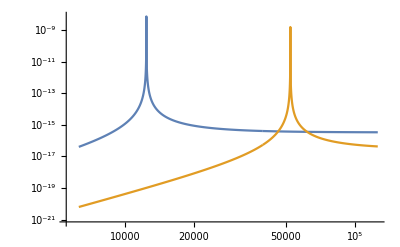

```mathematica
(* integrated power single mode *)
h0Test=10^(-20);
IntegratedSignalPowerValues=Table[{10^myf,h0Test^2*signal power analytic over h0 squared m[hbar*10^myf,w0C,w0C+hbar*10^myf,wmC,Q1C,Q1C,QmC,ηmijC,ΩmC,PinC]},{myf,3.8,5.1,0.0001}];
IntegratedSignalPowerValues2=Table[{10^myf,h0Test^2*signal power analytic over h0 squared m[hbar*10^myf,w0C,w0C+hbar*10^myf,("frequency"/."m2n1l2"/.MODES[[1]])*hbar,Q1C,Q1C,QmC*(("frequency"/."m2n0l2"/.MODES[[1]])*hbar)/(("frequency"/."m2n1l2"/.MODES[[1]])*hbar),ηmijC,gwmechCouplings[[2,2]],PinC]},{myf,3.8,5.1,0.0001}];
ListLogLogPlot[{IntegratedSignalPowerValues,IntegratedSignalPowerValues2},Joined->True,PlotRange->All]
```

```mathematica
x/.Solve[10^x==wmC/hbar,x][[1]]
```

4.09375

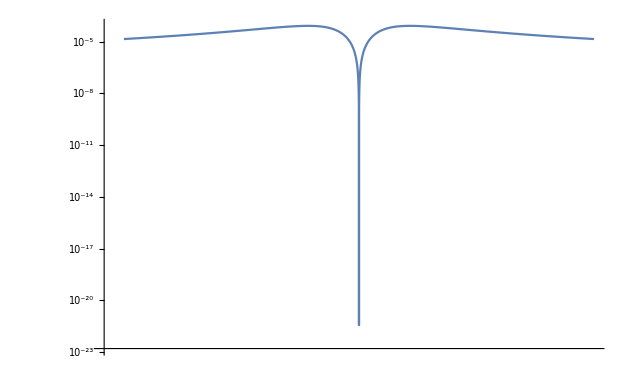

```mathematica
(* integrated power single mode *)
width=10^-6;
h0Test=10^(-20);
IntegratedSignalPowerValues=Table[{10^myf,h0Test^2*signal power analytic over h0 squared m[hbar*10^myf,w0C,w0C+hbar*10^myf,wmC,Q1C,Q1C,QmC,ηmijC,ΩmC,PinC]},{myf,4.0937536103108405-width,4.0937536103108405+width,width*10^-4}];
ListLogLogPlot[{IntegratedSignalPowerValues},Joined->True,PlotRange->All]
```

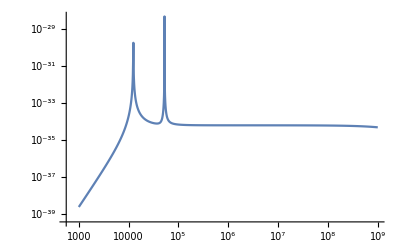

```mathematica
(* total integrated *)
TotalIntegratedSignalPowerValues=Table[{10^myf,ElectricCharge*h0Test^2*signal power analytic over h0 squared[hbar*10^myf,w0C,w0C+hbar*10^myf,Q1C,Q1C,QmC,ηmijC,PinC]},{myf,3,9,0.005}];
ListLogLogPlot[TotalIntegratedSignalPowerValues,Joined->True]
```

#### Plot individual noise functions

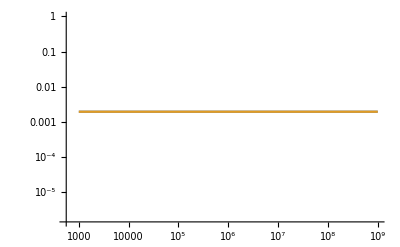

```mathematica
(* thermal EM PSD *)
ThermalEMPSDValues=Table[{10^myf,thermal noise psd[w0C+hbar*10^myf,w0C+hbar*10^myf,Q1C,QintC,TC]},{myf,3,9,0.01}];
ThermalEMPSDValuesold=Table[{10^myf,thermal noise psd[w0C+hbar*10^myf,w0C+hbar*10^myf,Q1C,QintC,TC]},{myf,3,9,0.01}];
ListLogLogPlot[{ThermalEMPSDValues,ThermalEMPSDValuesold},Joined->True]
```

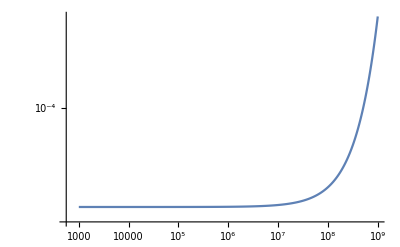

```mathematica
(* thermal EM PSD *)
AmplifierPSDValues=Table[{10^myf,amplifier noise psd[w0C+hbar*10^myf,w0C+hbar*10^myf]},{myf,3,9,0.01}];
ListLogLogPlot[AmplifierPSDValues,Joined->True]
```

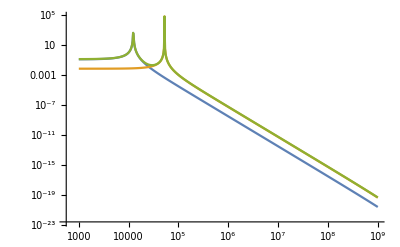

```mathematica
(* thermal Mechanical PSD Single Mode *)
SingleModeThermalMechanicalPSDValues=Table[{10^myf,mechanical mixing noise psd m[w0C+hbar*10^myf,w0C,w0C+hbar*10^myf,wmC,Q1C,Q1C,QmC,ηmijC,ΩmC,PinC,TC,VC,MC]},{myf,3,9,0.01}];
SingleModeThermalMechanicalPSDValues2=Table[{10^myf,mechanical mixing noise psd m[w0C+hbar*10^myf,w0C,w0C+hbar*10^myf,("frequency"/."m2n1l2"/.MODES[[1]])*hbar,Q1C,Q1C,QmC*("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/."m2n1l2"/.MODES[[1]]),ηmijC,gwmechCouplings[[2,2]],PinC,TC,VC,MC]},{myf,3,9,0.01}];
SingleModeThermalMechanicalPSDValues3=Table[{10^myf,mechanical mixing noise psd m[w0C+hbar*10^myf,w0C,w0C+hbar*10^myf,wmC,Q1C,Q1C,QmC,ηmijC,ΩmC,PinC,TC,VC,MC]+mechanical mixing noise psd m[w0C+hbar*10^myf,w0C,w0C+hbar*10^myf,("frequency"/."m2n1l2"/.MODES[[1]])*hbar,Q1C,Q1C,QmC*("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/."m2n1l2"/.MODES[[1]]),ηmijC,gwmechCouplings[[2,2]],PinC,TC,VC,MC]},{myf,3,9,0.01}];
ListLogLogPlot[{SingleModeThermalMechanicalPSDValues,SingleModeThermalMechanicalPSDValues2,SingleModeThermalMechanicalPSDValues3},Joined->True]
```

```mathematica
(* plot all single mode signals *)
SingleModeSignals={};
Module[{i},For[i=0,i<=100,i++,AppendTo[SingleModeSignals,Table[{10^myf,ElectricCharge*mechanical mixing noise psd m[w0C+hbar*10^myf,w0C,w0C+hbar*10^myf,("frequency"/.StringJoin["m2n",ToString[i],"l2"]/.MODES[[1]])*hbar,Q1C,Q1C,QmC*("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/.StringJoin["m2n",ToString[i],"l2"]/.MODES[[1]]),ηmijC,gwmechCouplings[[2,2]],PinC,TC,VC,MC]},{myf,3,9,0.01}]]]];
Print[Length[SingleModeSignals]]
```

101

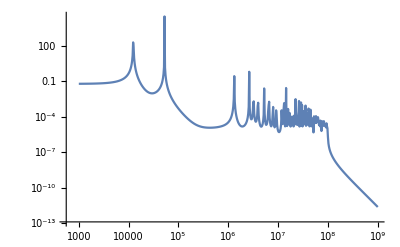

```mathematica
(* thermal Mechanical PSD *)
TotalThermalMechanicalPSDValues=Table[{10^myf,mechanical mixing noise psd[w0C+hbar*10^myf,w0C,w0C+hbar*10^myf,Q1C,Q1C,QmC,ηmijC,PinC,TC,VC,VcavC*rhoC]},{myf,3,9,0.01}];
ListLogLogPlot[TotalThermalMechanicalPSDValues,Joined->True]
```

```mathematica
(* total noise PSD *)
```

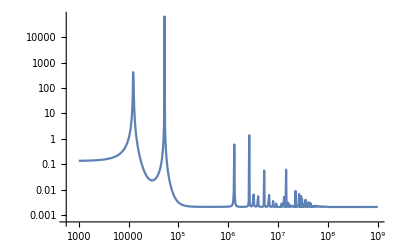

```mathematica
TotalNoisePSDValues=Table[{10^myf, noise psd total[w0C+hbar*10^myf,w0C,w0C+hbar*10^myf,Q1C,Q1C,QmC,QintC,ηmijC,PinC,TC,VC,MC]},{myf,3,9,0.01}];
ListLogLogPlot[TotalNoisePSDValues,Joined->True]
```

#### Plot all noise functions together

```mathematica
totalsignalValuesWHz=Table[{10^myf,10^(-40)*signal power analytic over h0 squared[hbar*10^myf,w0C,w0C+wmC,Q1C,Q1C,QmC,ηmijC,PinC]},{myf,3,9,0.01}];
```

```mathematica
allplots=SingleModeSignals;
ThermalEMPSDValuesWHz=ThermalEMPSDValues;
TotalThermalMechanicalPSDValuesWHz=TotalThermalMechanicalPSDValues;
AmplifierPSDValuesWHz=AmplifierPSDValues;
TotalNoisePSDValuesWHz=TotalNoisePSDValues;

ThermalEMPSDValuesWHz[[All,2]]=ThermalEMPSDValuesWHz[[All,2]]*ElectricCharge/(4*Pi);
TotalThermalMechanicalPSDValuesWHz[[All,2]]=TotalThermalMechanicalPSDValuesWHz[[All,2]]*ElectricCharge;
AmplifierPSDValuesWHz[[All,2]]=AmplifierPSDValuesWHz[[All,2]]*ElectricCharge/(4*Pi);
TotalNoisePSDValuesWHz[[All,2]]=TotalNoisePSDValuesWHz[[All,2]]*ElectricCharge;

PrependTo[allplots,TotalThermalMechanicalPSDValuesWHz];
PrependTo[allplots,ThermalEMPSDValuesWHz];
PrependTo[allplots,AmplifierPSDValuesWHz];
PrependTo[allplots,totalsignalValuesWHz];
Print[Length[allplots]]
myPlotStyle={{Purple,Thick},{Orange,Thick},{RGBColor[9/255,121/255,19/255],Thick},{RGBColor[9/255,54/255,121/255],Thick}};
Module[{i},For[i=0,i<=100,i++,AppendTo[myPlotStyle,{RGBColor[9/255,54/255,121/255],Dashed,Opacity[0.5]}]]];
```

105

```mathematica
(* add in scaling lines for mechanical mixing *)
mechNoiseScalingFunction[frequency_]:=ElectricCharge*mechanical mixing noise psd m[w0C+("frequency"/.StringJoin["m2n",ToString[100],"l2"]/.MODES[[1]])*hbar,w0C,w0C+("frequency"/.StringJoin["m2n",ToString[100],"l2"]/.MODES[[1]])*hbar,("frequency"/.StringJoin["m2n",ToString[100],"l2"]/.MODES[[1]])*hbar,Q1C,Q1C,QmC*("frequency"/."m2n0l2"/.MODES[[1]])/("frequency"/.StringJoin["m2n",ToString[100],"l2"]/.MODES[[1]]),ηmijC,gwmechCouplings[[2,2]],PinC,TC,VC,MC]*(("frequency"/.StringJoin["m2n",ToString[100],"l2"]/.MODES[[1]])/(frequency))^4
```

```mathematica
scalingValues=Table[{10^myf, mechNoiseScalingFunction[10^myf]},{myf,3,9,0.01}];
```

```mathematica
PrependTo[allplots,scalingValues];
PrependTo[myPlotStyle,{RGBColor[9/255,54/255,121/255],Thick,Dashing[{0.02,0.004,0.004,0.004}]}];
```

```mathematica
Print[Length[allplots]]
```

106

```mathematica
PrependTo[allplots,TotalNoisePSDValuesWHz];
PrependTo[myPlotStyle,{Red,Thick}];
```

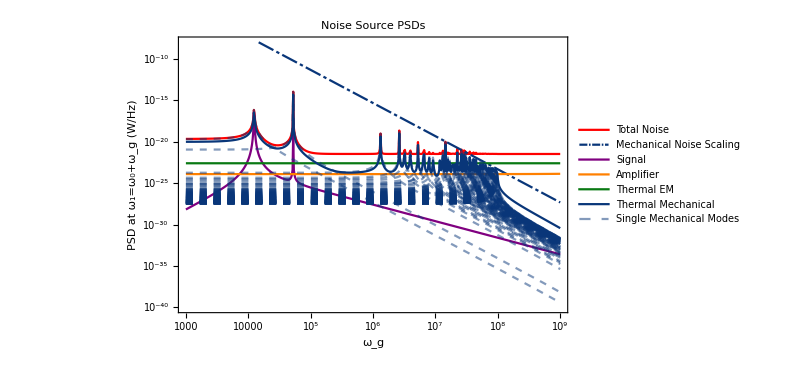

```mathematica
noisesources=ListLogLogPlot[allplots,Joined->True,PlotStyle->myPlotStyle,PlotTheme->"Scientific",PlotLabel->Style["Noise Source PSDs",22],ImageSize->{600,400},PlotLegends->{"Total Noise","Mechanical Noise Scaling","Signal","Amplifier","Thermal EM","Thermal Mechanical","Single Mechanical Modes"},FrameLabel->{Style["ω_g",20],Style["PSD at ω_1=ω_0+ω_g (W/Hz)",20]},PlotRange->{{10^3,10^9},{10^-40,10^-8}}]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/noise-sources.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/noise-sources.png

#### Plot sensitivity

```mathematica
(* total sensitivity *)
SensitivityValues=Table[{10^myf,h0 sensitivity[hbar*10^myf,w0C,w0C+hbar*10^myf,Q1C,Q1C,QmC,QintC,ηmijC,PinC,TC,VC,MC,tintC*(w0C+hbar*10^myf)/(Q1C*hbar*10^myf),bandwidthC]},{myf,3,9,0.001}];
```

```mathematica
scanningSensitivity=SensitivityValues;
```

```mathematica
h0 sensitivity[hbar*10^4,w0C,w0C+hbar*12000,Q1C,Q1C,QmC,QintC,ηmijC,PinC,TC,VC,MC,tintC,bandwidthC]
```

3.30961×10^-18

```mathematica
wmC
```

8.16807×10^-12

```mathematica
fixedmodeSensitivity=Table[{10^myf,h0 sensitivity[hbar*10^myf,w0C,w0C+("frequency"/."m2n0l2"/.MODES[[1]])*hbar,Q1C,Q1C,QmC,QintC,ηmijC,PinC,TC,VC,MC,tintC,bandwidthC]},{myf,3,9,0.01}];
```

```mathematica
pbh parameter space[mp_,wp_]:=10*^-31 * (mp/10^-11)^(4/3)*(wp/10^9)^(2/3)
```

```mathematica
pbh5=Table[{10^myf,pbh parameter space[10^-5,10^myf]},{myf,3,8.2,0.005}];
pbh6=Table[{10^myf,pbh parameter space[10^-6,10^myf]},{myf,3,8.2,0.005}];
pbh8=Table[{10^myf,pbh parameter space[10^-8,10^myf]},{myf,3,9,0.005}];
pbh11=Table[{10^myf,pbh parameter space[10^-11,10^myf]},{myf,3,9,0.005}];
```

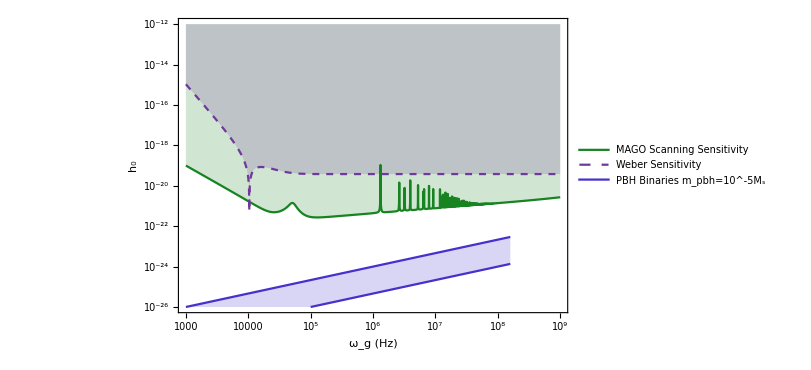

```mathematica
ListLogLogPlot[{scanningSensitivity,WeberSensitivityValues,pbh5,pbh6},Joined->True,PlotStyle->{{RGBColor[23/255,131/255,33/255]},{RGBColor[113/255,56/255,156/255],Dashed},{RGBColor[69/255,49/255,203/255]},{RGBColor[69/255,49/255,203/255]}},PlotTheme->"Scientific",FrameLabel->{Style["ω_g (Hz)",25],Style["h_0",25]},Filling->{1->Top,2->Top,3->{4}},FillingStyle->{{RGBColor[255/255,84/255,26/255]},Directive[RGBColor[113/255,56/255,156/255],Dashing[0.1]],{RGBColor[69/255,49/255,203/255]}},ImageSize->{600,400},PlotLegends->Placed[{Style["MAGO Scanning Sensitivity",18],Style["Weber Sensitivity",18],Style["PBH Binaries m_pbh=10^-5M_s",18]},{0.75,0.83}],PlotRange->{{10^3,10^9},{10^-26,10^-12}}]
```

```mathematica
Export["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/sensitivity-whoa.png",%,"PNG"]
```

/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/figures/sensitivity-whoa.png

### Overlap picture

#### <Mechanical mode>

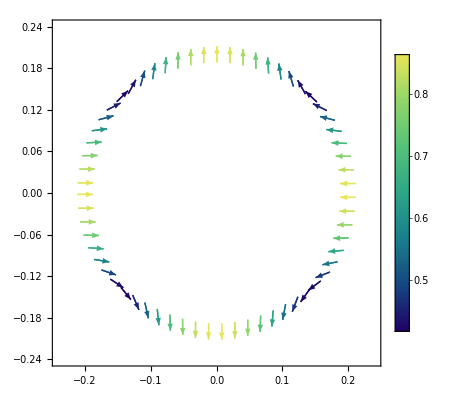

```mathematica
spherevec2cartvec[A_,p_]:={A[[1]]*Sin[p[[2]]]*Cos[p[[3]]]+A[[2]]*Cos[p[[2]]]*Cos[p[[3]]]-A[[3]]*Sin[p[[3]]],A[[1]]*Sin[p[[2]]]*Sin[p[[3]]]+A[[2]]*Cos[p[[2]]]*Sin[p[[3]]]+A[[3]]*Cos[p[[3]]],A[[1]]*Cos[p[[2]]]-A[[2]]*Sin[p[[2]]]}
mvec={2,0,2};
z=0.1;
coefs=Quiet[{"C0","D0",0.0,0.0,"C2","D2"}/.(StringJoin["m",ToString[mvec[[1]]],"n",ToString[mvec[[2]]],"l",ToString[mvec[[3]]]]/.MODES[[1]])];
myModeVectors=Table[{{FromSphericalCoordinates[{Sqrt[r^2+z^2],ArcTan[Sqrt[r^2]/z],phi}][[1]],FromSphericalCoordinates[{Sqrt[r^2+z^2],ArcTan[Sqrt[r^2]/z],phi}][[2]]},spherevec2cartvec[Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],Sqrt[r^2+z^2],ArcTan[Sqrt[r^2]/z],phi,0.0,0.0,0.0]]],{Sqrt[r^2+z^2],ArcTan[Sqrt[r^2]/z],phi}][[1;;2]]},{r,innerRadius,outerRadius,0.1},{phi,-Pi+0.01,Pi,0.1}];
mechanicalModes=ListVectorPlot[myModeVectors,VectorPoints->All,VectorMarkers->"Arrow",VectorSizes->Small,PlotLegends->Automatic,VectorColorFunction->"BlueGreenYellow",PlotRange->{{-innerRadius*1.2,innerRadius*1.2},{-innerRadius*1.2,innerRadius*1.2}}]
```

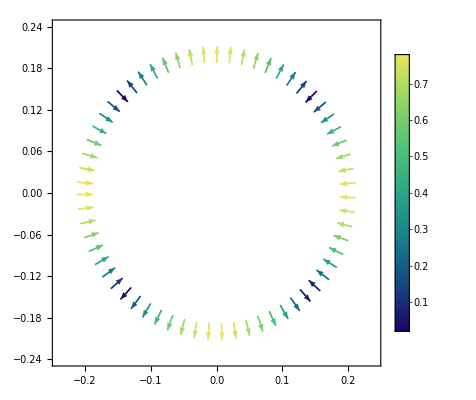

```mathematica
mechanicalModes=ListVectorPlot[myModeVectors,VectorPoints->All,VectorMarkers->"Arrow",VectorSizes->Small,PlotLegends->Automatic,VectorColorFunction->"BlueGreenYellow",PlotRange->{{-innerRadius*1.2,innerRadius*1.2},{-innerRadius*1.2,innerRadius*1.2}}]
```

```mathematica
z = 0.0;
radialValsPerturbed = Table[FromPolarCoordinates[{innerRadius+0.02*Re[Activate[displacementVecQ[mvec[[1]],mvec[[2]],mvec[[3]],innerRadius,coefs[[1]],coefs[[2]],coefs[[3]],coefs[[4]],coefs[[5]],coefs[[6]],Sqrt[innerRadius^2+z^2],ArcTan[z,Sqrt[innerRadius^2]],phi,0.0,0.0,0.0][[1]]]],phi}],{phi,-Pi+0.01,Pi,0.05}];
radialValsUnPerturbed = Table[FromPolarCoordinates[{innerRadius,phi}],{phi,-Pi+0.01,Pi,0.05}];
```

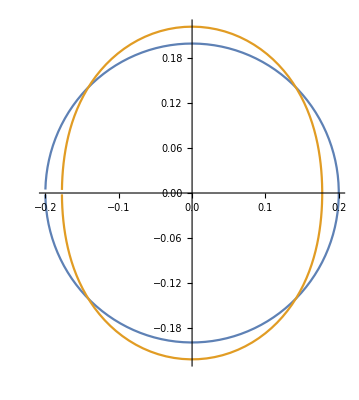

```mathematica
ListPlot[{radialValsUnPerturbed,radialValsPerturbed},Joined->True,AspectRatio->Equal]
```

#### <EM modes>

```mathematica
emvals1=Table[{{FromSphericalCoordinates[{Sqrt[r^2+z^2],ArcTan[z,Sqrt[r^2]],phi}][[1]],FromSphericalCoordinates[{Sqrt[r^2+z^2],ArcTan[z,Sqrt[r^2]],phi}][[2]]},Re[spherevec2cartvec[Activate[electricField[1.0,1,0, 0,1,2,innerRadius,Activate[wavenumberEM[0,1,2,innerRadius,0]],Sqrt[r^2+z^2],ArcTan[z,Sqrt[r^2]],phi,0.0,Pi/4.0,0.0]],{Sqrt[r^2+z^2],ArcTan[z,Sqrt[r^2]],phi}][[1;;2]]]},{r,0.001,Sqrt[innerRadius^2-z^2],0.01},{phi,-Pi+0.01,Pi,0.1}]
emvals2=Table[{{FromSphericalCoordinates[{Sqrt[r^2+z^2],ArcTan[z,Sqrt[r^2]],phi}][[1]],FromSphericalCoordinates[{Sqrt[r^2+z^2],ArcTan[z,Sqrt[r^2]],phi}][[2]]},Re[spherevec2cartvec[Activate[electricField[1.0,1,0, 0,1,2,innerRadius,Activate[wavenumberEM[0,1,2,innerRadius,0]],Sqrt[r^2+z^2],ArcTan[z,Sqrt[r^2]],phi,0.0,-Pi/4.0,0.0]],{Sqrt[r^2+z^2],ArcTan[z,Sqrt[r^2]],phi}][[1;;2]]]},{r,0.001,Sqrt[innerRadius^2-z^2],0.01},{phi,-Pi+0.01,Pi,0.1}]
```

{{{{-0.00099995,-9.99983×10^-6},{-0.0000910279,0.00910248}},{{-0.000993956,-0.000109778},{-0.000999305,0.00904792}},{{-0.000978031,-0.00020846},{-0.0018976,0.00890296}},58,{{-0.000985041,0.000172321},{0.00156863,0.00896677}},{{-0.000997323,0.00007312},{0.000665607,0.00907857}}},18,{{{-0.19099,-0.00190997},{23,1}},62}}
 |  |  |  |

{{{{-0.00099995,-9.99983×10^-6},{-0.0000910279,0.00910248}},{{-0.000993956,-0.000109778},{-0.000999305,0.00904792}},{{-0.000978031,-0.00020846},{-0.0018976,0.00890296}},58,{{-0.000985041,0.000172321},{0.00156863,0.00896677}},{{-0.000997323,0.00007312},{0.000665607,0.00907857}}},18,{{{-0.19099,-0.00190997},{23,1}},62}}
 |  |  |  |

```mathematica
z=0.0
emnorm1=Table[{FromSphericalCoordinates[{Sqrt[r^2+z^2],ArcTan[z,Sqrt[r^2]],phi}][[1]],FromSphericalCoordinates[{Sqrt[r^2+z^2],ArcTan[z,Sqrt[r^2]],phi}][[2]],Log[Norm[Re[Activate[electricField[1.0,1,0, 0,1,2,innerRadius,Activate[wavenumberEM[0,1,2,innerRadius,0]],Sqrt[r^2+z^2],ArcTan[z,Sqrt[r^2]],phi,0.0,Pi/4.0,0.0]]]]^2]},{r,0.001,Sqrt[innerRadius^2-z^2],0.01},{phi,-Pi+0.01,Pi,0.1}]
emnorm2=Table[{FromSphericalCoordinates[{Sqrt[r^2+z^2],ArcTan[z,Sqrt[r^2]],phi}][[1]],FromSphericalCoordinates[{Sqrt[r^2+z^2],ArcTan[z,Sqrt[r^2]],phi}][[2]],Log[Norm[Re[Activate[electricField[1.0,1,0, 0,1,2,innerRadius,Activate[wavenumberEM[0,1,2,innerRadius,0]],Sqrt[r^2+z^2],ArcTan[z,Sqrt[r^2]],phi,0.0,-Pi/4.0,0.0]]]]^2]},{r,0.001,Sqrt[innerRadius^2-z^2],0.01},{phi,-Pi+0.01,Pi,0.1}]
```

0.

{{{-0.00099995,-9.99983×10^-6,-9.39822},{-0.000993956,-0.000109778,-9.38634},{-0.000978031,-0.00020846,-9.35578},{-0.000952334,-0.000305059,-9.30933},55,{-0.000931171,0.000364583,-9.27352},{-0.000962916,0.0002698,-9.32805},{-0.000985041,0.000172321,-9.36905},{-0.000997323,0.00007312,-9.39298}},18,{1}}
 |  |  |  |

{{{-0.00099995,-9.99983×10^-6,-9.39822},{-0.000993956,-0.000109778,-9.38634},{-0.000978031,-0.00020846,-9.35578},{-0.000952334,-0.000305059,-9.30933},55,{-0.000931171,0.000364583,-9.27352},{-0.000962916,0.0002698,-9.32805},{-0.000985041,0.000172321,-9.36905},{-0.000997323,0.00007312,-9.39298}},18,{1}}
 |  |  |  |

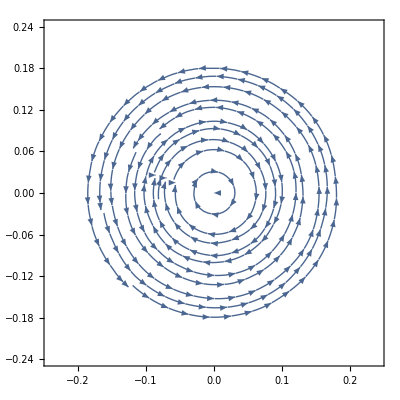

-Graphics-

```mathematica
em1=ListStreamPlot[emvals1,PlotLegends->Automatic,StreamColorFunction->Black,RegionFunction->Function[{x,y},Sqrt[x^2+y^2]<Sqrt[innerRadius^2-z^2]],PlotRange->{{-innerRadius*1.2,innerRadius*1.2},{-innerRadius*1.2,innerRadius*1.2}},RegionFillingStyle->None,RegionBoundaryStyle->None,StreamPoints->19]
em2=ListStreamPlot[emvals2,PlotLegends->Automatic,StreamColorFunction->"BlueGreenYellow",RegionFunction->Function[{x,y},Sqrt[(x-2.3*innerRadius)^2+y^2]<Sqrt[innerRadius^2-z^2]],PlotRange->{{1.3*innerRadius,innerRadius*3.7},{-innerRadius*1.2,innerRadius*1.2}},RegionFillingStyle->None,RegionBoundaryStyle->None,StreamPoints->Coarse]
```

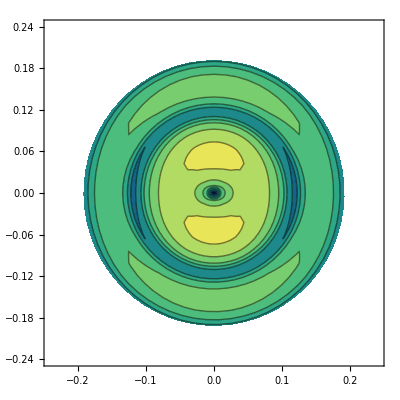

-Graphics-

```mathematica
density1=ListContourPlot[Flatten[emnorm1,1],ColorFunction->"BlueGreenYellow",ColorFunctionScaling->True,PlotRange->{{-innerRadius*1.2,innerRadius*1.2},{-innerRadius*1.2,innerRadius*1.2}}]
density2=ListContourPlot[Flatten[emnorm2,1],ColorFunction->"BlueGreenYellow",PlotRange->{{-innerRadius*1.2,innerRadius*1.2},{-innerRadius*1.2,innerRadius*1.2}}]
```

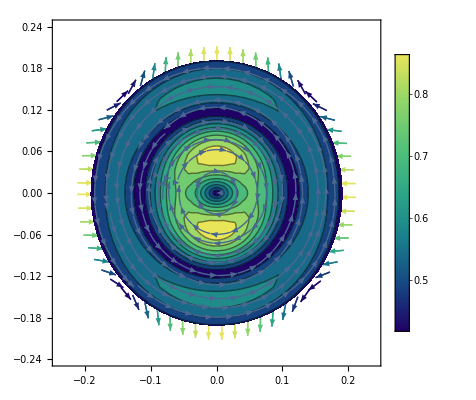

```mathematica
Show[mechanicalModes,density,em1]
```

```mathematica
emvalssurface=Table[{phi,Norm[Re[Activate[electricField[1.0,1,0, 0,1,2,innerRadius,Activate[wavenumberEM[0,1,2,innerRadius,0]],Sqrt[innerRadius^2+z^2],ArcTan[z,Sqrt[innerRadius^2]],phi,0.0,Pi/4.0,0.0]]]]},{phi,-Pi+0.01,Pi,0.1}]
```

{{-3.13159,3.35317×10^-9},{-3.03159,3.37315×10^-9},{-2.93159,3.42508×10^-9},{-2.83159,3.50555×10^-9},{-2.73159,3.60957×10^-9},{-2.63159,3.73121×10^-9},{-2.53159,3.86422×10^-9},{-2.43159,4.00243×10^-9},{-2.33159,4.1401×10^-9},{-2.23159,4.27204×10^-9},{-2.13159,4.39374×10^-9},{-2.03159,4.50137×10^-9},{-1.93159,4.59175×10^-9},{-1.83159,4.66238×10^-9},{-1.73159,4.71138×10^-9},{-1.63159,4.73748×10^-9},{-1.53159,4.74004×10^-9},{-1.43159,4.71898×10^-9},{-1.33159,4.67484×10^-9},{-1.23159,4.60875×10^-9},{-1.13159,4.52244×10^-9},{-1.03159,4.41829×10^-9},{-0.931593,4.29933×10^-9},{-0.831593,4.16924×10^-9},{-0.731593,4.03239×10^-9},{-0.631593,3.89383×10^-9},{-0.531593,3.75918×10^-9},{-0.431593,3.63455×10^-9},{-0.331593,3.52621×10^-9},{-0.231593,3.44019×10^-9},{-0.131593,3.38174×10^-9},{-0.0315927,3.35468×10^-9},{0.0684073,3.36083×10^-9},{0.168407,3.39978×10^-9},{0.268407,3.46891×10^-9},{0.368407,3.56381×10^-9},{0.468407,3.67887×10^-9},{0.568407,3.80792×10^-9},{0.668407,3.9447×10^-9},{0.768407,4.08325×10^-9},{0.868407,4.21816×10^-9},{0.968407,4.34463×10^-9},{1.06841,4.45853×10^-9},{1.16841,4.55643×10^-9},{1.26841,4.63554×10^-9},{1.36841,4.69372×10^-9},{1.46841,4.72946×10^-9},{1.56841,4.74185×10^-9},{1.66841,4.73059×10^-9},{1.76841,4.69595×10^-9},{1.86841,4.63881×10^-9},{1.96841,4.56065×10^-9},{2.06841,4.4636×10^-9},{2.16841,4.35039×10^-9},{2.26841,4.22443×10^-9},{2.36841,4.08982×10^-9},{2.46841,3.95132×10^-9},{2.56841,3.81433×10^-9},{2.66841,3.68477×10^-9},{2.76841,3.56889×10^-9},{2.86841,3.4729×10^-9},{2.96841,3.40242×10^-9},{3.06841,3.36195×10^-9}}

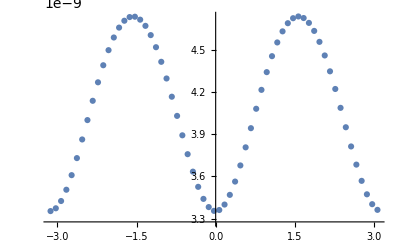

```mathematica
ListPlot[emvalssurface]
```

```mathematica
emvals1=Table[{{FromSphericalCoordinates[{Sqrt[r^2+z^2],ArcTan[Sqrt[r^2]/z],phi}][[1]],FromSphericalCoordinates[{Sqrt[r^2+z^2],ArcTan[Sqrt[r^2]/z],phi}][[2]]},Re[spherevec2cartvec[Activate[electricField[1.0,1,0, 0,1,2,innerRadius,Activate[wavenumberEM[0,1,2,innerRadius,0]],Sqrt[r^2+z^2],ArcTan[Sqrt[r^2]/z],phi,0.0,Pi/4.0,0.0]],{Sqrt[r^2+z^2],ArcTan[Sqrt[r^2]/z],phi}][[1;;2]]]},{r,0.001,Sqrt[innerRadius^2-z^2],0.01},{phi,-Pi+0.01,Pi,0.1}]
```

```mathematica
emnorm3d=Table[{FromSphericalCoordinates[{r,theta,phi}][[1]],FromSphericalCoordinates[{r,theta,phi}][[2]],FromSphericalCoordinates[{r,theta,phi}][[3]],Norm[Re[Activate[electricField[1.0,1,0, 0,1,2,innerRadius,Activate[wavenumberEM[0,1,2,innerRadius,0]],r,theta,phi,0.0,Pi/4.0,0.0]]]]},{r,0.001,innerRadius,0.01},{theta,0.01,Pi,0.2},{phi,-Pi+0.01,Pi,0.2}]
```

{{{{-9.99933×10^-6,-9.99967×10^-8,0.00099995,0.00919351},{-9.78015×10^-6,-2.08456×10^-6,0.00099995,0.00919155},{-9.17106×10^-6,-3.98603×10^-6,0.00099995,0.00918611},{-8.19634×10^-6,-5.72858×10^-6,0.00099995,0.00917739},{-6.89487×10^-6,-7.24275×10^-6,0.00099995,0.00916572},{-5.31852×10^-6,-8.46818×10^-6,0.00099995,0.00915155},20,{-4.7732×10^-6,8.78711×10^-6,0.00099995,0.00914663},{-6.42378×10^-6,7.66366×10^-6,0.00099995,0.00916149},{-7.81827×10^-6,6.23469×10^-6,0.00099995,0.009174},{-8.90106×10^-6,4.55716×10^-6,0.00099995,0.0091837},{-9.629×10^-6,2.69795×10^-6,0.00099995,0.0091902},{-9.97307×10^-6,7.31188×10^-7,0.00099995,0.00919327}},14,{1}},19}
 |  |  |  |

```mathematica
ListContourPlot3D[Flatten[emnorm3d,2],Contours->5]
```

-Graphics3D-

```mathematica
cartvec = Simplify[spherevec2cartvec[{Ar,Aθ,Aϕ},{r,θ,ϕ}]]
```

{Aθ Cos[θ] Cos[ϕ]+Ar Cos[ϕ] Sin[θ]-Aϕ Sin[ϕ],Aϕ Cos[ϕ]+(Aθ Cos[θ]+Ar Sin[θ]) Sin[ϕ],Ar Cos[θ]-Aθ Sin[θ]}

```mathematica
TeXForm[cartvec[[2]]]
```

\sin (\phi ) (\text{A$\theta $} \cos (\theta )+\text{Ar} \sin (\theta ))+\text{A$\phi $} \cos (\phi )

```mathematica
?electricField
```

```mathematica
Simplify[Cross[electricField[1,1,1,m,n,p,1,wavenumberEM[m,n,p,1,1],1,θ,ϕ,0,0,0],magneticField[1,1,1,m,n,p,1,wavenumberEM[m,n,p,1,1],1,θ,ϕ,0,0,0]]]
```

{-1/(16 SphericalBesselJDerivZero[n,p])Csc[θ]^2 (1) SphericalBesselJ[n,SphericalBesselJDerivZero[n,p]] (SphericalBesselJ[n,SphericalBesselJDerivZero[n,p]]+(SphericalBesselJ[-1+n,SphericalBesselJDerivZero[n,p]]-SphericalBesselJ[1+n,SphericalBesselJDerivZero[n,p]]) SphericalBesselJDerivZero[n,p]),(Cos[m 1]^2 1^4 2 √1 1^2)/(2 SphericalBesselJDerivZero[n,p]),(m Csc[θ]^2 LegendreP[1] (1) Sin[2 m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]] SphericalBesselJ[n,SphericalBesselJDerivZero[n,p]]^2)/(4 √(Sin[θ]^2) SphericalBesselJDerivZero[n,p])}
 |  |  |  |

```mathematica
poynting=%;
```

```mathematica
poynting[[1]]
```

-1/(16 SphericalBesselJDerivZero[n,p])Csc[θ]^2 ((2+4 m^2+4 n+2 n^2+2 (1+n)^2 Cos[2 θ]+(-4 m^2+2 (1+n)^2) Cos[2 m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]]+Cos[2 θ-2 m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]]+2 n Cos[2 θ-2 m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]]+n^2 Cos[2 θ-2 m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]]+Cos[2 (θ+m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]])]+2 n Cos[2 (θ+m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]])]+n^2 Cos[2 (θ+m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]])]) LegendreP[n,m,Cos[θ]]^2+16 (-1+m-n) (1+n) Cos[θ] Cos[m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]]^2 LegendreP[n,m,Cos[θ]] LegendreP[1+n,m,Cos[θ]]+8 (1-m+n)^2 Cos[m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]]^2 LegendreP[1+n,m,Cos[θ]]^2) SphericalBesselJ[n,SphericalBesselJDerivZero[n,p]] (SphericalBesselJ[n,SphericalBesselJDerivZero[n,p]]+(SphericalBesselJ[-1+n,SphericalBesselJDerivZero[n,p]]-SphericalBesselJ[1+n,SphericalBesselJDerivZero[n,p]]) SphericalBesselJDerivZero[n,p])

```mathematica
Activate[Simplify[Cross[electricField[1,1,1,0,2,2,1,wavenumberEM[m,n,p,1,0],1,θ,ϕ,0,0,0],magneticField[1,1,0,0,1,2,1,wavenumberEM[0,1,2,1,0],1,θ,ϕ,0,0,0]]]]
```

{0,0,0.0125671 √(Sin[θ]^2) (6.94817×10^-16 Cos[θ]^2+0.254625 (1+3 Cos[2 θ])-9.48372×10^-9 (1.28375 Cos[θ]^2-0.128375 Sin[θ]^2))}

```mathematica
sphericalBesselJDerivZero//TableForm//TeXForm
```

\begin{array}{cccccccccc}
 1.5708 & 4.71239 & 7.85398 & 10.9956 & 14.1372 & 17.2788 & 20.4204 & 23.5619 & 26.7035 & 29.8451 \\
 0. & 2.74371 & 6.11676 & 15.6439 & 9.31662 & 18.7963 & 12.4859 & 21.9455 & 25.0928 & 28.2389 \\
 0. & 3.87024 & 10.713 & 7.44309 & 13.9205 & 17.1027 & 20.272 & 23.4337 & 26.5906 & 29.7442 \\
 0. & 4.97342 & 8.72175 & 12.0636 & 15.3136 & 18.5242 & 21.7139 & 24.8911 & 28.0601 & \text{} \\
 0. & 6.06195 & 9.96755 & 13.3801 & 16.6742 & 19.9154 & 23.1278 & 26.3224 & 29.5054 & \text{} \\
 0. & 7.14023 & 11.189 & 14.6701 & 18.0085 & 21.2815 & 24.5178 & 27.7313 & \text{} & \text{} \\
 0. & 8.21084 & 12.3915 & 15.9387 & 19.3212 & 22.6263 & 25.8873 & 29.1205 & \text{} & \text{} \\
 0. & 9.27546 & 13.5787 & 17.1896 & 20.6154 & 23.9528 & 27.239 & \text{} & \text{} & \text{} \\
 0. & 10.3352 & 14.7534 & 18.4254 & 21.8939 & 25.2633 & 28.5749 & \text{} & \text{} & \text{} \\
 0. & 11.391 & 15.9174 & 19.6485 & 23.1586 & 26.5598 & 29.8967 & \text{} & \text{} & \text{} \\
\end{array}

```mathematica
Bfieldold = FullSimplify[magneticField[f,1,0,m,n,p,a,k,r,θ,ϕ,0,0,0],Assumptions->{r>0,θ>=0,θ<Pi}]
```

{-1/(2 k r)f Cos[m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]] Csc[θ]^2 ((2-2 m^2+3 n+n^2+n (1+n) Cos[2 θ]) LegendreP[n,m,Cos[θ]]+2 (-1+m-n) ((3+2 n) Cos[θ] LegendreP[1+n,m,Cos[θ]]+(-2+m-n) LegendreP[2+n,m,Cos[θ]])) SphericalBesselJ[n,k r],-1/(k r)f Cos[m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]] Csc[θ] ((1+n) Cos[θ] LegendreP[n,m,Cos[θ]]+(-1+m-n) LegendreP[1+n,m,Cos[θ]]) ((1+n) SphericalBesselJ[n,k r]-k r SphericalBesselJ[1+n,k r]),-(f m Csc[θ] LegendreP[n,m,Cos[θ]] Sin[m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]] ((1+n) SphericalBesselJ[n,k r]-k r SphericalBesselJ[1+n,k r]))/(k r)}

```mathematica
Bfield[[1]]//TraditionalForm
```

-(f csc^2(θ) nk r ((-2 m^2+n^2+n (n+1) cos(2 θ)+3 n+2) nmcos(θ)+2 (m-n-1) ((2 n+3) cos(θ) n+1mcos(θ)+(m-n-2) n+2mcos(θ))) cos(m tan^-1(sin(θ) cos(ϕ),sin(θ) sin(ϕ))))/(2 k r)

```mathematica
Bfieldnew= FullSimplify[magneticField[f,1,0,m,n,p,a,k,r,θ,ϕ,0,0,0],Assumptions->{r>0,θ>=0,θ<Pi}]
```

{-1/(2 k r)f Cos[m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]] Csc[θ]^2 ((2-2 m^2+3 n+n^2+n (1+n) Cos[2 θ]) LegendreP[n,m,Cos[θ]]+2 (-1+m-n) ((3+2 n) Cos[θ] LegendreP[1+n,m,Cos[θ]]+(-2+m-n) LegendreP[2+n,m,Cos[θ]])) SphericalBesselJ[n,k r],1/(k r)f Cos[m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]] (-((1+n) Cot[θ] LegendreP[n,m,Cos[θ]])+(1-m+n) Csc[θ] LegendreP[1+n,m,Cos[θ]]) Sign[Csc[θ]] ((1+n) SphericalBesselJ[n,k r]-k r SphericalBesselJ[1+n,k r]),-(f m Csc[θ] LegendreP[n,m,Cos[θ]] Sin[m ArcTan[Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ]]] ((1+n) SphericalBesselJ[n,k r]-k r SphericalBesselJ[1+n,k r]))/(k r)}

```mathematica
FullSimplify[Bfieldold[[1]]]//TraditionalForm
```

-(f csc^2(θ) nk r ((-2 m^2+n^2+n (n+1) cos(2 θ)+3 n+2) nmcos(θ)+2 (m-n-1) ((2 n+3) cos(θ) n+1mcos(θ)+(m-n-2) n+2mcos(θ))) cos(m tan^-1(sin(θ) cos(ϕ),sin(θ) sin(ϕ))))/(2 k r)

```mathematica
FullSimplify[(2-2*m^2+3*n+n^2+n*(1+n)*Cos[2*θ])*LegendreP[n,m,Cos[θ]]+2*(-1+m-n)*((3+2*n)*Cos[θ]*LegendreP[1+n,m,Cos[θ]]+(-2+m-n)*LegendreP[2+n,m,Cos[θ]])]//TraditionalForm
```

(-2 m^2+n^2+n (n+1) cos(2 θ)+3 n+2) nmcos(θ)+2 (m-n-1) ((2 n+3) cos(θ) n+1mcos(θ)+(m-n-2) n+2mcos(θ))

```mathematica
filename=StringJoin["eta-",ToString[200],"-012-012-EMpol-pion4pion4-minpion4pion4-0-variable-mechanical-euler-alpha-beta-hi-res-GWplus-newsigns.txt"];
(* import data *)

(* name data floats *)
For[i=1,i<=Length[overlaps],i++,overlaps[[i]]=ToExpression[overlaps[[i]]]];
(* covert first two points to aitoff projection *)
overlapsSpherical={};
For[i=1,i<Length[overlaps],i++,AppendTo[overlapsSpherical,{overlaps[[i,1]],overlaps[[i,2]],Abs[overlaps[[i,3]]]/((32*8*Pi/3)^(1/3))}]&@@euler2spherical[overlaps[[i,1]],overlaps[[i,2]],0.0]];
```

```mathematica
overlapsSpherical
```

{{0.01,-3.13159,0.0514715},{0.01,-3.03159,0.0514728},{0.01,-2.93159,0.0510532},{0.01,-2.83159,0.0525634},{0.01,-2.73159,0.0452514},{0.01,-2.63159,0.0487506},{0.01,-2.53159,0.0508667},{0.01,-2.43159,0.0466596},{0.01,-2.33159,0.0469519},{0.01,-2.23159,0.0420965},{0.01,-2.13159,0.0404165},{0.01,-2.03159,0.04079},{0.01,-1.93159,0.0430498},{0.01,-1.83159,0.0527355},{0.01,-1.73159,0.0609038},{0.01,-1.63159,0.0679025},{0.01,-1.53159,0.0745204},{0.01,-1.43159,0.0856176},{0.01,-1.33159,0.0970298},{0.01,-1.23159,0.108656},{0.01,-1.13159,0.121781},{0.01,-1.03159,0.130203},{0.01,-0.931593,0.146892},{0.01,-0.831593,0.160369},{0.01,-0.731593,0.171999},{0.01,-0.631593,0.182991},{0.01,-0.531593,0.20144},{0.01,-0.431593,0.214097},{0.01,-0.331593,0.21723},{0.01,-0.231593,0.221862},{0.01,-0.131593,0.22732},{0.01,-0.0315927,0.226306},{0.01,0.0684073,0.229011},{0.01,0.168407,0.225292},{0.01,0.268407,0.218279},{0.01,0.368407,0.217001},{0.01,0.468407,0.205516},{0.01,0.568407,0.200479},{0.01,0.668407,0.184754},{0.01,0.768407,0.172882},{0.01,0.868407,0.158297},{0.01,0.968407,0.14022},{0.01,1.06841,0.128975},{0.01,1.16841,0.116107},{0.01,1.26841,0.104906},{0.01,1.36841,0.0905215},{0.01,1.46841,0.0799991},{0.01,1.56841,0.0694948},{0.01,1.66841,0.0638293},{0.01,1.76841,0.0598982},{0.01,1.86841,0.0521484},{0.01,1.96841,0.0453277},{0.01,2.06841,0.0432129},{0.01,2.16841,0.0446645},{0.01,2.26841,0.044346},{0.01,2.36841,0.0495516},{0.01,2.46841,0.0483699},{0.01,2.56841,0.0484799},{0.01,2.66841,0.0494587},{0.01,2.76841,0.0501749},{0.01,2.86841,0.0517916},{0.01,2.96841,0.055584}}

```mathematica
ListContourPlot[overlapsSpherical,Contours->7]
```

-Graphics-

```mathematica
overlaps
```

{{0.01,-3.13159,-0.331887},{0.01,-3.03159,-0.331895},{0.01,-2.93159,-0.329189},{0.01,-2.83159,-0.338927},{0.01,-2.73159,-0.291779},{0.01,-2.63159,-0.314343},{0.01,-2.53159,-0.327987},{0.01,-2.43159,-0.30086},{0.01,-2.33159,-0.302744},{0.01,-2.23159,-0.271437},{0.01,-2.13159,-0.260605},{0.01,-2.03159,-0.263013},{0.01,-1.93159,-0.277584},{0.01,-1.83159,-0.340037},{0.01,-1.73159,-0.392706},{0.01,-1.63159,-0.437833},{0.01,-1.53159,-0.480505},{0.01,-1.43159,-0.55206},{0.01,-1.33159,-0.625645},{0.01,-1.23159,-0.700613},{0.01,-1.13159,-0.785243},{0.01,-1.03159,-0.839542},{0.01,-0.931593,-0.947157},{0.01,-0.831593,-1.03406},{0.01,-0.731593,-1.10904},{0.01,-0.631593,-1.17992},{0.01,-0.531593,-1.29888},{0.01,-0.431593,-1.38049},{0.01,-0.331593,-1.40069},{0.01,-0.231593,-1.43056},{0.01,-0.131593,-1.46575},{0.01,-0.0315927,-1.45921},{0.01,0.0684073,-1.47666},{0.01,0.168407,-1.45267},{0.01,0.268407,-1.40746},{0.01,0.368407,-1.39921},{0.01,0.468407,-1.32516},{0.01,0.568407,-1.29268},{0.01,0.668407,-1.19129},{0.01,0.768407,-1.11474},{0.01,0.868407,-1.02069},{0.01,0.968407,-0.904134},{0.01,1.06841,-0.831627},{0.01,1.16841,-0.748656},{0.01,1.26841,-0.676428},{0.01,1.36841,-0.58368},{0.01,1.46841,-0.515832},{0.01,1.56841,-0.4481},{0.01,1.66841,-0.411569},{0.01,1.76841,-0.386222},{0.01,1.86841,-0.336251},{0.01,1.96841,-0.292272},{0.01,2.06841,-0.278636},{0.01,2.16841,-0.287995},{0.01,2.26841,-0.285941},{0.01,2.36841,-0.319507},{0.01,2.46841,-0.311888},{0.01,2.56841,-0.312597},{0.01,2.66841,-0.318908},{0.01,2.76841,-0.323526},{0.01,2.86841,-0.33395},{0.01,2.96841,-0.358404},{0.01,3.06841,-0.328005}}

```mathematica
MODES
```

{"m2n0l0" -> {"wavenumberk" -> 1.7898104373825392, "wavenumberp" -> 0.7832120526949411, "frequency" -> 2817.1171370551683, "C0" -> 2.187854422191361, 
   "C2" -> 0.00007288525020600044, "D0" -> 0.14064870856014164, "D2" -> -0.0016763116094842038}, 
 "m2n0l1" -> {"wavenumberk" -> 1.7898104373825392, "wavenumberp" -> 0.7832120526949411, "frequency" -> 2817.1171370551683, "C0" -> 2.1871795995800207, 
   "C2" -> 0.00007286276945299726, "D0" -> 0.1406053268214713, "D2" -> -0.0016757945673235104}, 
 "m2n0l2" -> {"wavenumberk" -> 1.7898104373825392, "wavenumberp" -> 0.7832120526949411, "frequency" -> 2817.1171370551683, "C0" -> 2.7301393096411153, 
   "C2" -> 0.0000914145055749922, "D0" -> 0.17559037861002963, "D2" -> -0.002086356990172635}, 
 "m2n1l0" -> {"wavenumberk" -> 5.218196274887195, "wavenumberp" -> 2.283456465812297, "frequency" -> 4810.18292742585, "C0" -> 2.742256905256485, 
   "C2" -> 0.9136662957787578, "D0" -> -0.45444949931493, "D2" -> 0.6993944473689281}, 
 "m2n1l1" -> {"wavenumberk" -> 5.218196274887195, "wavenumberp" -> 2.283456465812297, "frequency" -> 4810.18292742585, "C0" -> 2.7343377577490613, 
   "C2" -> 0.9110277909198716, "D0" -> -0.45313713043626974, "D2" -> 0.6973747212871116}, 
 "m2n1l2" -> {"wavenumberk" -> 5.218196274887195, "wavenumberp" -> 2.283456465812297, "frequency" -> 4810.18292742585, "C0" -> 0.00019848543540139832, 
   "C2" -> 0.00006596031100592674, "D0" -> -0.000032991787061125105, "D2" -> 0.000050229132008137565}, 
 "m2n2l0" -> {"wavenumberk" -> 314.17169583731254, "wavenumberp" -> 137.47995522656612, "frequency" -> 37323.71937812185, "C0" -> 0.00019928622767316696, 
   "C2" -> -0.0001323100498101604, "D0" -> -0.05206069572666428, "D2" -> 2.0719368889433776}, 
 "m2n2l1" -> {"wavenumberk" -> 314.17169583731254, "wavenumberp" -> 137.47995522656612, "frequency" -> 37323.71937812185, "C0" -> 0.0001983103905660513, 
   "C2" -> -0.000131662172343882, "D0" -> -0.05180577214611634, "D2" -> 2.0617913162992476}, 
 "m2n2l2" -> {"wavenumberk" -> 314.17169583731254, "wavenumberp" -> 137.47995522656612, "frequency" -> 37323.71937812185, "C0" -> 0.00012137966275508659, 
   "C2" -> -0.00008025550985915276, "D0" -> -0.031702676340497296, "D2" -> 1.2668098099843839}, 
 "m2n3l0" -> {"wavenumberk" -> 628.3248630077642, "wavenumberp" -> 274.95180240162983, "frequency" -> 52782.93189075662, "C0" -> 0.00012118635342580138, 
   "C2" -> 0.0001501191215219726, "D0" -> -0.026176835363973885, "D2" -> 2.062920639911493}, 
 "m2n3l1" -> {"wavenumberk" -> 628.3248630077642, "wavenumberp" -> 274.95180240162983, "frequency" -> 52782.93189075662, "C0" -> 0.0001213945644133911, 
   "C2" -> 0.00015037704206883787, "D0" -> -0.026221809938990235, "D2" -> 2.0664649560132085}, 
 "m2n3l2" -> {"wavenumberk" -> 628.3248630077642, "wavenumberp" -> 274.95180240162983, "frequency" -> 52782.93189075662, "C0" -> 2.912990605731566, 
   "C2" -> 3.591014562389404, "D0" -> -630.4896220361462, "D2" -> 49888.518779330254}, 
 "m2n4l0" -> {"wavenumberk" -> 717.946210489325, "wavenumberp" -> 314.16965366691306, "frequency" -> 56421.85248118773, "C0" -> 2.922460674469915, 
   "C2" -> -1.7305656595610233, "D0" -> 0.015702441701182426, "D2" -> 0.0095915793150132}, 
 "m2n4l1" -> {"wavenumberk" -> 717.946210489325, "wavenumberp" -> 314.16965366691306, "frequency" -> 56421.85248118773, "C0" -> 2.9044508477362516, 
   "C2" -> -1.7199009522641233, "D0" -> 0.015605674529324744, "D2" -> 0.00953247067308189}, 
 "m2n4l2" -> {"wavenumberk" -> 717.946210489325, "wavenumberp" -> 314.16965366691306, "frequency" -> 56421.85248118773, "C0" -> 0.00001362540746091902, 
   "C2" -> -8.064094780332282*^-6, "D0" -> 7.335703577965818*^-8, "D2" -> 4.481153354518136*^-8}, 
 "m2n5l0" -> {"wavenumberk" -> 942.4819908367409, "wavenumberp" -> 412.42538274095983, "frequency" -> 64645.44323924272, "C0" -> 0.00001359163072670708, 
   "C2" -> -0.000013150608561237183, "D0" -> -0.01739166868263313, "D2" -> 2.0619496936531063}, 
 "m2n5l1" -> {"wavenumberk" -> 942.4819908367409, "wavenumberp" -> 412.42538274095983, "frequency" -> 64645.44323924272, "C0" -> 0.000013644147658708935, 
   "C2" -> -0.000013201421420229624, "D0" -> -0.017458868645608132, "D2" -> 2.069916895972696}, 
 "m2n5l2" -> {"wavenumberk" -> 942.4819908367409, "wavenumberp" -> 412.42538274095983, "frequency" -> 64645.44323924272, 
   "C0" -> 0.3562646937253713/
     Sqrt[NIntegrate[Activate[r^2*Sin[θ]*Quiet[Norm[Quiet[displacementVecQnorm[m, n, l, innerRadius, ratios[[1]], ratios[[2]], ratios[[3]], r, θ, ϕ]]]]^2], 
       {r, innerRadius, outerRadius}, {θ, 0., Pi}, {ϕ, -Pi, Pi}, Method -> "AdaptiveMonteCarlo", MaxPoints -> 10^5]], 
   "C2" -> -0.34470459252290875/
     Sqrt[NIntegrate[Activate[r^2*Sin[θ]*Quiet[Norm[Quiet[displacementVecQnorm[m, n, l, innerRadius, ratios[[1]], ratios[[2]], ratios[[3]], r, θ, ϕ]]]]^2], 
       {r, innerRadius, outerRadius}, {θ, 0., Pi}, {ϕ, -Pi, Pi}, Method -> "AdaptiveMonteCarlo", MaxPoints -> 10^5]], 
   "D0" -> -455.87153161955956/
     Sqrt[NIntegrate[Activate[r^2*Sin[θ]*Quiet[Norm[Quiet[displacementVecQnorm[m, n, l, innerRadius, ratios[[1]], ratios[[2]], ratios[[3]], r, θ, ϕ]]]]^2], 
       {r, innerRadius, outerRadius}, {θ, 0., Pi}, {ϕ, -Pi, Pi}, Method -> "AdaptiveMonteCarlo", MaxPoints -> 10^5]], 
   "D2" -> 54047.95722142333/
     Sqrt[NIntegrate[Activate[r^2*Sin[θ]*Quiet[Norm[Quiet[displacementVecQnorm[m, n, l, innerRadius, ratios[[1]], ratios[[2]], ratios[[3]], r, θ, ϕ]]]]^2], 
       {r, innerRadius, outerRadius}, {θ, 0., Pi}, {ϕ, -Pi, Pi}, Method -> "AdaptiveMonteCarlo", MaxPoints -> 10^5]]}}

```mathematica
garbageVariableUsedToDefineFunctions=Evaluate[c0*Grad[auxϕ[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]+d0*Grad[auxϕT[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]+c1*Cross[{r,0,0},Grad[auxψ[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]]+d1*Cross[{r,0,0},Grad[auxψT[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]]+c2*Curl[Cross[{r,0,0},Grad[auxψ[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]],{r,θ,ϕ},"Spherical"]+d2*Curl[Cross[{r,0,0},Grad[auxψT[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]],{r,θ,ϕ},"Spherical"]];
displacementVecQnotrotated2[m_,n_,l_,a_,c0_,d0_,c1_,d1_,c2_,d2_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
```

```mathematica
displacementVecQnotRotated[m,n,l,a,c0,d0,c1,d1,c2,d2,r,θ,ϕ]-displacementVecQnotrotated2[m,n,l,a,c0,d0,c1,d1,c2,d2,r,θ,ϕ]
```

{0,0,0}

```mathematica
1/(50*10^(-9))
```

20000000

```mathematica
20000000/10^3
```

20000

# Scratch-book

```mathematica
FullSimplify[1/(wm^2-wg^2+I*wm*wg/Qm)^2+1/(wm^2-wg^2-I*wm*wg/Qm)^2+2/((wm^2-wg^2)^2+(wm*wg/Qm)^2)]
```

(4 Qm^4 (wg^2-wm^2)^2)/((wg^2 wm^2+Qm^2 (wg^2-wm^2)^2)^2)

```mathematica
Series[signal power analytic over h0 squared m[wg,w0,w1,wm,Q0,Q1,Qm,ηmij,Ωm,Pin]/.{wg->wm+ϵ},{ϵ,0,2}]
```

(4 π^2 Pin Q0 Qm^4 w0^3 w1 (1/((w1^2-(w0-wm)^2)^2+(w1^2 (w0-wm)^2)/Q1^2)+1/((w1^2 (w0+wm)^2)/Q1^2+(w1^2-(w0+wm)^2)^2)) ηmij^2 Ωm^2 ϵ^2)/(Q1 wm^2)+O[ϵ]^3

```mathematica
Simplify[Exp[-b^2*Exp[2*I*t]]]
```

ⅇ^(-b^2 ⅇ^(2 ⅈ t))

```mathematica
Simplify[Cos[b^2*Sin[2*t]]]
```

Cos[b^2 Sin[2 t]]

```mathematica
Limit[Integrate[Exp[a^2]/(m-z+a),{a,z,b}],{b->Infinity}]
```

lim_(b→∞) ∫_z^b (ⅇ^(a^2))/(a+m-z)ⅆa

```mathematica
2*Pi/0.1
```

62.8319

```mathematica
3^5
```

243

```mathematica
3^6
```

729

```mathematica
4.5^6
```

8303.77

```mathematica
system={{9,27,81,243,729,-4},{4.5^2,4.5^3,4.5^4,4.5^5,4.5^6,-4},{6^2,6^3,6^4,6^5,6^6,-4},{8^2,8^3,8^4,8^5,8^6,-4},{7^2,7^3,7^4,7^5,7^6,-10}}
```

{{9,27,81,243,729,-4},{20.25,91.125,410.063,1845.28,8303.77,-4},{36,216,1296,7776,46656,-4},{64,512,4096,32768,262144,-4},{49,343,2401,16807,117649,-10}}

```mathematica
system//MatrixForm
```

(9 | 27 | 81 | 243 | 729 | -4
20.25 | 91.125 | 410.063 | 1845.28 | 8303.77 | -4
36 | 216 | 1296 | 7776 | 46656 | -4
64 | 512 | 4096 | 32768 | 262144 | -4
49 | 343 | 2401 | 16807 | 117649 | -10)

```mathematica
RowReduce[system]//MatrixForm
```

(1 | 0. | 0. | 0. | 0. | 5.52557
0 | 1 | 0. | 0. | 0. | -5.50508
0 | 0 | 1 | 0. | 0. | 1.78714
0 | 0 | 0 | 1 | 0. | -0.239264
0 | 0 | 0 | 0 | 1 | 0.0113718)

```mathematica
coefs jonathan=RowReduce[system][[All,6]]
```

{5.52557,-5.50508,1.78714,-0.239264,0.0113718}

```mathematica
function jonathan[x_]:=4+coefs jonathan[[1]]*x^2+coefs jonathan[[2]]*x^3+coefs jonathan[[3]]*x^4+coefs jonathan[[4]]*x^5+coefs jonathan[[5]]*x^6
```

```mathematica
piecewise[x_]:=If[x<0,4,function jonathan[x]]
```

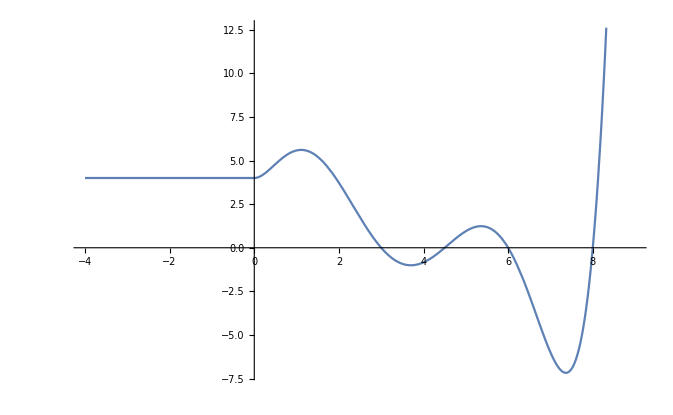

```mathematica
Plot[piecewise[x],{x,-4,9}]
```

```mathematica
piecewise[5.25]
```

1.20795

```mathematica
metric={{hp,0,0},{0,-hp,0},{0,0,0}};
metric//MatrixForm
RotationMatrix[Pi/2,{0,0,1}].metric//MatrixForm
```

(hp | 0 | 0
0 | -hp | 0
0 | 0 | 0)

(0 | hp | 0
hp | 0 | 0
0 | 0 | 0)

```mathematica
rotateCartesianVector[{x,-y,0},{Pi/2,0,0}]
```

{y,x,0}

```mathematica
D[n^(1-s),s]
```

-n^(1-s) Log[n]

```mathematica
vt*Sqrt[33.170327016431585]
```

12047.6

```mathematica
Simplify[Activate[magneticFieldTEnotrotated[A,1,0,1,2,a,wavenumberTE[0,1,2,a],a,θ,ϕ].magneticFieldTEnotrotated[A,1,0,1,2,a,wavenumberTE[0,1,2,a],a,θ,ϕ]]]

Simplify[Activate[electricFieldTEnotrotated[A,1,0,1,2,a,wavenumberTE[0,1,2,a],a,θ,ϕ].magneticFieldTEnotrotated[A,1,0,1,2,a,wavenumberTE[0,1,2,a],a,θ,ϕ]]]
```

A^2 (1.50707×10^-18 Cos[θ]^2+0.01648 Sin[θ]^2)

0